
-Graphics-
Previous notebook		Content		Next notebook

## Isomorphism of algebras (2017-09-20)

### Load main notebook

Load package. WAIT until evaluation of cell is finished to be sure that no errors were produced.

```mathematica
NotebookEvaluate[FileNameJoin[{ParentDirectory[NotebookDirectory[EvaluationNotebook[]]],"GAC_Base.nb"}]]
```

### Definitions and shortcuts

Some shorcuts for vectors and bivectors, which will be used for compact formula tastings. Note, testAlgebra keyword

```mathematica
(* vectors *)
a1:=gaGeneralMultivector[a,testAlgebra,{1}];
b1:=gaGeneralMultivector[b,testAlgebra,{1}];
c1:=gaGeneralMultivector[c,testAlgebra,{1}];
d1:=gaGeneralMultivector[d,testAlgebra,{1}];
f1:=gaGeneralMultivector[f,testAlgebra,{1}];
(*bivectors*)
𝒜1:=gaGeneralMultivector[𝒜,testAlgebra,{2}];
ℬ1:=gaGeneralMultivector[ℬ,testAlgebra,{2}];
𝒞1:=gaGeneralMultivector[𝒞,testAlgebra,{2}];
(*general multivectors*)
A1:=gaGeneralMultivector[A,testAlgebra];
B1:=gaGeneralMultivector[B,testAlgebra];
F1:=gaGeneralMultivector[F,testAlgebra];
(*general blades*)
A2[part_Integer]:=Take[gaGeneralMultivector[A,testAlgebra],{part}];
B2[part_Integer]:=Take[gaGeneralMultivector[B,testAlgebra],{part}];
F2[part_Integer]:=Take[gaGeneralMultivector[F,testAlgebra],{part}];
```

Sections below are independent. In order to start calculation of any of them in any order you only need to evaluate cells above this line.

### Algebra isomorphism test

#### 5.4,5.9,5.10 and 5.5 examples

```mathematica
gaToTensorProduct[Cl[0,7]]
```

100020200020

```mathematica
gaToTensorProduct[Cl[0,8]]
```

200020200020

```mathematica
Options[gaToTensorProduct]
```

{Order→{{Cl[1,1,0]},{200,020}}}

```mathematica
gaToTensorProduct[Cl[2,8],Order->{{200,020}}]
```

200200020200020

```mathematica
gaFromTensorProduct[gaTensorProduct[Cl[2,0],Cl[0,2],Cl[2,0],Cl[0,2]]]
```

Cl[0,8,0]

```mathematica
MatrixForm/@(PauliSpinUnordered=gaAlgebraToMatrixRepresentation[Cl[3,0],{Cl[0,1]->"Complex",Cl[2,0]->"IPauli[1,2]"},BaseVectorMultipliers->{{1},{-1,-1}},Method ->"TensorProduct"])
```

Base vectors of 010are stored in variable gaOrthonormalBase[Cl[0, 1, 0],{0, 1}].

Base vectors of 010200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{1}].

{(1 | 0
0 | -1),(0 | -ⅈ
ⅈ | 0),(0 | 1
1 | 0)}

```mathematica
MatrixForm/@(PauliSpinVectors=PauliSpinUnordered[[{1,3,2}]])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

Base vectors of Cl[2,0]:

```mathematica
MatrixForm/@(baseVectorscl20=-gaAlgebraToMatrixRepresentation[Cl[2,0],{Cl[2,0]->"IPauli[1,2]"}])
```

{(1 | 0
0 | -1),(0 | -ⅈ
ⅈ | 0)}

Base vectors of Cl[3,0]:

```mathematica
MatrixForm/@(baseVectorscl30={baseVectorscl20[[1]],baseVectorscl20[[2]],I* baseVectorscl20[[1]].baseVectorscl20[[2]]})
```

{(1 | 0
0 | -1),(0 | -ⅈ
ⅈ | 0),(0 | 1
1 | 0)}

```mathematica
MatrixForm/@(gaAlgebraToMatrixRepresentation[Cl[3,0],baseVectorscl30])
```

{(1 | 0
0 | 1),(1 | 0
0 | -1),(0 | -ⅈ
ⅈ | 0),(0 | 1
1 | 0),(0 | -ⅈ
-ⅈ | 0),(0 | 1
-1 | 0),(-ⅈ | 0
0 | ⅈ),(-ⅈ | 0
0 | -ⅈ)}

#### 5.7 example: isomorphisms of even subalgebras

First define orthonormal basis of all algebras we will need in this example

```mathematica
testAlgebra=Cl[1,3];
{gaDefineOrthonormalBase[testAlgebra,Quiet->True],gaDefineOrthonormalBase[Cl[3,0],Quiet->True],gaDefineOrthonormalBase[Cl[1,2],Quiet->True],gaDefineOrthonormalBase[Cl[0,2],Quiet->True],gaDefineOrthonormalBase[Cl[2,0],Quiet->True],gaDefineOrthonormalBase[Cl[1,1],Quiet->True],gaDefineOrthonormalBase[Cl[0,1],Quiet->True],gaDefineOrthonormalBase[Cl[1,0],Quiet->True]}
```

Base vectors of 130are stored in variable gaOrthonormalBase[Cl[1, 3, 0]].

Base vectors of 300are stored in variable gaOrthonormalBase[Cl[3, 0, 0]].

Base vectors of 120are stored in variable gaOrthonormalBase[Cl[1, 2, 0]].

Base vectors of 020are stored in variable gaOrthonormalBase[Cl[0, 2, 0]].

Base vectors of 200are stored in variable gaOrthonormalBase[Cl[2, 0, 0]].

Base vectors of 110are stored in variable gaOrthonormalBase[Cl[1, 1, 0]].

Base vectors of 010are stored in variable gaOrthonormalBase[Cl[0, 1, 0]].

Base vectors of 100are stored in variable gaOrthonormalBase[Cl[1, 0, 0]].

{{1,1130,2130,3130,4130,12130,13130,14130,23130,24130,34130,123130,124130,134130,234130,1234130},{1,1300,2300,3300,12300,13300,23300,123300},{1,1120,2120,3120,12120,13120,23120,123120},{1,1020,2020,12020},{1,1200,2200,12200},{1,1110,2110,12110},{1,1010},{1,1100}}

Below is a function, which tries to represent base vector multiplication table as a undirected graph. The representation is based on 𝕖lement ordering possibility, so may not work for more general cases. This is the “state of the art” functions. It seems works on examples below, except that this method cannot account for signs, i.𝕖. graph representation of even subalgebra and subalgebra with bivector sign changed to oposite are the same.

```mathematica
gaAlgebraMultiplicationTableGraph::badOptionValue="Option `1` is not a list of grades {{1},{3},...}. All multiplication table will be generated.";

makeUndirected[a_,b_]:=UndirectedEdge[a,b]/;gaOrderedQ["InvDeg[Lex]"][a,b]
makeUndirected[a_,b_]:=UndirectedEdge[b,a]/;!gaOrderedQ["InvDeg[Lex]"][a,b]
makeEdge[a_,b_]:={makeUndirected[a,GeometricProduct[a,b]],makeUndirected[b,GeometricProduct[a,b]]}


Options[gaAlgebraMultiplicationTableGraph]={gaGradesOnly->All};


gaAlgebraMultiplicationTableGraph[al_,opts___?OptionQ]:=Module[{grades=(gaGradesOnly/.{opts}/.Options[gaAlgebraMultiplicationTableGraph,gaGradesOnly]),selectedBE=gaOrthonormalBase[al]},
Switch[grades,All,
(*the more exact way would be to use generalised commented graphs unfortunatelly isomorhism for them is not implemented. All replacement rules are simplifications, which, hope, will not spoil the result*)
Graph[Union[Flatten[Outer[makeEdge[#1,#2]&,selectedBE,selectedBE]]]]
,{{_Integer?NonNegative}..},
selectedBE=Flatten[Map[Function[{x},Cases[gaOrthonormalBase[al],_?(gaGetGrade[#]===x&)]],grades]];
Graph[Union[Flatten[Outer[makeEdge[#1,#2]&,selectedBE,selectedBE]]]]
,_,Message[gaAlgebraMultiplicationTable::badOptionValue,grades];
Graph[Union[Flatten[Outer[makeEdge[#1,#2]&,selectedBE,selectedBE]]]]]
];
```

Now convert both algebras to graph, then find isomorphism between them and check, that on applying it we get the same multiplication table

Cl[1,3] even is isomorphics to Cl[3,0]

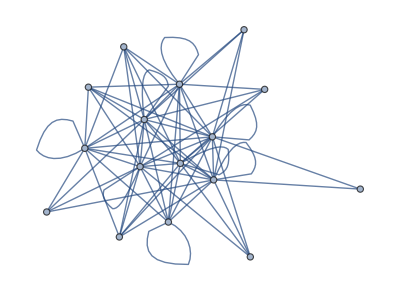

```mathematica
evenSubalgebraGraph[Cl[1,3]]=gaAlgebraMultiplicationTableGraph[Cl[1,3],gaGradesOnly->{{0},{2},{4}}]
```

```mathematica
allAlgebraGraph[Cl[3,0]]=gaAlgebraMultiplicationTableGraph[Cl[3,0]]
```

-Graphics-

Both graphs indeed look simirlarly, so try to find isomorphism

```mathematica
IsomorphicGraphQ[evenSubalgebraGraph[Cl[1,3]],allAlgebraGraph[Cl[3,0]]]
```

True

```mathematica
allIsomorphisms[Cl[1,3]->Cl[3,0]]=FindGraphIsomorphism[evenSubalgebraGraph[Cl[1,3]],allAlgebraGraph[Cl[3,0]],All]
```

{<|-1→-1,23130→12300,24130→13300,34130→23300,1234130→123300,1→1,12130→1300,13130→2300,14130→3300,-12130→-1300,-13130→-2300,-14130→-3300,-23130→-12300,-24130→-13300,-34130→-23300,-1234130→-123300|>,<|-1→-1,23130→23300,24130→13300,34130→12300,1234130→123300,1→1,12130→3300,13130→2300,14130→1300,-12130→-3300,-13130→-2300,-14130→-1300,-23130→-23300,-24130→-13300,-34130→-12300,-1234130→-123300|>}

```mathematica
isomorphismRules[Cl[1,3]->Cl[3,0],1]=allIsomorphisms[Cl[1,3]->Cl[3,0]][[1]]
```

<|-1→-1,23130→12300,24130→13300,34130→23300,1234130→123300,1→1,12130→1300,13130→2300,14130→3300,-12130→-1300,-13130→-2300,-14130→-3300,-23130→-12300,-24130→-13300,-34130→-23300,-1234130→-123300|>

```mathematica
isomorphismRules[Cl[1,3]->Cl[3,0],2]=allIsomorphisms[Cl[1,3]->Cl[3,0]][[2]]
```

<|-1→-1,23130→23300,24130→13300,34130→12300,1234130→123300,1→1,12130→3300,13130→2300,14130→1300,-12130→-3300,-13130→-2300,-14130→-1300,-23130→-23300,-24130→-13300,-34130→-12300,-1234130→-123300|>

In order to get exact match between multiplication tables using the first isomorphism rules we need to do is to change signs of all Cl[1,3] bivectors:

```mathematica
trueSubstitutionRules[Cl[1,3]->Cl[3,0],1]=Rule@@@Flatten[{#,#/.{-a_,b_}:>{a,-b}}&/@(Transpose[MapAt[Map[If[gaGetGrade[#]==={2},#*(-1),#]&,#]&,Transpose[List@@@DeleteCases[Normal[isomorphismRules[Cl[1,3]->Cl[3,0],1]],Rule[a_,a_]|Rule[-a_,-b_]]],1]]),1]
```

{-23130→12300,23130→-12300,-24130→13300,24130→-13300,-34130→23300,34130→-23300,1234130→123300,1234130→123300,-12130→1300,12130→-1300,-13130→2300,13130→-2300,-14130→3300,14130→-3300}

In order to check that Caylay tables are isomorphic, reorder bivectors and make them of appropriate sign

```mathematica
elementsForCheck[Cl[1,3]->Cl[3,0],1]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[3,0]])/.(Reverse/@Union[trueSubstitutionRules[Cl[1,3]->Cl[3,0],1]])
(checkResult[Cl[1,3]->Cl[3,0],1]=Outer[GeometricProduct,%,%])//TableForm
```

{1,-12130,-13130,-14130,-23130,-24130,-34130,1234130}

1 | -12130 | -13130 | -14130 | -23130 | -24130 | -34130 | 1234130
-12130 | 1 | -23130 | -24130 | -13130 | -14130 | 1234130 | -34130
-13130 | 23130 | 1 | -34130 | 12130 | -1234130 | -14130 | 24130
-14130 | 24130 | 34130 | 1 | 1234130 | 12130 | 13130 | -23130
-23130 | 13130 | -12130 | 1234130 | -1 | 34130 | -24130 | 14130
-24130 | 14130 | -1234130 | -12130 | -34130 | -1 | 23130 | -13130
-34130 | 1234130 | 14130 | -13130 | 24130 | -23130 | -1 | 12130
1234130 | -34130 | 24130 | -23130 | 14130 | -13130 | 12130 | -1

```mathematica
checkAnswer[Cl[1,3]->Cl[3,0],1]=(checkResult[Cl[1,3]->Cl[3,0],1]/.trueSubstitutionRules[Cl[1,3]->Cl[3,0],1])
```

{{1,1300,2300,3300,12300,13300,23300,123300},{1300,1,12300,13300,2300,3300,123300,23300},{2300,-12300,1,23300,-1300,-123300,3300,-13300},{3300,-13300,-23300,1,123300,-1300,-2300,12300},{12300,-2300,1300,123300,-1,-23300,13300,-3300},{13300,-3300,-123300,1300,23300,-1,-12300,2300},{23300,123300,-3300,2300,-13300,12300,-1,-1300},{123300,23300,-13300,12300,-3300,2300,-1300,-1}}

And compare it with

```mathematica
mTableAll[Cl[3,0]]=gaAlgebraMultiplicationTable[Cl[3,0]]
```

| 1 | 1300 | 2300 | 3300 | 12300 | 13300 | 23300 | 123300
1 | 1 | 1300 | 2300 | 3300 | 12300 | 13300 | 23300 | 123300
1300 | 1300 | 1 | 12300 | 13300 | 2300 | 3300 | 123300 | 23300
2300 | 2300 | -12300 | 1 | 23300 | -1300 | -123300 | 3300 | -13300
3300 | 3300 | -13300 | -23300 | 1 | 123300 | -1300 | -2300 | 12300
12300 | 12300 | -2300 | 1300 | 123300 | -1 | -23300 | 13300 | -3300
13300 | 13300 | -3300 | -123300 | 1300 | 23300 | -1 | -12300 | 2300
23300 | 23300 | 123300 | -3300 | 2300 | -13300 | 12300 | -1 | -1300
123300 | 123300 | 23300 | -13300 | 12300 | -3300 | 2300 | -1300 | -1

```mathematica
mTableAll[Cl[3,0]][[1]]-checkAnswer[Cl[1,3]->Cl[3,0],1]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

The second graph isomorphism yields Caylay table isomorphism, without bivector reflection !

```mathematica
trueSubstitutionRules[Cl[1,3]->Cl[3,0],2]=DeleteCases[Normal[isomorphismRules[Cl[1,3]->Cl[3,0],2]],Rule[a_,a_]]
```

{23130→23300,24130→13300,34130→12300,1234130→123300,12130→3300,13130→2300,14130→1300,-12130→-3300,-13130→-2300,-14130→-1300,-23130→-23300,-24130→-13300,-34130→-12300,-1234130→-123300}

```mathematica
elementsForCheck[Cl[1,3]->Cl[3,0],2]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[3,0]])/.(Reverse/@Union[trueSubstitutionRules[Cl[1,3]->Cl[3,0],2]])
(checkResult[Cl[1,3]->Cl[3,0],2]=Outer[GeometricProduct,%,%])//TableForm
```

{1,14130,13130,12130,34130,24130,23130,1234130}

1 | 14130 | 13130 | 12130 | 34130 | 24130 | 23130 | 1234130
14130 | 1 | 34130 | 24130 | 13130 | 12130 | 1234130 | 23130
13130 | -34130 | 1 | 23130 | -14130 | -1234130 | 12130 | -24130
12130 | -24130 | -23130 | 1 | 1234130 | -14130 | -13130 | 34130
34130 | -13130 | 14130 | 1234130 | -1 | -23130 | 24130 | -12130
24130 | -12130 | -1234130 | 14130 | 23130 | -1 | -34130 | 13130
23130 | 1234130 | -12130 | 13130 | -24130 | 34130 | -1 | -14130
1234130 | 23130 | -24130 | 34130 | -12130 | 13130 | -14130 | -1

```mathematica
checkAnswer[Cl[1,3]->Cl[3,0],2]=(checkResult[Cl[1,3]->Cl[3,0],2]/.trueSubstitutionRules[Cl[1,3]->Cl[3,0],2])
```

{{1,1300,2300,3300,12300,13300,23300,123300},{1300,1,12300,13300,2300,3300,123300,23300},{2300,-12300,1,23300,-1300,-123300,3300,-13300},{3300,-13300,-23300,1,123300,-1300,-2300,12300},{12300,-2300,1300,123300,-1,-23300,13300,-3300},{13300,-3300,-123300,1300,23300,-1,-12300,2300},{23300,123300,-3300,2300,-13300,12300,-1,-1300},{123300,23300,-13300,12300,-3300,2300,-1300,-1}}

And compare it with

```mathematica
mTableAll[Cl[3,0]]=gaAlgebraMultiplicationTable[Cl[3,0]]
```

| 1 | 1300 | 2300 | 3300 | 12300 | 13300 | 23300 | 123300
1 | 1 | 1300 | 2300 | 3300 | 12300 | 13300 | 23300 | 123300
1300 | 1300 | 1 | 12300 | 13300 | 2300 | 3300 | 123300 | 23300
2300 | 2300 | -12300 | 1 | 23300 | -1300 | -123300 | 3300 | -13300
3300 | 3300 | -13300 | -23300 | 1 | 123300 | -1300 | -2300 | 12300
12300 | 12300 | -2300 | 1300 | 123300 | -1 | -23300 | 13300 | -3300
13300 | 13300 | -3300 | -123300 | 1300 | 23300 | -1 | -12300 | 2300
23300 | 23300 | 123300 | -3300 | 2300 | -13300 | 12300 | -1 | -1300
123300 | 123300 | 23300 | -13300 | 12300 | -3300 | 2300 | -1300 | -1

```mathematica
mTableAll[Cl[3,0]][[1]]-checkAnswer[Cl[1,3]->Cl[3,0],2]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

Cl[3,0] even is isomorphics to Cl[0,2] and Cl[1,3]->Cl[3,0]->Cl[0,2]

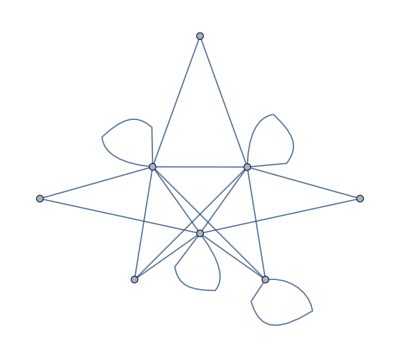

```mathematica
evenSubalgebraGraph[Cl[3,0]]=gaAlgebraMultiplicationTableGraph[Cl[3,0],gaGradesOnly->{{0},{2},{4}}]
```

```mathematica
allAlgebraGraph[Cl[0,2]]=gaAlgebraMultiplicationTableGraph[Cl[0,2]]
```

-Graphics-

Both graphs indeed look simirlarly, so try to find isomorphism

```mathematica
IsomorphicGraphQ[evenSubalgebraGraph[Cl[3,0]],allAlgebraGraph[Cl[0,2]]]
```

True

```mathematica
allIsomorphisms[Cl[3,0]->Cl[0,2]]=FindGraphIsomorphism[evenSubalgebraGraph[Cl[3,0]],allAlgebraGraph[Cl[0,2]],All]
```

{<|-1→-1,12300→1020,13300→2020,23300→12020,1→1,-12300→-1020,-13300→-2020,-23300→-12020|>,<|-1→-1,12300→1020,13300→12020,23300→2020,1→1,-12300→-1020,-13300→-12020,-23300→-2020|>,<|-1→-1,12300→2020,13300→1020,23300→12020,1→1,-12300→-2020,-13300→-1020,-23300→-12020|>,<|-1→-1,12300→2020,13300→12020,23300→1020,1→1,-12300→-2020,-13300→-12020,-23300→-1020|>,<|-1→-1,12300→12020,13300→1020,23300→2020,1→1,-12300→-12020,-13300→-1020,-23300→-2020|>,<|-1→-1,12300→12020,13300→2020,23300→1020,1→1,-12300→-12020,-13300→-2020,-23300→-1020|>}

```mathematica
Table[isomorphismRules[Cl[3,0]->Cl[0,2],n]=allIsomorphisms[Cl[3,0]->Cl[0,2]][[n]],{n,1,Length[allIsomorphisms[Cl[3,0]->Cl[0,2]]]}]
```

{<|-1→-1,12300→1020,13300→2020,23300→12020,1→1,-12300→-1020,-13300→-2020,-23300→-12020|>,<|-1→-1,12300→1020,13300→12020,23300→2020,1→1,-12300→-1020,-13300→-12020,-23300→-2020|>,<|-1→-1,12300→2020,13300→1020,23300→12020,1→1,-12300→-2020,-13300→-1020,-23300→-12020|>,<|-1→-1,12300→2020,13300→12020,23300→1020,1→1,-12300→-2020,-13300→-12020,-23300→-1020|>,<|-1→-1,12300→12020,13300→1020,23300→2020,1→1,-12300→-12020,-13300→-1020,-23300→-2020|>,<|-1→-1,12300→12020,13300→2020,23300→1020,1→1,-12300→-12020,-13300→-2020,-23300→-1020|>}

First detect isomorphisms without reflections. These are  No. 2

```mathematica
trueSubstitutionRules[Cl[3,0]->Cl[0,2],2]=DeleteCases[Normal[isomorphismRules[Cl[3,0]->Cl[0,2],2]],Rule[a_,a_]]
```

{12300→1020,13300→12020,23300→2020,-12300→-1020,-13300→-12020,-23300→-2020}

```mathematica
elementsForCheck[Cl[3,0]->Cl[0,2],2]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[0,2]])/.(Reverse/@Union[trueSubstitutionRules[Cl[3,0]->Cl[0,2],2]])
(checkResult[Cl[3,0]->Cl[0,2],2]=Outer[GeometricProduct,%,%])//TableForm
```

{1,12300,23300,13300}

1 | 12300 | 23300 | 13300
12300 | -1 | 13300 | -23300
23300 | -13300 | -1 | 12300
13300 | 23300 | -12300 | -1

```mathematica
checkAnswer[Cl[3,0]->Cl[0,2],2]=(checkResult[Cl[3,0]->Cl[0,2],2]/.trueSubstitutionRules[Cl[3,0]->Cl[0,2],2])
```

{{1,1020,2020,12020},{1020,-1,12020,-2020},{2020,-12020,-1,1020},{12020,2020,-1020,-1}}

And compare it with

```mathematica
mTableAll[Cl[0,2]]=gaAlgebraMultiplicationTable[Cl[0,2]]
```

| 1 | 1020 | 2020 | 12020
1 | 1 | 1020 | 2020 | 12020
1020 | 1020 | -1 | 12020 | -2020
2020 | 2020 | -12020 | -1 | 1020
12020 | 12020 | 2020 | -1020 | -1

```mathematica
mTableAll[Cl[0,2]][[1]]-checkAnswer[Cl[3,0]->Cl[0,2],2]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

First detect isomorphisms without reflections No. 3

```mathematica
trueSubstitutionRules[Cl[3,0]->Cl[0,2],3]=DeleteCases[Normal[isomorphismRules[Cl[3,0]->Cl[0,2],3]],Rule[a_,a_]]
```

{12300→2020,13300→1020,23300→12020,-12300→-2020,-13300→-1020,-23300→-12020}

```mathematica
elementsForCheck[Cl[3,0]->Cl[0,2],3]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[0,2]])/.(Reverse/@Union[trueSubstitutionRules[Cl[3,0]->Cl[0,2],3]])
(checkResult[Cl[3,0]->Cl[0,2],3]=Outer[GeometricProduct,%,%])//TableForm
```

{1,13300,12300,23300}

1 | 13300 | 12300 | 23300
13300 | -1 | 23300 | -12300
12300 | -23300 | -1 | 13300
23300 | 12300 | -13300 | -1

```mathematica
checkAnswer[Cl[3,0]->Cl[0,2],3]=(checkResult[Cl[3,0]->Cl[0,2],3]/.trueSubstitutionRules[Cl[3,0]->Cl[0,2],3])
```

{{1,1020,2020,12020},{1020,-1,12020,-2020},{2020,-12020,-1,1020},{12020,2020,-1020,-1}}

```mathematica
mTableAll[Cl[0,2]][[1]]-checkAnswer[Cl[3,0]->Cl[0,2],3]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

First detect isomorphisms without reflections No. 6

```mathematica
trueSubstitutionRules[Cl[3,0]->Cl[0,2],6]=DeleteCases[Normal[isomorphismRules[Cl[3,0]->Cl[0,2],6]],Rule[a_,a_]]
```

{12300→12020,13300→2020,23300→1020,-12300→-12020,-13300→-2020,-23300→-1020}

```mathematica
elementsForCheck[Cl[3,0]->Cl[0,2],6]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[0,2]])/.(Reverse/@Union[trueSubstitutionRules[Cl[3,0]->Cl[0,2],6]])
(checkResult[Cl[3,0]->Cl[0,2],6]=Outer[GeometricProduct,%,%])//TableForm
```

{1,23300,13300,12300}

1 | 23300 | 13300 | 12300
23300 | -1 | 12300 | -13300
13300 | -12300 | -1 | 23300
12300 | 13300 | -23300 | -1

```mathematica
checkAnswer[Cl[3,0]->Cl[0,2],6]=(checkResult[Cl[3,0]->Cl[0,2],6]/.trueSubstitutionRules[Cl[3,0]->Cl[0,2],6])
```

{{1,1020,2020,12020},{1020,-1,12020,-2020},{2020,-12020,-1,1020},{12020,2020,-1020,-1}}

```mathematica
mTableAll[Cl[0,2]][[1]]-checkAnswer[Cl[3,0]->Cl[0,2],6]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

First detect isomorphisms WITH reflections No. 1

```mathematica
trueSubstitutionRules[Cl[3,0]->Cl[0,2],1]=Rule@@@Flatten[{#,#/.{-a_,b_}:>{a,-b}}&/@(Transpose[MapAt[Map[If[gaGetGrade[#]==={2},#*(-1),#]&,#]&,Transpose[List@@@DeleteCases[Normal[isomorphismRules[Cl[3,0]->Cl[0,2],1]],Rule[a_,a_]|Rule[-a_,-b_]]],1]]),1]
```

{-12300→1020,12300→-1020,-13300→2020,13300→-2020,-23300→12020,23300→-12020}

```mathematica
elementsForCheck[Cl[3,0]->Cl[0,2],1]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[0,2]])/.(Reverse/@Union[trueSubstitutionRules[Cl[3,0]->Cl[0,2],1]])
(checkResult[Cl[3,0]->Cl[0,2],1]=Outer[GeometricProduct,%,%])//TableForm
```

{1,-12300,-13300,-23300}

1 | -12300 | -13300 | -23300
-12300 | -1 | -23300 | 13300
-13300 | 23300 | -1 | -12300
-23300 | -13300 | 12300 | -1

```mathematica
checkAnswer[Cl[3,0]->Cl[0,2],1]=(checkResult[Cl[3,0]->Cl[0,2],1]/.trueSubstitutionRules[Cl[3,0]->Cl[0,2],1])
```

{{1,1020,2020,12020},{1020,-1,12020,-2020},{2020,-12020,-1,1020},{12020,2020,-1020,-1}}

And compare it with

```mathematica
mTableAll[Cl[0,2]]=gaAlgebraMultiplicationTable[Cl[0,2]]
```

| 1 | 1020 | 2020 | 12020
1 | 1 | 1020 | 2020 | 12020
1020 | 1020 | -1 | 12020 | -2020
2020 | 2020 | -12020 | -1 | 1020
12020 | 12020 | 2020 | -1020 | -1

```mathematica
mTableAll[Cl[0,2]][[1]]-checkAnswer[Cl[3,0]->Cl[0,2],1]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

First detect isomorphisms without reflections No. 4

```mathematica
trueSubstitutionRules[Cl[3,0]->Cl[0,2],4]=Rule@@@Flatten[{#,#/.{-a_,b_}:>{a,-b}}&/@(Transpose[MapAt[Map[If[gaGetGrade[#]==={2},#*(-1),#]&,#]&,Transpose[List@@@DeleteCases[Normal[isomorphismRules[Cl[3,0]->Cl[0,2],4]],Rule[a_,a_]|Rule[-a_,-b_]]],1]]),1]
```

{-12300→2020,12300→-2020,-13300→12020,13300→-12020,-23300→1020,23300→-1020}

```mathematica
elementsForCheck[Cl[3,0]->Cl[0,2],4]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[0,2]])/.(Reverse/@Union[trueSubstitutionRules[Cl[3,0]->Cl[0,2],4]])
(checkResult[Cl[3,0]->Cl[0,2],4]=Outer[GeometricProduct,%,%])//TableForm
```

{1,-23300,-12300,-13300}

1 | -23300 | -12300 | -13300
-23300 | -1 | -13300 | 12300
-12300 | 13300 | -1 | -23300
-13300 | -12300 | 23300 | -1

```mathematica
checkAnswer[Cl[3,0]->Cl[0,2],4]=(checkResult[Cl[3,0]->Cl[0,2],4]/.trueSubstitutionRules[Cl[3,0]->Cl[0,2],4])
```

{{1,1020,2020,12020},{1020,-1,12020,-2020},{2020,-12020,-1,1020},{12020,2020,-1020,-1}}

```mathematica
mTableAll[Cl[0,2]][[1]]-checkAnswer[Cl[3,0]->Cl[0,2],4]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

First detect isomorphisms without reflections No. 5

```mathematica
trueSubstitutionRules[Cl[3,0]->Cl[0,2],5]=Rule@@@Flatten[{#,#/.{-a_,b_}:>{a,-b}}&/@(Transpose[MapAt[Map[If[gaGetGrade[#]==={2},#*(-1),#]&,#]&,Transpose[List@@@DeleteCases[Normal[isomorphismRules[Cl[3,0]->Cl[0,2],5]],Rule[a_,a_]|Rule[-a_,-b_]]],1]]),1]
```

{-12300→12020,12300→-12020,-13300→1020,13300→-1020,-23300→2020,23300→-2020}

```mathematica
elementsForCheck[Cl[3,0]->Cl[0,2],5]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[0,2]])/.(Reverse/@Union[trueSubstitutionRules[Cl[3,0]->Cl[0,2],5]])
(checkResult[Cl[3,0]->Cl[0,2],5]=Outer[GeometricProduct,%,%])//TableForm
```

{1,-13300,-23300,-12300}

1 | -13300 | -23300 | -12300
-13300 | -1 | -12300 | 23300
-23300 | 12300 | -1 | -13300
-12300 | -23300 | 13300 | -1

```mathematica
checkAnswer[Cl[3,0]->Cl[0,2],5]=(checkResult[Cl[3,0]->Cl[0,2],5]/.trueSubstitutionRules[Cl[3,0]->Cl[0,2],5])
```

{{1,1020,2020,12020},{1020,-1,12020,-2020},{2020,-12020,-1,1020},{12020,2020,-1020,-1}}

```mathematica
mTableAll[Cl[0,2]][[1]]-checkAnswer[Cl[3,0]->Cl[0,2],5]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

Now relate it to Cl[1,3] base elements. It is 2*6=12 variants possible

```mathematica
trueSubstitutionRules[Cl[3,0]->Cl[0,2],2]
```

{12300→1020,13300→12020,23300→2020,-12300→-1020,-13300→-12020,-23300→-2020}

```mathematica
trueSubstitutionRules[Cl[1,3]->Cl[3,0],2]
```

{23130→23300,24130→13300,34130→12300,1234130→123300,12130→3300,13130→2300,14130→1300,-12130→-3300,-13130→-2300,-14130→-1300,-23130→-23300,-24130→-13300,-34130→-12300,-1234130→-123300}

```mathematica
gaDefineInput[Cl[0,2]]
```

Running algebra is: gaRunningAlgebra= Cl[0, 2, 0]

No inversion in both chains

```mathematica
({𝕖[1],𝕖[2]}/.(Reverse/@trueSubstitutionRules[Cl[3,0]->Cl[0,2],2]))/.(Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[3,0],2])
```

{34130,23130}

```mathematica
({𝕖[1],𝕖[2]}/.(Reverse/@trueSubstitutionRules[Cl[3,0]->Cl[0,2],3]))/.(Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[3,0],2])
```

{24130,34130}

```mathematica
({𝕖[1],𝕖[2]}/.(Reverse/@trueSubstitutionRules[Cl[3,0]->Cl[0,2],6]))/.(Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[3,0],2])
```

{23130,24130}

Inversion in 𝕖ach chain

```mathematica
({𝕖[1],𝕖[2]}/.(Reverse/@trueSubstitutionRules[Cl[3,0]->Cl[0,2],1]))/.(Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[3,0],1])
```

{23130,24130}

```mathematica
({𝕖[1],𝕖[2]}/.(Reverse/@trueSubstitutionRules[Cl[3,0]->Cl[0,2],4]))/.(Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[3,0],1])
```

{34130,23130}

```mathematica
({𝕖[1],𝕖[2]}/.(Reverse/@trueSubstitutionRules[Cl[3,0]->Cl[0,2],5]))/.(Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[3,0],1])
```

{24130,34130}

Inversion in one of chains

```mathematica
({𝕖[1],𝕖[2]}/.(Reverse/@trueSubstitutionRules[Cl[3,0]->Cl[0,2],1]))/.(Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[3,0],2])
```

{-34130,-24130}

```mathematica
({𝕖[1],𝕖[2]}/.(Reverse/@trueSubstitutionRules[Cl[3,0]->Cl[0,2],4]))/.(Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[3,0],2])
```

{-23130,-34130}

```mathematica
({𝕖[1],𝕖[2]}/.(Reverse/@trueSubstitutionRules[Cl[3,0]->Cl[0,2],5]))/.(Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[3,0],2])
```

{-24130,-23130}

```mathematica
({𝕖[1],𝕖[2]}/.(Reverse/@trueSubstitutionRules[Cl[3,0]->Cl[0,2],2]))/.(Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[3,0],1])
```

{-23130,-34130}

```mathematica
({𝕖[1],𝕖[2]}/.(Reverse/@trueSubstitutionRules[Cl[3,0]->Cl[0,2],3]))/.(Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[3,0],1])
```

{-24130,-23130}

```mathematica
({𝕖[1],𝕖[2]}/.(Reverse/@trueSubstitutionRules[Cl[3,0]->Cl[0,2],6]))/.(Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[3,0],1])
```

{-34130,-24130}

Cl[1,3] even is isomorphics to Cl[1,2]

```mathematica
evenSubalgebraGraph[Cl[1,3]]=gaAlgebraMultiplicationTableGraph[Cl[1,3],gaGradesOnly->{{0},{2},{4}}]
```

-Graphics-

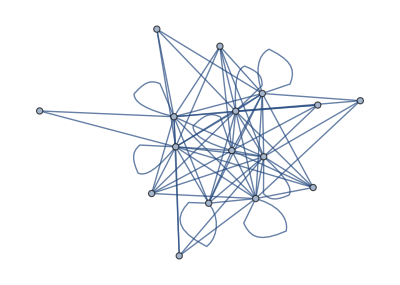

```mathematica
allAlgebraGraph[Cl[1,2]]=gaAlgebraMultiplicationTableGraph[Cl[1,2]]
```

Both graphs indeed look simirlarly, so try to find isomorphism

```mathematica
IsomorphicGraphQ[evenSubalgebraGraph[Cl[1,3]],allAlgebraGraph[Cl[1,2]]]
```

True

```mathematica
allIsomorphisms[Cl[1,3]->Cl[1,2]]=FindGraphIsomorphism[evenSubalgebraGraph[Cl[1,3]],allAlgebraGraph[Cl[1,2]],All]
```

{<|-1→-1,23130→3120,24130→2120,34130→23120,1234130→123120,1→1,12130→1120,13130→13120,14130→12120,-12130→-1120,-13130→-13120,-14130→-12120,-23130→-3120,-24130→-2120,-34130→-23120,-1234130→-123120|>,<|-1→-1,23130→23120,24130→2120,34130→3120,1234130→123120,1→1,12130→12120,13130→13120,14130→1120,-12130→-12120,-13130→-13120,-14130→-1120,-23130→-23120,-24130→-2120,-34130→-3120,-1234130→-123120|>}

```mathematica
isomorphismRules[Cl[1,3]->Cl[1,2],1]=allIsomorphisms[Cl[1,3]->Cl[1,2]][[1]]
```

<|-1→-1,23130→3120,24130→2120,34130→23120,1234130→123120,1→1,12130→1120,13130→13120,14130→12120,-12130→-1120,-13130→-13120,-14130→-12120,-23130→-3120,-24130→-2120,-34130→-23120,-1234130→-123120|>

```mathematica
isomorphismRules[Cl[1,3]->Cl[1,2],2]=allIsomorphisms[Cl[1,3]->Cl[1,2]][[2]]
```

<|-1→-1,23130→23120,24130→2120,34130→3120,1234130→123120,1→1,12130→12120,13130→13120,14130→1120,-12130→-12120,-13130→-13120,-14130→-1120,-23130→-23120,-24130→-2120,-34130→-3120,-1234130→-123120|>

In order to get exact match between multiplication tables using the first isomorphism rules we need to do is to change signs of all Cl[1,3] bivectors:

```mathematica
trueSubstitutionRules[Cl[1,3]->Cl[1,2],1]=Rule@@@Flatten[{#,#/.{-a_,b_}:>{a,-b}}&/@(Transpose[MapAt[Map[If[gaGetGrade[#]==={2},#*(-1),#]&,#]&,Transpose[List@@@DeleteCases[Normal[isomorphismRules[Cl[1,3]->Cl[1,2],1]],Rule[a_,a_]|Rule[-a_,-b_]]],1]]),1]
```

{-23130→3120,23130→-3120,-24130→2120,24130→-2120,-34130→23120,34130→-23120,1234130→123120,1234130→123120,-12130→1120,12130→-1120,-13130→13120,13130→-13120,-14130→12120,14130→-12120}

In order to check that Caylay tables are isomorphic, reorder bivectors and make them of appropriate sign

```mathematica
elementsForCheck[Cl[1,3]->Cl[1,2],1]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[1,2]])/.(Reverse/@Union[trueSubstitutionRules[Cl[1,3]->Cl[1,2],1]])
(checkResult[Cl[1,3]->Cl[1,2],1]=Outer[GeometricProduct,%,%])//TableForm
```

{1,-12130,-24130,-23130,-14130,-13130,-34130,1234130}

1 | -12130 | -24130 | -23130 | -14130 | -13130 | -34130 | 1234130
-12130 | 1 | -14130 | -13130 | -24130 | -23130 | 1234130 | -34130
-24130 | 14130 | -1 | -34130 | -12130 | -1234130 | 23130 | -13130
-23130 | 13130 | 34130 | -1 | 1234130 | -12130 | -24130 | 14130
-14130 | 24130 | 12130 | 1234130 | 1 | 34130 | 13130 | -23130
-13130 | 23130 | -1234130 | 12130 | -34130 | 1 | -14130 | 24130
-34130 | 1234130 | -23130 | 24130 | -13130 | 14130 | -1 | 12130
1234130 | -34130 | -13130 | 14130 | -23130 | 24130 | 12130 | -1

```mathematica
checkAnswer[Cl[1,3]->Cl[1,2],1]=(checkResult[Cl[1,3]->Cl[1,2],1]/.trueSubstitutionRules[Cl[1,3]->Cl[1,2],1])
```

{{1,1120,2120,3120,12120,13120,23120,123120},{1120,1,12120,13120,2120,3120,123120,23120},{2120,-12120,-1,23120,1120,-123120,-3120,13120},{3120,-13120,-23120,-1,123120,1120,2120,-12120},{12120,-2120,-1120,123120,1,-23120,-13120,3120},{13120,-3120,-123120,-1120,23120,1,12120,-2120},{23120,123120,3120,-2120,13120,-12120,-1,-1120},{123120,23120,13120,-12120,3120,-2120,-1120,-1}}

And compare it with

```mathematica
mTableAll[Cl[1,2]]=gaAlgebraMultiplicationTable[Cl[1,2]]
```

| 1 | 1120 | 2120 | 3120 | 12120 | 13120 | 23120 | 123120
1 | 1 | 1120 | 2120 | 3120 | 12120 | 13120 | 23120 | 123120
1120 | 1120 | 1 | 12120 | 13120 | 2120 | 3120 | 123120 | 23120
2120 | 2120 | -12120 | -1 | 23120 | 1120 | -123120 | -3120 | 13120
3120 | 3120 | -13120 | -23120 | -1 | 123120 | 1120 | 2120 | -12120
12120 | 12120 | -2120 | -1120 | 123120 | 1 | -23120 | -13120 | 3120
13120 | 13120 | -3120 | -123120 | -1120 | 23120 | 1 | 12120 | -2120
23120 | 23120 | 123120 | 3120 | -2120 | 13120 | -12120 | -1 | -1120
123120 | 123120 | 23120 | 13120 | -12120 | 3120 | -2120 | -1120 | -1

```mathematica
mTableAll[Cl[1,2]][[1]]-checkAnswer[Cl[1,3]->Cl[1,2],1]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

The second graph isomorphism yields Caylay table isomorphism, without bivector reflection !

```mathematica
trueSubstitutionRules[Cl[1,3]->Cl[1,2],2]=DeleteCases[Normal[isomorphismRules[Cl[1,3]->Cl[1,2],2]],Rule[a_,a_]]
```

{23130→23120,24130→2120,34130→3120,1234130→123120,12130→12120,13130→13120,14130→1120,-12130→-12120,-13130→-13120,-14130→-1120,-23130→-23120,-24130→-2120,-34130→-3120,-1234130→-123120}

```mathematica
elementsForCheck[Cl[1,3]->Cl[1,2],2]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[1,2]])/.(Reverse/@Union[trueSubstitutionRules[Cl[1,3]->Cl[1,2],2]])
(checkResult[Cl[1,3]->Cl[1,2],2]=Outer[GeometricProduct,%,%])//TableForm
```

{1,14130,24130,34130,12130,13130,23130,1234130}

1 | 14130 | 24130 | 34130 | 12130 | 13130 | 23130 | 1234130
14130 | 1 | 12130 | 13130 | 24130 | 34130 | 1234130 | 23130
24130 | -12130 | -1 | 23130 | 14130 | -1234130 | -34130 | 13130
34130 | -13130 | -23130 | -1 | 1234130 | 14130 | 24130 | -12130
12130 | -24130 | -14130 | 1234130 | 1 | -23130 | -13130 | 34130
13130 | -34130 | -1234130 | -14130 | 23130 | 1 | 12130 | -24130
23130 | 1234130 | 34130 | -24130 | 13130 | -12130 | -1 | -14130
1234130 | 23130 | 13130 | -12130 | 34130 | -24130 | -14130 | -1

```mathematica
checkAnswer[Cl[1,3]->Cl[1,2],2]=(checkResult[Cl[1,3]->Cl[1,2],2]/.trueSubstitutionRules[Cl[1,3]->Cl[1,2],2])
```

{{1,1120,2120,3120,12120,13120,23120,123120},{1120,1,12120,13120,2120,3120,123120,23120},{2120,-12120,-1,23120,1120,-123120,-3120,13120},{3120,-13120,-23120,-1,123120,1120,2120,-12120},{12120,-2120,-1120,123120,1,-23120,-13120,3120},{13120,-3120,-123120,-1120,23120,1,12120,-2120},{23120,123120,3120,-2120,13120,-12120,-1,-1120},{123120,23120,13120,-12120,3120,-2120,-1120,-1}}

And compare it with

```mathematica
mTableAll[Cl[]]=gaAlgebraMultiplicationTable[Cl[1,2]]
```

| 1 | 1120 | 2120 | 3120 | 12120 | 13120 | 23120 | 123120
1 | 1 | 1120 | 2120 | 3120 | 12120 | 13120 | 23120 | 123120
1120 | 1120 | 1 | 12120 | 13120 | 2120 | 3120 | 123120 | 23120
2120 | 2120 | -12120 | -1 | 23120 | 1120 | -123120 | -3120 | 13120
3120 | 3120 | -13120 | -23120 | -1 | 123120 | 1120 | 2120 | -12120
12120 | 12120 | -2120 | -1120 | 123120 | 1 | -23120 | -13120 | 3120
13120 | 13120 | -3120 | -123120 | -1120 | 23120 | 1 | 12120 | -2120
23120 | 23120 | 123120 | 3120 | -2120 | 13120 | -12120 | -1 | -1120
123120 | 123120 | 23120 | 13120 | -12120 | 3120 | -2120 | -1120 | -1

```mathematica
mTableAll[Cl[1,2]][[1]]-checkAnswer[Cl[1,3]->Cl[1,2],2]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

Cl[1,4] even is isomorphics to Cl[1,3] (all grade example)

```mathematica
gaDefineOrthonormalBase[Cl[1,4],Quiet->True]
```

Base vectors of 140are stored in variable gaOrthonormalBase[Cl[1, 4, 0]].

{1,1140,2140,3140,4140,5140,12140,13140,14140,15140,23140,24140,25140,34140,35140,45140,123140,124140,125140,134140,135140,145140,234140,235140,245140,345140,1234140,1235140,1245140,1345140,2345140,12345140}

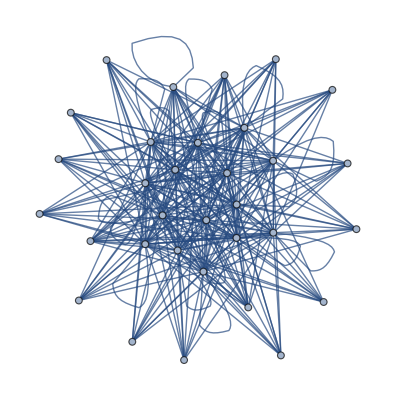

```mathematica
evenSubalgebraGraph[Cl[1,4]]=gaAlgebraMultiplicationTableGraph[Cl[1,4],gaGradesOnly->{{0},{2},{4}}]
```

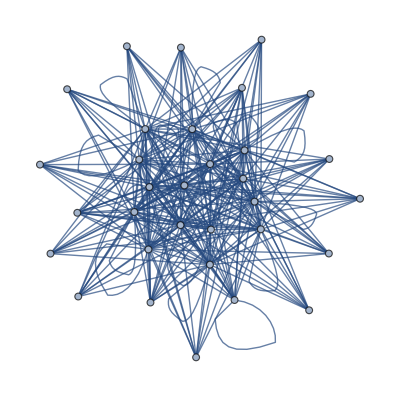

```mathematica
allAlgebraGraph[Cl[1,3]]=gaAlgebraMultiplicationTableGraph[Cl[1,3]]
```

Both graphs indeed look simirlarly, so try to find isomorphism

```mathematica
IsomorphicGraphQ[evenSubalgebraGraph[Cl[1,4]],allAlgebraGraph[Cl[1,3]]]
```

True

```mathematica
allIsomorphisms[Cl[1,4]->Cl[1,3]]=FindGraphIsomorphism[evenSubalgebraGraph[Cl[1,4]],allAlgebraGraph[Cl[1,3]],All]
```

{<|-1→-1,23140→23130,24140→24130,25140→2130,34140→34130,35140→3130,45140→4130,1234140→1234130,1235140→123130,1245140→124130,1345140→134130,1→1,12140→12130,13140→13130,14140→14130,15140→1130,2345140→234130,-12140→-12130,-13140→-13130,-14140→-14130,-15140→-1130,-23140→-23130,-24140→-24130,-25140→-2130,-1345140→-134130,-2345140→-234130,-34140→-34130,-35140→-3130,-1234140→-1234130,-1235140→-123130,-1245140→-124130,-45140→-4130|>,<|-1→-1,23140→24130,24140→134130,25140→2130,34140→123130,35140→4130,45140→1234130,1234140→3130,1235140→124130,1245140→34130,1345140→23130,1→1,12140→12130,13140→14130,14140→234130,15140→1130,2345140→13130,-12140→-12130,-13140→-14130,-14140→-234130,-15140→-1130,-23140→-24130,-24140→-134130,-25140→-2130,-1345140→-23130,-2345140→-13130,-34140→-123130,-35140→-4130,-1234140→-3130,-1235140→-124130,-1245140→-34130,-45140→-1234130|>,<|-1→-1,23140→3130,24140→1234130,25140→2130,34140→124130,35140→23130,45140→134130,1234140→24130,1235140→123130,1245140→34130,1345140→4130,1→1,12140→1130,13140→13130,14140→234130,15140→12130,2345140→14130,-12140→-1130,-13140→-13130,-14140→-234130,-15140→-12130,-23140→-3130,-24140→-1234130,-25140→-2130,-1345140→-4130,-2345140→-14130,-34140→-124130,-35140→-23130,-1234140→-24130,-1235140→-123130,-1245140→-34130,-45140→-134130|>,<|-1→-1,23140→4130,24140→3130,25140→2130,34140→34130,35140→24130,45140→23130,1234140→134130,1235140→124130,1245140→123130,1345140→1234130,1→1,12140→1130,13140→14130,14140→13130,15140→12130,2345140→234130,-12140→-1130,-13140→-14130,-14140→-13130,-15140→-12130,-23140→-4130,-24140→-3130,-25140→-2130,-1345140→-1234130,-2345140→-234130,-34140→-34130,-35140→-24130,-1234140→-134130,-1235140→-124130,-1245140→-123130,-45140→-23130|>,<|-1→-1,23140→1234130,24140→4130,25140→2130,34140→123130,35140→134130,45140→24130,1234140→23130,1235140→34130,1245140→124130,1345140→3130,1→1,12140→1130,13140→234130,14140→14130,15140→12130,2345140→13130,-12140→-1130,-13140→-234130,-14140→-14130,-15140→-12130,-23140→-1234130,-24140→-4130,-25140→-2130,-1345140→-3130,-2345140→-13130,-34140→-123130,-35140→-134130,-1234140→-23130,-1235140→-34130,-1245140→-124130,-45140→-24130|>,<|-1→-1,23140→134130,24140→23130,25140→2130,34140→124130,35140→1234130,45140→3130,1234140→4130,1235140→34130,1245140→123130,1345140→24130,1→1,12140→12130,13140→234130,14140→13130,15140→1130,2345140→14130,-12140→-12130,-13140→-234130,-14140→-13130,-15140→-1130,-23140→-134130,-24140→-23130,-25140→-2130,-1345140→-24130,-2345140→-14130,-34140→-124130,-35140→-1234130,-1234140→-4130,-1235140→-34130,-1245140→-123130,-45140→-3130|>}

```mathematica
isomorphismRules[Cl[1,4]->Cl[1,3],1]=allIsomorphisms[Cl[1,4]->Cl[1,3]][[1]]
```

<|-1→-1,23140→23130,24140→24130,25140→2130,34140→34130,35140→3130,45140→4130,1234140→1234130,1235140→123130,1245140→124130,1345140→134130,1→1,12140→12130,13140→13130,14140→14130,15140→1130,2345140→234130,-12140→-12130,-13140→-13130,-14140→-14130,-15140→-1130,-23140→-23130,-24140→-24130,-25140→-2130,-1345140→-134130,-2345140→-234130,-34140→-34130,-35140→-3130,-1234140→-1234130,-1235140→-123130,-1245140→-124130,-45140→-4130|>

```mathematica
isomorphismRules[Cl[1,4]->Cl[1,3],4]=allIsomorphisms[Cl[1,4]->Cl[1,3]][[4]]
```

<|-1→-1,23140→4130,24140→3130,25140→2130,34140→34130,35140→24130,45140→23130,1234140→134130,1235140→124130,1245140→123130,1345140→1234130,1→1,12140→1130,13140→14130,14140→13130,15140→12130,2345140→234130,-12140→-1130,-13140→-14130,-14140→-13130,-15140→-12130,-23140→-4130,-24140→-3130,-25140→-2130,-1345140→-1234130,-2345140→-234130,-34140→-34130,-35140→-24130,-1234140→-134130,-1235140→-124130,-1245140→-123130,-45140→-23130|>

In order to get exact match between multiplication tables using the first isomorphism rules we need to do is to change signs of all Cl[1,4] bivectors:

```mathematica
trueSubstitutionRules[Cl[1,4]->Cl[1,3],4]=Rule@@@Flatten[{#,#/.{-a_,b_}:>{a,-b}}&/@(Transpose[MapAt[Map[If[gaGetGrade[#]==={2},#*(-1),#]&,#]&,Transpose[List@@@DeleteCases[Normal[isomorphismRules[Cl[1,4]->Cl[1,3],4]],Rule[a_,a_]|Rule[-a_,-b_]]],1]]),1]
```

{-23140→4130,23140→-4130,-24140→3130,24140→-3130,-25140→2130,25140→-2130,-34140→34130,34140→-34130,-35140→24130,35140→-24130,-45140→23130,45140→-23130,1234140→134130,1234140→134130,1235140→124130,1235140→124130,1245140→123130,1245140→123130,1345140→1234130,1345140→1234130,-12140→1130,12140→-1130,-13140→14130,13140→-14130,-14140→13130,14140→-13130,-15140→12130,15140→-12130,2345140→234130,2345140→234130}

In order to check that Caylay tables are isomorphic, reorder bivectors and make them of appropriate sign

```mathematica
elementsForCheck[Cl[1,4]->Cl[1,3],4]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[1,3]])/.(Reverse/@Union[trueSubstitutionRules[Cl[1,4]->Cl[1,3],4]])
(checkResult[Cl[1,4]->Cl[1,3],4]=Outer[GeometricProduct,%,%])//TableForm
```

{1,-12140,-25140,-24140,-23140,-15140,-14140,-13140,-45140,-35140,-34140,1245140,1235140,1234140,2345140,1345140}

1 | -12140 | -25140 | -24140 | -23140 | -15140 | -14140 | -13140 | -45140 | -35140 | -34140 | 1245140 | 1235140 | 1234140 | 2345140 | 1345140
-12140 | 1 | -15140 | -14140 | -13140 | -25140 | -24140 | -23140 | 1245140 | 1235140 | 1234140 | -45140 | -35140 | -34140 | 1345140 | 2345140
-25140 | 15140 | -1 | -45140 | -35140 | -12140 | -1245140 | -1235140 | 24140 | 23140 | 2345140 | -14140 | -13140 | -1345140 | 34140 | 1234140
-24140 | 14140 | 45140 | -1 | -34140 | 1245140 | -12140 | -1234140 | -25140 | -2345140 | 23140 | 15140 | 1345140 | -13140 | -35140 | -1235140
-23140 | 13140 | 35140 | 34140 | -1 | 1235140 | 1234140 | -12140 | 2345140 | -25140 | -24140 | -1345140 | 15140 | 14140 | 45140 | 1245140
-15140 | 25140 | 12140 | 1245140 | 1235140 | 1 | 45140 | 35140 | 14140 | 13140 | 1345140 | -24140 | -23140 | -2345140 | -1234140 | -34140
-14140 | 24140 | -1245140 | 12140 | 1234140 | -45140 | 1 | 34140 | -15140 | -1345140 | 13140 | 25140 | 2345140 | -23140 | 1235140 | 35140
-13140 | 23140 | -1235140 | -1234140 | 12140 | -35140 | -34140 | 1 | 1345140 | -15140 | -14140 | -2345140 | 25140 | 24140 | -1245140 | -45140
-45140 | 1245140 | -24140 | 25140 | 2345140 | -14140 | 15140 | 1345140 | -1 | -34140 | 35140 | 12140 | 1234140 | -1235140 | 23140 | 13140
-35140 | 1235140 | -23140 | -2345140 | 25140 | -13140 | -1345140 | 15140 | 34140 | -1 | -45140 | -1234140 | 12140 | 1245140 | -24140 | -14140
-34140 | 1234140 | 2345140 | -23140 | 24140 | 1345140 | -13140 | 14140 | -35140 | 45140 | -1 | 1235140 | -1245140 | 12140 | 25140 | 15140
1245140 | -45140 | -14140 | 15140 | 1345140 | -24140 | 25140 | 2345140 | 12140 | 1234140 | -1235140 | -1 | -34140 | 35140 | 13140 | 23140
1235140 | -35140 | -13140 | -1345140 | 15140 | -23140 | -2345140 | 25140 | -1234140 | 12140 | 1245140 | 34140 | -1 | -45140 | -14140 | -24140
1234140 | -34140 | 1345140 | -13140 | 14140 | 2345140 | -23140 | 24140 | 1235140 | -1245140 | 12140 | -35140 | 45140 | -1 | 15140 | 25140
2345140 | -1345140 | 34140 | -35140 | 45140 | 1234140 | -1235140 | 1245140 | 23140 | -24140 | 25140 | -13140 | 14140 | -15140 | 1 | 12140
1345140 | -2345140 | -1234140 | 1235140 | -1245140 | -34140 | 35140 | -45140 | 13140 | -14140 | 15140 | -23140 | 24140 | -25140 | -12140 | -1

```mathematica
checkAnswer[Cl[1,4]->Cl[1,3],4]=(checkResult[Cl[1,4]->Cl[1,3],4]/.trueSubstitutionRules[Cl[1,4]->Cl[1,3],4])
```

{{1,1130,2130,3130,4130,12130,13130,14130,23130,24130,34130,123130,124130,134130,234130,1234130},{1130,1,12130,13130,14130,2130,3130,4130,123130,124130,134130,23130,24130,34130,1234130,234130},{2130,-12130,-1,23130,24130,1130,-123130,-124130,-3130,-4130,234130,13130,14130,-1234130,-34130,134130},{3130,-13130,-23130,-1,34130,123130,1130,-134130,2130,-234130,-4130,-12130,1234130,14130,24130,-124130},{4130,-14130,-24130,-34130,-1,124130,134130,1130,234130,2130,3130,-1234130,-12130,-13130,-23130,123130},{12130,-2130,-1130,123130,124130,1,-23130,-24130,-13130,-14130,1234130,3130,4130,-234130,-134130,34130},{13130,-3130,-123130,-1130,134130,23130,1,-34130,12130,-1234130,-14130,-2130,234130,4130,124130,-24130},{14130,-4130,-124130,-134130,-1130,24130,34130,1,1234130,12130,13130,-234130,-2130,-3130,-123130,23130},{23130,123130,3130,-2130,234130,13130,-12130,1234130,-1,34130,-24130,-1130,134130,-124130,-4130,-14130},{24130,124130,4130,-234130,-2130,14130,-1234130,-12130,-34130,-1,23130,-134130,-1130,123130,3130,13130},{34130,134130,234130,4130,-3130,1234130,14130,-13130,24130,-23130,-1,124130,-123130,-1130,-2130,-12130},{123130,23130,13130,-12130,1234130,3130,-2130,234130,-1130,134130,-124130,-1,34130,-24130,-14130,-4130},{124130,24130,14130,-1234130,-12130,4130,-234130,-2130,-134130,-1130,123130,-34130,-1,23130,13130,3130},{134130,34130,1234130,14130,-13130,234130,4130,-3130,124130,-123130,-1130,24130,-23130,-1,-12130,-2130},{234130,-1234130,-34130,24130,-23130,134130,-124130,123130,-4130,3130,-2130,14130,-13130,12130,1,-1130},{1234130,-234130,-134130,124130,-123130,34130,-24130,23130,-14130,13130,-12130,4130,-3130,2130,1130,-1}}

And compare it with

```mathematica
mTableAll[Cl[1,3]]=gaAlgebraMultiplicationTable[Cl[1,3]]
```

| 1 | 1130 | 2130 | 3130 | 4130 | 12130 | 13130 | 14130 | 23130 | 24130 | 34130 | 123130 | 124130 | 134130 | 234130 | 1234130
1 | 1 | 1130 | 2130 | 3130 | 4130 | 12130 | 13130 | 14130 | 23130 | 24130 | 34130 | 123130 | 124130 | 134130 | 234130 | 1234130
1130 | 1130 | 1 | 12130 | 13130 | 14130 | 2130 | 3130 | 4130 | 123130 | 124130 | 134130 | 23130 | 24130 | 34130 | 1234130 | 234130
2130 | 2130 | -12130 | -1 | 23130 | 24130 | 1130 | -123130 | -124130 | -3130 | -4130 | 234130 | 13130 | 14130 | -1234130 | -34130 | 134130
3130 | 3130 | -13130 | -23130 | -1 | 34130 | 123130 | 1130 | -134130 | 2130 | -234130 | -4130 | -12130 | 1234130 | 14130 | 24130 | -124130
4130 | 4130 | -14130 | -24130 | -34130 | -1 | 124130 | 134130 | 1130 | 234130 | 2130 | 3130 | -1234130 | -12130 | -13130 | -23130 | 123130
12130 | 12130 | -2130 | -1130 | 123130 | 124130 | 1 | -23130 | -24130 | -13130 | -14130 | 1234130 | 3130 | 4130 | -234130 | -134130 | 34130
13130 | 13130 | -3130 | -123130 | -1130 | 134130 | 23130 | 1 | -34130 | 12130 | -1234130 | -14130 | -2130 | 234130 | 4130 | 124130 | -24130
14130 | 14130 | -4130 | -124130 | -134130 | -1130 | 24130 | 34130 | 1 | 1234130 | 12130 | 13130 | -234130 | -2130 | -3130 | -123130 | 23130
23130 | 23130 | 123130 | 3130 | -2130 | 234130 | 13130 | -12130 | 1234130 | -1 | 34130 | -24130 | -1130 | 134130 | -124130 | -4130 | -14130
24130 | 24130 | 124130 | 4130 | -234130 | -2130 | 14130 | -1234130 | -12130 | -34130 | -1 | 23130 | -134130 | -1130 | 123130 | 3130 | 13130
34130 | 34130 | 134130 | 234130 | 4130 | -3130 | 1234130 | 14130 | -13130 | 24130 | -23130 | -1 | 124130 | -123130 | -1130 | -2130 | -12130
123130 | 123130 | 23130 | 13130 | -12130 | 1234130 | 3130 | -2130 | 234130 | -1130 | 134130 | -124130 | -1 | 34130 | -24130 | -14130 | -4130
124130 | 124130 | 24130 | 14130 | -1234130 | -12130 | 4130 | -234130 | -2130 | -134130 | -1130 | 123130 | -34130 | -1 | 23130 | 13130 | 3130
134130 | 134130 | 34130 | 1234130 | 14130 | -13130 | 234130 | 4130 | -3130 | 124130 | -123130 | -1130 | 24130 | -23130 | -1 | -12130 | -2130
234130 | 234130 | -1234130 | -34130 | 24130 | -23130 | 134130 | -124130 | 123130 | -4130 | 3130 | -2130 | 14130 | -13130 | 12130 | 1 | -1130
1234130 | 1234130 | -234130 | -134130 | 124130 | -123130 | 34130 | -24130 | 23130 | -14130 | 13130 | -12130 | 4130 | -3130 | 2130 | 1130 | -1

```mathematica
mTableAll[Cl[1,3]][[1]]-checkAnswer[Cl[1,4]->Cl[1,3],4]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

The first graph isomorphism yields Caylay table isomorphism, without bivector reflection !

```mathematica
trueSubstitutionRules[Cl[1,4]->Cl[1,3],1]=DeleteCases[Normal[isomorphismRules[Cl[1,4]->Cl[1,3],1]],Rule[a_,a_]]
```

{23140→23130,24140→24130,25140→2130,34140→34130,35140→3130,45140→4130,1234140→1234130,1235140→123130,1245140→124130,1345140→134130,12140→12130,13140→13130,14140→14130,15140→1130,2345140→234130,-12140→-12130,-13140→-13130,-14140→-14130,-15140→-1130,-23140→-23130,-24140→-24130,-25140→-2130,-1345140→-134130,-2345140→-234130,-34140→-34130,-35140→-3130,-1234140→-1234130,-1235140→-123130,-1245140→-124130,-45140→-4130}

```mathematica
elementsForCheck[Cl[1,4]->Cl[1,3],1]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[1,3]])/.(Reverse/@Union[trueSubstitutionRules[Cl[1,4]->Cl[1,3],1]])
(checkResult[Cl[1,4]->Cl[1,3],1]=Outer[GeometricProduct,%,%])//TableForm
```

{1,15140,25140,35140,45140,12140,13140,14140,23140,24140,34140,1235140,1245140,1345140,2345140,1234140}

1 | 15140 | 25140 | 35140 | 45140 | 12140 | 13140 | 14140 | 23140 | 24140 | 34140 | 1235140 | 1245140 | 1345140 | 2345140 | 1234140
15140 | 1 | 12140 | 13140 | 14140 | 25140 | 35140 | 45140 | 1235140 | 1245140 | 1345140 | 23140 | 24140 | 34140 | 1234140 | 2345140
25140 | -12140 | -1 | 23140 | 24140 | 15140 | -1235140 | -1245140 | -35140 | -45140 | 2345140 | 13140 | 14140 | -1234140 | -34140 | 1345140
35140 | -13140 | -23140 | -1 | 34140 | 1235140 | 15140 | -1345140 | 25140 | -2345140 | -45140 | -12140 | 1234140 | 14140 | 24140 | -1245140
45140 | -14140 | -24140 | -34140 | -1 | 1245140 | 1345140 | 15140 | 2345140 | 25140 | 35140 | -1234140 | -12140 | -13140 | -23140 | 1235140
12140 | -25140 | -15140 | 1235140 | 1245140 | 1 | -23140 | -24140 | -13140 | -14140 | 1234140 | 35140 | 45140 | -2345140 | -1345140 | 34140
13140 | -35140 | -1235140 | -15140 | 1345140 | 23140 | 1 | -34140 | 12140 | -1234140 | -14140 | -25140 | 2345140 | 45140 | 1245140 | -24140
14140 | -45140 | -1245140 | -1345140 | -15140 | 24140 | 34140 | 1 | 1234140 | 12140 | 13140 | -2345140 | -25140 | -35140 | -1235140 | 23140
23140 | 1235140 | 35140 | -25140 | 2345140 | 13140 | -12140 | 1234140 | -1 | 34140 | -24140 | -15140 | 1345140 | -1245140 | -45140 | -14140
24140 | 1245140 | 45140 | -2345140 | -25140 | 14140 | -1234140 | -12140 | -34140 | -1 | 23140 | -1345140 | -15140 | 1235140 | 35140 | 13140
34140 | 1345140 | 2345140 | 45140 | -35140 | 1234140 | 14140 | -13140 | 24140 | -23140 | -1 | 1245140 | -1235140 | -15140 | -25140 | -12140
1235140 | 23140 | 13140 | -12140 | 1234140 | 35140 | -25140 | 2345140 | -15140 | 1345140 | -1245140 | -1 | 34140 | -24140 | -14140 | -45140
1245140 | 24140 | 14140 | -1234140 | -12140 | 45140 | -2345140 | -25140 | -1345140 | -15140 | 1235140 | -34140 | -1 | 23140 | 13140 | 35140
1345140 | 34140 | 1234140 | 14140 | -13140 | 2345140 | 45140 | -35140 | 1245140 | -1235140 | -15140 | 24140 | -23140 | -1 | -12140 | -25140
2345140 | -1234140 | -34140 | 24140 | -23140 | 1345140 | -1245140 | 1235140 | -45140 | 35140 | -25140 | 14140 | -13140 | 12140 | 1 | -15140
1234140 | -2345140 | -1345140 | 1245140 | -1235140 | 34140 | -24140 | 23140 | -14140 | 13140 | -12140 | 45140 | -35140 | 25140 | 15140 | -1

```mathematica
checkAnswer[Cl[1,4]->Cl[1,3],1]=(checkResult[Cl[1,4]->Cl[1,3],1]/.trueSubstitutionRules[Cl[1,4]->Cl[1,3],1])
```

{{1,1130,2130,3130,4130,12130,13130,14130,23130,24130,34130,123130,124130,134130,234130,1234130},{1130,1,12130,13130,14130,2130,3130,4130,123130,124130,134130,23130,24130,34130,1234130,234130},{2130,-12130,-1,23130,24130,1130,-123130,-124130,-3130,-4130,234130,13130,14130,-1234130,-34130,134130},{3130,-13130,-23130,-1,34130,123130,1130,-134130,2130,-234130,-4130,-12130,1234130,14130,24130,-124130},{4130,-14130,-24130,-34130,-1,124130,134130,1130,234130,2130,3130,-1234130,-12130,-13130,-23130,123130},{12130,-2130,-1130,123130,124130,1,-23130,-24130,-13130,-14130,1234130,3130,4130,-234130,-134130,34130},{13130,-3130,-123130,-1130,134130,23130,1,-34130,12130,-1234130,-14130,-2130,234130,4130,124130,-24130},{14130,-4130,-124130,-134130,-1130,24130,34130,1,1234130,12130,13130,-234130,-2130,-3130,-123130,23130},{23130,123130,3130,-2130,234130,13130,-12130,1234130,-1,34130,-24130,-1130,134130,-124130,-4130,-14130},{24130,124130,4130,-234130,-2130,14130,-1234130,-12130,-34130,-1,23130,-134130,-1130,123130,3130,13130},{34130,134130,234130,4130,-3130,1234130,14130,-13130,24130,-23130,-1,124130,-123130,-1130,-2130,-12130},{123130,23130,13130,-12130,1234130,3130,-2130,234130,-1130,134130,-124130,-1,34130,-24130,-14130,-4130},{124130,24130,14130,-1234130,-12130,4130,-234130,-2130,-134130,-1130,123130,-34130,-1,23130,13130,3130},{134130,34130,1234130,14130,-13130,234130,4130,-3130,124130,-123130,-1130,24130,-23130,-1,-12130,-2130},{234130,-1234130,-34130,24130,-23130,134130,-124130,123130,-4130,3130,-2130,14130,-13130,12130,1,-1130},{1234130,-234130,-134130,124130,-123130,34130,-24130,23130,-14130,13130,-12130,4130,-3130,2130,1130,-1}}

And compare it with

```mathematica
mTableAll[Cl[]]=gaAlgebraMultiplicationTable[Cl[1,3]]
```

| 1 | 1130 | 2130 | 3130 | 4130 | 12130 | 13130 | 14130 | 23130 | 24130 | 34130 | 123130 | 124130 | 134130 | 234130 | 1234130
1 | 1 | 1130 | 2130 | 3130 | 4130 | 12130 | 13130 | 14130 | 23130 | 24130 | 34130 | 123130 | 124130 | 134130 | 234130 | 1234130
1130 | 1130 | 1 | 12130 | 13130 | 14130 | 2130 | 3130 | 4130 | 123130 | 124130 | 134130 | 23130 | 24130 | 34130 | 1234130 | 234130
2130 | 2130 | -12130 | -1 | 23130 | 24130 | 1130 | -123130 | -124130 | -3130 | -4130 | 234130 | 13130 | 14130 | -1234130 | -34130 | 134130
3130 | 3130 | -13130 | -23130 | -1 | 34130 | 123130 | 1130 | -134130 | 2130 | -234130 | -4130 | -12130 | 1234130 | 14130 | 24130 | -124130
4130 | 4130 | -14130 | -24130 | -34130 | -1 | 124130 | 134130 | 1130 | 234130 | 2130 | 3130 | -1234130 | -12130 | -13130 | -23130 | 123130
12130 | 12130 | -2130 | -1130 | 123130 | 124130 | 1 | -23130 | -24130 | -13130 | -14130 | 1234130 | 3130 | 4130 | -234130 | -134130 | 34130
13130 | 13130 | -3130 | -123130 | -1130 | 134130 | 23130 | 1 | -34130 | 12130 | -1234130 | -14130 | -2130 | 234130 | 4130 | 124130 | -24130
14130 | 14130 | -4130 | -124130 | -134130 | -1130 | 24130 | 34130 | 1 | 1234130 | 12130 | 13130 | -234130 | -2130 | -3130 | -123130 | 23130
23130 | 23130 | 123130 | 3130 | -2130 | 234130 | 13130 | -12130 | 1234130 | -1 | 34130 | -24130 | -1130 | 134130 | -124130 | -4130 | -14130
24130 | 24130 | 124130 | 4130 | -234130 | -2130 | 14130 | -1234130 | -12130 | -34130 | -1 | 23130 | -134130 | -1130 | 123130 | 3130 | 13130
34130 | 34130 | 134130 | 234130 | 4130 | -3130 | 1234130 | 14130 | -13130 | 24130 | -23130 | -1 | 124130 | -123130 | -1130 | -2130 | -12130
123130 | 123130 | 23130 | 13130 | -12130 | 1234130 | 3130 | -2130 | 234130 | -1130 | 134130 | -124130 | -1 | 34130 | -24130 | -14130 | -4130
124130 | 124130 | 24130 | 14130 | -1234130 | -12130 | 4130 | -234130 | -2130 | -134130 | -1130 | 123130 | -34130 | -1 | 23130 | 13130 | 3130
134130 | 134130 | 34130 | 1234130 | 14130 | -13130 | 234130 | 4130 | -3130 | 124130 | -123130 | -1130 | 24130 | -23130 | -1 | -12130 | -2130
234130 | 234130 | -1234130 | -34130 | 24130 | -23130 | 134130 | -124130 | 123130 | -4130 | 3130 | -2130 | 14130 | -13130 | 12130 | 1 | -1130
1234130 | 1234130 | -234130 | -134130 | 124130 | -123130 | 34130 | -24130 | 23130 | -14130 | 13130 | -12130 | 4130 | -3130 | 2130 | 1130 | -1

```mathematica
mTableAll[Cl[1,3]][[1]]-checkAnswer[Cl[1,4]->Cl[1,3],1]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

The  isomorphism, without bivector reflection, which includes all grades

```mathematica
isomorphismRules[Cl[1,4]->Cl[1,3],2]=allIsomorphisms[Cl[1,4]->Cl[1,3]][[2]]
```

<|-1→-1,23140→24130,24140→134130,25140→2130,34140→123130,35140→4130,45140→1234130,1234140→3130,1235140→124130,1245140→34130,1345140→23130,1→1,12140→12130,13140→14130,14140→234130,15140→1130,2345140→13130,-12140→-12130,-13140→-14130,-14140→-234130,-15140→-1130,-23140→-24130,-24140→-134130,-25140→-2130,-1345140→-23130,-2345140→-13130,-34140→-123130,-35140→-4130,-1234140→-3130,-1235140→-124130,-1245140→-34130,-45140→-1234130|>

```mathematica
trueSubstitutionRules[Cl[1,4]->Cl[1,3],2]=DeleteCases[Normal[isomorphismRules[Cl[1,4]->Cl[1,3],2]],Rule[a_,a_]]
```

{23140→24130,24140→134130,25140→2130,34140→123130,35140→4130,45140→1234130,1234140→3130,1235140→124130,1245140→34130,1345140→23130,12140→12130,13140→14130,14140→234130,15140→1130,2345140→13130,-12140→-12130,-13140→-14130,-14140→-234130,-15140→-1130,-23140→-24130,-24140→-134130,-25140→-2130,-1345140→-23130,-2345140→-13130,-34140→-123130,-35140→-4130,-1234140→-3130,-1235140→-124130,-1245140→-34130,-45140→-1234130}

```mathematica
elementsForCheck[Cl[1,4]->Cl[1,3],2]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[1,3]])/.(Reverse/@Union[trueSubstitutionRules[Cl[1,4]->Cl[1,3],2]])
(checkResult[Cl[1,4]->Cl[1,3],2]=Outer[GeometricProduct,%,%])//TableForm
```

{1,15140,25140,1234140,35140,12140,2345140,13140,1345140,23140,1245140,34140,1235140,24140,14140,45140}

1 | 15140 | 25140 | 1234140 | 35140 | 12140 | 2345140 | 13140 | 1345140 | 23140 | 1245140 | 34140 | 1235140 | 24140 | 14140 | 45140
15140 | 1 | 12140 | 2345140 | 13140 | 25140 | 1234140 | 35140 | 34140 | 1235140 | 24140 | 1345140 | 23140 | 1245140 | 45140 | 14140
25140 | -12140 | -1 | 1345140 | 23140 | 15140 | -34140 | -1235140 | -1234140 | -35140 | 14140 | 2345140 | 13140 | -45140 | -1245140 | 24140
1234140 | -2345140 | -1345140 | -1 | 1245140 | 34140 | 15140 | -24140 | 25140 | -14140 | -35140 | -12140 | 45140 | 13140 | 23140 | -1235140
35140 | -13140 | -23140 | -1245140 | -1 | 1235140 | 24140 | 15140 | 14140 | 25140 | 1234140 | -45140 | -12140 | -2345140 | -1345140 | 34140
12140 | -25140 | -15140 | 34140 | 1235140 | 1 | -1345140 | -23140 | -2345140 | -13140 | 45140 | 1234140 | 35140 | -14140 | -24140 | 1245140
2345140 | -1234140 | -34140 | -15140 | 24140 | 1345140 | 1 | -1245140 | 12140 | -45140 | -13140 | -25140 | 14140 | 35140 | 1235140 | -23140
13140 | -35140 | -1235140 | -24140 | -15140 | 23140 | 1245140 | 1 | 45140 | 12140 | 2345140 | -14140 | -25140 | -1234140 | -34140 | 1345140
1345140 | 34140 | 1234140 | -25140 | 14140 | 2345140 | -12140 | 45140 | -1 | 1245140 | -23140 | -15140 | 24140 | -1235140 | -35140 | -13140
23140 | 1235140 | 35140 | -14140 | -25140 | 13140 | -45140 | -12140 | -1245140 | -1 | 1345140 | -24140 | -15140 | 34140 | 1234140 | 2345140
1245140 | 24140 | 14140 | 35140 | -1234140 | 45140 | 13140 | -2345140 | 23140 | -1345140 | -1 | 1235140 | -34140 | -15140 | -25140 | -12140
34140 | 1345140 | 2345140 | -12140 | 45140 | 1234140 | -25140 | 14140 | -15140 | 24140 | -1235140 | -1 | 1245140 | -23140 | -13140 | -35140
1235140 | 23140 | 13140 | -45140 | -12140 | 35140 | -14140 | -25140 | -24140 | -15140 | 34140 | -1245140 | -1 | 1345140 | 2345140 | 1234140
24140 | 1245140 | 45140 | 13140 | -2345140 | 14140 | 35140 | -1234140 | 1235140 | -34140 | -15140 | 23140 | -1345140 | -1 | -12140 | -25140
14140 | -45140 | -1245140 | 23140 | -1345140 | 24140 | -1235140 | 34140 | -35140 | 1234140 | -25140 | 13140 | -2345140 | 12140 | 1 | -15140
45140 | -14140 | -24140 | 1235140 | -34140 | 1245140 | -23140 | 1345140 | -13140 | 2345140 | -12140 | 35140 | -1234140 | 25140 | 15140 | -1

```mathematica
checkAnswer[Cl[1,4]->Cl[1,3],2]=(checkResult[Cl[1,4]->Cl[1,3],2]/.trueSubstitutionRules[Cl[1,4]->Cl[1,3],2])
```

{{1,1130,2130,3130,4130,12130,13130,14130,23130,24130,34130,123130,124130,134130,234130,1234130},{1130,1,12130,13130,14130,2130,3130,4130,123130,124130,134130,23130,24130,34130,1234130,234130},{2130,-12130,-1,23130,24130,1130,-123130,-124130,-3130,-4130,234130,13130,14130,-1234130,-34130,134130},{3130,-13130,-23130,-1,34130,123130,1130,-134130,2130,-234130,-4130,-12130,1234130,14130,24130,-124130},{4130,-14130,-24130,-34130,-1,124130,134130,1130,234130,2130,3130,-1234130,-12130,-13130,-23130,123130},{12130,-2130,-1130,123130,124130,1,-23130,-24130,-13130,-14130,1234130,3130,4130,-234130,-134130,34130},{13130,-3130,-123130,-1130,134130,23130,1,-34130,12130,-1234130,-14130,-2130,234130,4130,124130,-24130},{14130,-4130,-124130,-134130,-1130,24130,34130,1,1234130,12130,13130,-234130,-2130,-3130,-123130,23130},{23130,123130,3130,-2130,234130,13130,-12130,1234130,-1,34130,-24130,-1130,134130,-124130,-4130,-14130},{24130,124130,4130,-234130,-2130,14130,-1234130,-12130,-34130,-1,23130,-134130,-1130,123130,3130,13130},{34130,134130,234130,4130,-3130,1234130,14130,-13130,24130,-23130,-1,124130,-123130,-1130,-2130,-12130},{123130,23130,13130,-12130,1234130,3130,-2130,234130,-1130,134130,-124130,-1,34130,-24130,-14130,-4130},{124130,24130,14130,-1234130,-12130,4130,-234130,-2130,-134130,-1130,123130,-34130,-1,23130,13130,3130},{134130,34130,1234130,14130,-13130,234130,4130,-3130,124130,-123130,-1130,24130,-23130,-1,-12130,-2130},{234130,-1234130,-34130,24130,-23130,134130,-124130,123130,-4130,3130,-2130,14130,-13130,12130,1,-1130},{1234130,-234130,-134130,124130,-123130,34130,-24130,23130,-14130,13130,-12130,4130,-3130,2130,1130,-1}}

And compare it with

```mathematica
mTableAll[Cl[]]=gaAlgebraMultiplicationTable[Cl[1,3]]
```

| 1 | 1130 | 2130 | 3130 | 4130 | 12130 | 13130 | 14130 | 23130 | 24130 | 34130 | 123130 | 124130 | 134130 | 234130 | 1234130
1 | 1 | 1130 | 2130 | 3130 | 4130 | 12130 | 13130 | 14130 | 23130 | 24130 | 34130 | 123130 | 124130 | 134130 | 234130 | 1234130
1130 | 1130 | 1 | 12130 | 13130 | 14130 | 2130 | 3130 | 4130 | 123130 | 124130 | 134130 | 23130 | 24130 | 34130 | 1234130 | 234130
2130 | 2130 | -12130 | -1 | 23130 | 24130 | 1130 | -123130 | -124130 | -3130 | -4130 | 234130 | 13130 | 14130 | -1234130 | -34130 | 134130
3130 | 3130 | -13130 | -23130 | -1 | 34130 | 123130 | 1130 | -134130 | 2130 | -234130 | -4130 | -12130 | 1234130 | 14130 | 24130 | -124130
4130 | 4130 | -14130 | -24130 | -34130 | -1 | 124130 | 134130 | 1130 | 234130 | 2130 | 3130 | -1234130 | -12130 | -13130 | -23130 | 123130
12130 | 12130 | -2130 | -1130 | 123130 | 124130 | 1 | -23130 | -24130 | -13130 | -14130 | 1234130 | 3130 | 4130 | -234130 | -134130 | 34130
13130 | 13130 | -3130 | -123130 | -1130 | 134130 | 23130 | 1 | -34130 | 12130 | -1234130 | -14130 | -2130 | 234130 | 4130 | 124130 | -24130
14130 | 14130 | -4130 | -124130 | -134130 | -1130 | 24130 | 34130 | 1 | 1234130 | 12130 | 13130 | -234130 | -2130 | -3130 | -123130 | 23130
23130 | 23130 | 123130 | 3130 | -2130 | 234130 | 13130 | -12130 | 1234130 | -1 | 34130 | -24130 | -1130 | 134130 | -124130 | -4130 | -14130
24130 | 24130 | 124130 | 4130 | -234130 | -2130 | 14130 | -1234130 | -12130 | -34130 | -1 | 23130 | -134130 | -1130 | 123130 | 3130 | 13130
34130 | 34130 | 134130 | 234130 | 4130 | -3130 | 1234130 | 14130 | -13130 | 24130 | -23130 | -1 | 124130 | -123130 | -1130 | -2130 | -12130
123130 | 123130 | 23130 | 13130 | -12130 | 1234130 | 3130 | -2130 | 234130 | -1130 | 134130 | -124130 | -1 | 34130 | -24130 | -14130 | -4130
124130 | 124130 | 24130 | 14130 | -1234130 | -12130 | 4130 | -234130 | -2130 | -134130 | -1130 | 123130 | -34130 | -1 | 23130 | 13130 | 3130
134130 | 134130 | 34130 | 1234130 | 14130 | -13130 | 234130 | 4130 | -3130 | 124130 | -123130 | -1130 | 24130 | -23130 | -1 | -12130 | -2130
234130 | 234130 | -1234130 | -34130 | 24130 | -23130 | 134130 | -124130 | 123130 | -4130 | 3130 | -2130 | 14130 | -13130 | 12130 | 1 | -1130
1234130 | 1234130 | -234130 | -134130 | 124130 | -123130 | 34130 | -24130 | 23130 | -14130 | 13130 | -12130 | 4130 | -3130 | 2130 | 1130 | -1

```mathematica
mTableAll[Cl[1,3]][[1]]-checkAnswer[Cl[1,4]->Cl[1,3],2]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Cl[1,2] even is isomorphics to Cl[2,0]

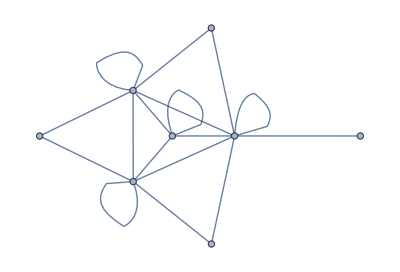

```mathematica
evenSubalgebraGraph[Cl[1,2]]=gaAlgebraMultiplicationTableGraph[Cl[1,2],gaGradesOnly->{{0},{2},{4}}]
```

```mathematica
allAlgebraGraph[Cl[2,0]]=gaAlgebraMultiplicationTableGraph[Cl[2,0]]
```

-Graphics-

Both graphs indeed look simirlarly, so try to find isomorphism

```mathematica
IsomorphicGraphQ[evenSubalgebraGraph[Cl[1,2]],allAlgebraGraph[Cl[2,0]]]
```

True

```mathematica
allIsomorphisms[Cl[1,2]->Cl[2,0]]=FindGraphIsomorphism[evenSubalgebraGraph[Cl[1,2]],allAlgebraGraph[Cl[2,0]],All]
```

{<|-1→-1,23120→12200,1→1,12120→1200,13120→2200,-12120→-1200,-13120→-2200,-23120→-12200|>,<|-1→-1,23120→12200,1→1,12120→2200,13120→1200,-12120→-2200,-13120→-1200,-23120→-12200|>}

```mathematica
Table[isomorphismRules[Cl[1,2]->Cl[2,0],n]=allIsomorphisms[Cl[1,2]->Cl[2,0]][[n]],{n,1,Length[allIsomorphisms[Cl[1,2]->Cl[2,0]]]}]
```

{<|-1→-1,23120→12200,1→1,12120→1200,13120→2200,-12120→-1200,-13120→-2200,-23120→-12200|>,<|-1→-1,23120→12200,1→1,12120→2200,13120→1200,-12120→-2200,-13120→-1200,-23120→-12200|>}

First detect isomorphisms without reflections. These are  No. 2

```mathematica
trueSubstitutionRules[Cl[1,2]->Cl[2,0],2]=DeleteCases[Normal[isomorphismRules[Cl[1,2]->Cl[2,0],2]],Rule[a_,a_]]
```

{23120→12200,12120→2200,13120→1200,-12120→-2200,-13120→-1200,-23120→-12200}

```mathematica
elementsForCheck[Cl[1,2]->Cl[2,0],2]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[2,0]])/.(Reverse/@Union[trueSubstitutionRules[Cl[1,2]->Cl[2,0],2]])
(checkResult[Cl[1,2]->Cl[2,0],2]=Outer[GeometricProduct,%,%])//TableForm
```

{1,13120,12120,23120}

1 | 13120 | 12120 | 23120
13120 | 1 | 23120 | 12120
12120 | -23120 | 1 | -13120
23120 | -12120 | 13120 | -1

```mathematica
checkAnswer[Cl[1,2]->Cl[2,0],2]=(checkResult[Cl[1,2]->Cl[2,0],2]/.trueSubstitutionRules[Cl[1,2]->Cl[2,0],2])
```

{{1,1200,2200,12200},{1200,1,12200,2200},{2200,-12200,1,-1200},{12200,-2200,1200,-1}}

And compare it with

```mathematica
mTableAll[Cl[2,0]]=gaAlgebraMultiplicationTable[Cl[2,0]]
```

| 1 | 1200 | 2200 | 12200
1 | 1 | 1200 | 2200 | 12200
1200 | 1200 | 1 | 12200 | 2200
2200 | 2200 | -12200 | 1 | -1200
12200 | 12200 | -2200 | 1200 | -1

```mathematica
mTableAll[Cl[2,0]][[1]]-checkAnswer[Cl[1,2]->Cl[2,0],2]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

First detect isomorphisms WITH reflections No. 1

```mathematica
trueSubstitutionRules[Cl[1,2]->Cl[2,0],1]=Rule@@@Flatten[{#,#/.{-a_,b_}:>{a,-b}}&/@(Transpose[MapAt[Map[If[gaGetGrade[#]==={2},#*(-1),#]&,#]&,Transpose[List@@@DeleteCases[Normal[isomorphismRules[Cl[1,2]->Cl[2,0],1]],Rule[a_,a_]|Rule[-a_,-b_]]],1]]),1]
```

{-23120→12200,23120→-12200,-12120→1200,12120→-1200,-13120→2200,13120→-2200}

```mathematica
elementsForCheck[Cl[1,2]->Cl[2,0],1]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[2,0]])/.(Reverse/@Union[trueSubstitutionRules[Cl[1,2]->Cl[2,0],1]])
(checkResult[Cl[1,2]->Cl[2,0],1]=Outer[GeometricProduct,%,%])//TableForm
```

{1,-12120,-13120,-23120}

1 | -12120 | -13120 | -23120
-12120 | 1 | -23120 | -13120
-13120 | 23120 | 1 | 12120
-23120 | 13120 | -12120 | -1

```mathematica
checkAnswer[Cl[1,2]->Cl[2,0],1]=(checkResult[Cl[1,2]->Cl[2,0],1]/.trueSubstitutionRules[Cl[1,2]->Cl[2,0],1])
```

{{1,1200,2200,12200},{1200,1,12200,2200},{2200,-12200,1,-1200},{12200,-2200,1200,-1}}

And compare it with

```mathematica
mTableAll[Cl[2,0]]=gaAlgebraMultiplicationTable[Cl[2,0]]
```

| 1 | 1200 | 2200 | 12200
1 | 1 | 1200 | 2200 | 12200
1200 | 1200 | 1 | 12200 | 2200
2200 | 2200 | -12200 | 1 | -1200
12200 | 12200 | -2200 | 1200 | -1

```mathematica
mTableAll[Cl[2,0]][[1]]-checkAnswer[Cl[1,2]->Cl[2,0],1]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

Cl[2,0] even is isomorphics to Cl[0,1]

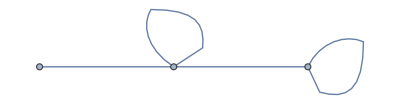

```mathematica
evenSubalgebraGraph[Cl[2,0]]=gaAlgebraMultiplicationTableGraph[Cl[2,0],gaGradesOnly->{{0},{2},{4}}]
```

```mathematica
allAlgebraGraph[Cl[0,1]]=gaAlgebraMultiplicationTableGraph[Cl[0,1]]
```

-Graphics-

Both graphs indeed look simirlarly, so try to find isomorphism

```mathematica
IsomorphicGraphQ[evenSubalgebraGraph[Cl[2,0]],allAlgebraGraph[Cl[0,1]]]
```

True

```mathematica
allIsomorphisms[Cl[2,0]->Cl[0,1]]=FindGraphIsomorphism[evenSubalgebraGraph[Cl[2,0]],allAlgebraGraph[Cl[0,1]],All]
```

{<|-1→-1,12200→1010,1→1|>}

```mathematica
isomorphismRules[Cl[2,0]->Cl[0,1],1]=allIsomorphisms[Cl[2,0]->Cl[0,1]][[1]]
```

<|-1→-1,12200→1010,1→1|>

In order to get exact match between multiplication tables using the first isomorphism rules we need to do is to change signs of all Cl[1,3] bivectors:

```mathematica
trueSubstitutionRules[Cl[2,0]->Cl[0,1],1]=Rule@@@Flatten[{#,#/.{-a_,b_}:>{a,-b}}&/@(Transpose[MapAt[Map[If[gaGetGrade[#]==={2},#*(-1),#]&,#]&,Transpose[List@@@DeleteCases[Normal[isomorphismRules[Cl[2,0]->Cl[0,1],1]],Rule[a_,a_]|Rule[-a_,-b_]]],1]]),1]
```

{-12200→1010,12200→-1010}

In order to check that Caylay tables are isomorphic, reorder bivectors and make them of appropriate sign

```mathematica
elementsForCheck[Cl[2,0]->Cl[0,1],1]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[0,1]])/.(Reverse/@Union[trueSubstitutionRules[Cl[2,0]->Cl[0,1],1]])
(checkResult[Cl[2,0]->Cl[0,1],1]=Outer[GeometricProduct,%,%])//TableForm
```

{1,-12200}

1 | -12200
-12200 | -1

```mathematica
checkAnswer[Cl[2,0]->Cl[0,1],1]=(checkResult[Cl[2,0]->Cl[0,1],1]/.trueSubstitutionRules[Cl[2,0]->Cl[0,1],1])
```

{{1,1010},{1010,-1}}

And compare it with

```mathematica
mTableAll[Cl[0,1]]=gaAlgebraMultiplicationTable[Cl[0,1]]
```

| 1 | 1010
1 | 1 | 1010
1010 | 1010 | -1

```mathematica
mTableAll[Cl[0,1]][[1]]-checkAnswer[Cl[2,0]->Cl[0,1],1]
```

{{0,0},{0,0}}

The second graph isomorphism yields Caylay table isomorphism, without bivector reflection !

```mathematica
trueSubstitutionRules[Cl[2,0]->Cl[0,1],2]=DeleteCases[Normal[isomorphismRules[Cl[2,0]->Cl[0,1],1]],Rule[a_,a_]]
```

{12200→1010}

```mathematica
elementsForCheck[Cl[2,0]->Cl[0,1],2]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[0,1]])/.(Reverse/@Union[trueSubstitutionRules[Cl[2,0]->Cl[0,1],2]])
(checkResult[Cl[2,0]->Cl[0,1],2]=Outer[GeometricProduct,%,%])//TableForm
```

{1,12200}

1 | 12200
12200 | -1

```mathematica
checkAnswer[Cl[2,0]->Cl[0,1],2]=(checkResult[Cl[2,0]->Cl[0,1],2]/.trueSubstitutionRules[Cl[2,0]->Cl[0,1],2])
```

{{1,1010},{1010,-1}}

And compare it with

```mathematica
mTableAll[Cl[0,1]]=gaAlgebraMultiplicationTable[Cl[0,1]]
```

| 1 | 1010
1 | 1 | 1010
1010 | 1010 | -1

```mathematica
mTableAll[Cl[0,1]][[1]]-checkAnswer[Cl[2,0]->Cl[0,1],2]
```

{{0,0},{0,0}}

Cl[1,3]->Cl[1,2]->Cl[2,0]->Cl[0,1]

Now relate Cl[2,0] to Cl[1,3] base elements. It is 2*2=4 variants possible

```mathematica
trueSubstitutionRules[Cl[1,2]->Cl[2,0],2]
```

{23120→12200,12120→2200,13120→1200,-12120→-2200,-13120→-1200,-23120→-12200}

```mathematica
trueSubstitutionRules[Cl[1,3]->Cl[1,2],2]
```

{23130→23120,24130→2120,34130→3120,1234130→123120,12130→12120,13130→13120,14130→1120,-12130→-12120,-13130→-13120,-14130→-1120,-23130→-23120,-24130→-2120,-34130→-3120,-1234130→-123120}

```mathematica
gaDefineInput[Cl[2,0]]
```

Running algebra is: gaRunningAlgebra= Cl[2, 0, 0]

No inversion in both chains

```mathematica
trueSubstitutionRules[Cl[1,2]->Cl[2,0],1]
```

{-23120→12200,23120→-12200,-12120→1200,12120→-1200,-13120→2200,13120→-2200}

```mathematica
trueSubstitutionRules[Cl[1,3]->Cl[1,2],1]
```

{-23130→3120,23130→-3120,-24130→2120,24130→-2120,-34130→23120,34130→-23120,1234130→123120,1234130→123120,-12130→1120,12130→-1120,-13130→13120,13130→-13120,-14130→12120,14130→-12120}

```mathematica
ReplaceAll[ReplaceAll[{𝕖[1],𝕖[2]},Reverse/@trueSubstitutionRules[Cl[1,2]->Cl[2,0],1]],Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[1,2],1]]
```

{14130,13130}

All possible pairs

```mathematica
Flatten[Table[ReplaceAll[ReplaceAll[{𝕖[1],𝕖[2]},Reverse/@trueSubstitutionRules[Cl[1,2]->Cl[2,0],cl20]],Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[1,2],cl12]],{cl20,Length[allIsomorphisms[Cl[1,2]->Cl[2,0]]]},{cl12,Length[allIsomorphisms[Cl[1,3]->Cl[1,2]]]}],1]
```

{{14130,13130},{-12130,-13130},{-13130,-14130},{13130,12130}}

Now relate Cl[0,1] to Cl[1,3] base elements. It is 2*2*2=8 variants possible

```mathematica
trueSubstitutionRules[Cl[2,0]->Cl[0,1],2]
```

{12200→1010}

```mathematica
trueSubstitutionRules[Cl[1,2]->Cl[2,0],2]
```

{23120→12200,12120→2200,13120→1200,-12120→-2200,-13120→-1200,-23120→-12200}

```mathematica
trueSubstitutionRules[Cl[1,3]->Cl[1,2],2]
```

{23130→23120,24130→2120,34130→3120,1234130→123120,12130→12120,13130→13120,14130→1120,-12130→-12120,-13130→-13120,-14130→-1120,-23130→-23120,-24130→-2120,-34130→-3120,-1234130→-123120}

```mathematica
gaDefineInput[Cl[2,0]]
```

Running algebra is: gaRunningAlgebra= Cl[2, 0, 0]

No inversion in both chains

```mathematica
trueSubstitutionRules[Cl[1,2]->Cl[2,0],1]
```

{-23120→12200,23120→-12200,-12120→1200,12120→-1200,-13120→2200,13120→-2200}

```mathematica
trueSubstitutionRules[Cl[1,3]->Cl[1,2],1]
```

{-23130→3120,23130→-3120,-24130→2120,24130→-2120,-34130→23120,34130→-23120,1234130→123120,1234130→123120,-12130→1120,12130→-1120,-13130→13120,13130→-13120,-14130→12120,14130→-12120}

```mathematica
ReplaceAll[ReplaceAll[{𝕖[1],𝕖[2]},Reverse/@trueSubstitutionRules[Cl[1,2]->Cl[2,0],1]],Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[1,2],1]]
```

{14130,13130}

All possible pairs

```mathematica
Flatten[Table[ReplaceAll[ReplaceAll[{𝕖[1],𝕖[2]},Reverse/@trueSubstitutionRules[Cl[1,2]->Cl[2,0],cl20]],Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[1,2],cl12]],{cl20,Length[allIsomorphisms[Cl[1,2]->Cl[2,0]]]},{cl12,Length[allIsomorphisms[Cl[1,3]->Cl[1,2]]]}],1]
```

{{14130,13130},{-12130,-13130},{-13130,-14130},{13130,12130}}

All possible pairs for Cl[0,1]

```mathematica
gaDefineInput[Cl[0,1]]
```

Running algebra is: gaRunningAlgebra= Cl[0, 1, 0]

```mathematica
Flatten[Table[ReplaceAll[ReplaceAll[{𝕖[1]},Reverse/@trueSubstitutionRules[Cl[2,0]->Cl[0,1],cl01]],Reverse/@trueSubstitutionRules[Cl[1,2]->Cl[2,0],cl20]],{cl01,Length[allIsomorphisms[Cl[2,0]->Cl[0,1]]]},{cl20,Length[allIsomorphisms[Cl[1,2]->Cl[2,0]]]}],1]
```

{{23120},{-23120}}

```mathematica
Flatten[Table[ReplaceAll[ReplaceAll[ReplaceAll[{𝕖[1]},Reverse/@trueSubstitutionRules[Cl[2,0]->Cl[0,1],cl01]],Reverse/@trueSubstitutionRules[Cl[1,2]->Cl[2,0],cl20]],Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[1,2],cl12]],{cl01,Length[allIsomorphisms[Cl[2,0]->Cl[0,1]]]},{cl20,Length[allIsomorphisms[Cl[1,2]->Cl[2,0]]]},{cl12,Length[allIsomorphisms[Cl[1,3]->Cl[1,2]]]}],2]
```

{{-34130},{23130},{34130},{-23130}}

Cl[1,2] even is isomorphics to Cl[1,1]

```mathematica
evenSubalgebraGraph[Cl[1,2]]=gaAlgebraMultiplicationTableGraph[Cl[1,2],gaGradesOnly->{{0},{2},{4}}]
```

-Graphics-

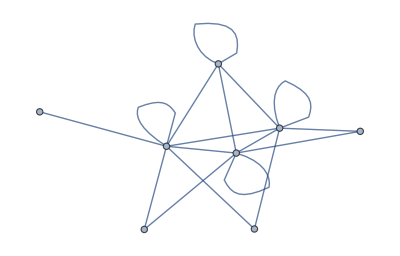

```mathematica
allAlgebraGraph[Cl[1,1]]=gaAlgebraMultiplicationTableGraph[Cl[1,1]]
```

Both graphs indeed look simirlarly, so try to find isomorphism

```mathematica
IsomorphicGraphQ[evenSubalgebraGraph[Cl[1,2]],allAlgebraGraph[Cl[1,1]]]
```

True

```mathematica
allIsomorphisms[Cl[1,2]->Cl[1,1]]=FindGraphIsomorphism[evenSubalgebraGraph[Cl[1,2]],allAlgebraGraph[Cl[1,1]],All]
```

{<|-1→-1,23120→2110,1→1,12120→1110,13120→12110,-12120→-1110,-13120→-12110,-23120→-2110|>,<|-1→-1,23120→2110,1→1,12120→12110,13120→1110,-12120→-12110,-13120→-1110,-23120→-2110|>}

```mathematica
Table[isomorphismRules[Cl[1,2]->Cl[1,1],n]=allIsomorphisms[Cl[1,2]->Cl[1,1]][[n]],{n,1,Length[allIsomorphisms[Cl[1,2]->Cl[1,1]]]}]
```

{<|-1→-1,23120→2110,1→1,12120→1110,13120→12110,-12120→-1110,-13120→-12110,-23120→-2110|>,<|-1→-1,23120→2110,1→1,12120→12110,13120→1110,-12120→-12110,-13120→-1110,-23120→-2110|>}

First detect isomorphisms without reflections. These are  No. 2

```mathematica
trueSubstitutionRules[Cl[1,2]->Cl[1,1],2]=DeleteCases[Normal[isomorphismRules[Cl[1,2]->Cl[1,1],2]],Rule[a_,a_]]
```

{23120→2110,12120→12110,13120→1110,-12120→-12110,-13120→-1110,-23120→-2110}

```mathematica
elementsForCheck[Cl[1,2]->Cl[1,1],2]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[1,1]])/.(Reverse/@Union[trueSubstitutionRules[Cl[1,2]->Cl[1,1],2]])
(checkResult[Cl[1,2]->Cl[1,1],2]=Outer[GeometricProduct,%,%])//TableForm
```

{1,13120,23120,12120}

1 | 13120 | 23120 | 12120
13120 | 1 | 12120 | 23120
23120 | -12120 | -1 | 13120
12120 | -23120 | -13120 | 1

```mathematica
checkAnswer[Cl[1,2]->Cl[1,1],2]=(checkResult[Cl[1,2]->Cl[1,1],2]/.trueSubstitutionRules[Cl[1,2]->Cl[1,1],2])
```

{{1,1110,2110,12110},{1110,1,12110,2110},{2110,-12110,-1,1110},{12110,-2110,-1110,1}}

And compare it with

```mathematica
mTableAll[Cl[1,1]]=gaAlgebraMultiplicationTable[Cl[1,1]]
```

| 1 | 1110 | 2110 | 12110
1 | 1 | 1110 | 2110 | 12110
1110 | 1110 | 1 | 12110 | 2110
2110 | 2110 | -12110 | -1 | 1110
12110 | 12110 | -2110 | -1110 | 1

```mathematica
mTableAll[Cl[1,1]][[1]]-checkAnswer[Cl[1,2]->Cl[1,1],2]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

First detect isomorphisms WITH reflections No. 1

```mathematica
trueSubstitutionRules[Cl[1,2]->Cl[1,1],1]=Rule@@@Flatten[{#,#/.{-a_,b_}:>{a,-b}}&/@(Transpose[MapAt[Map[If[gaGetGrade[#]==={2},#*(-1),#]&,#]&,Transpose[List@@@DeleteCases[Normal[isomorphismRules[Cl[1,2]->Cl[1,1],1]],Rule[a_,a_]|Rule[-a_,-b_]]],1]]),1]
```

{-23120→2110,23120→-2110,-12120→1110,12120→-1110,-13120→12110,13120→-12110}

```mathematica
elementsForCheck[Cl[1,2]->Cl[1,1],1]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[1,1]])/.(Reverse/@Union[trueSubstitutionRules[Cl[1,2]->Cl[1,1],1]])
(checkResult[Cl[1,2]->Cl[1,1],1]=Outer[GeometricProduct,%,%])//TableForm
```

{1,-12120,-23120,-13120}

1 | -12120 | -23120 | -13120
-12120 | 1 | -13120 | -23120
-23120 | 13120 | -1 | -12120
-13120 | 23120 | 12120 | 1

```mathematica
checkAnswer[Cl[1,2]->Cl[1,1],1]=(checkResult[Cl[1,2]->Cl[1,1],1]/.trueSubstitutionRules[Cl[1,2]->Cl[1,1],1])
```

{{1,1110,2110,12110},{1110,1,12110,2110},{2110,-12110,-1,1110},{12110,-2110,-1110,1}}

And compare it with

```mathematica
mTableAll[Cl[1,1]]=gaAlgebraMultiplicationTable[Cl[1,1]]
```

| 1 | 1110 | 2110 | 12110
1 | 1 | 1110 | 2110 | 12110
1110 | 1110 | 1 | 12110 | 2110
2110 | 2110 | -12110 | -1 | 1110
12110 | 12110 | -2110 | -1110 | 1

```mathematica
mTableAll[Cl[1,1]][[1]]-checkAnswer[Cl[1,2]->Cl[1,1],1]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

Cl[1,1] even is isomorphics to Cl[1,0]

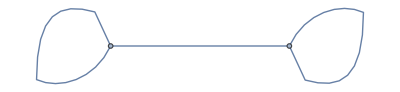

```mathematica
evenSubalgebraGraph[Cl[1,1]]=gaAlgebraMultiplicationTableGraph[Cl[1,1],gaGradesOnly->{{0},{2},{4}}]
```

```mathematica
allAlgebraGraph[Cl[1,0]]=gaAlgebraMultiplicationTableGraph[Cl[1,0]]
```

-Graphics-

Both graphs indeed look simirlarly, so try to find isomorphism

```mathematica
IsomorphicGraphQ[evenSubalgebraGraph[Cl[1,1]],allAlgebraGraph[Cl[1,0]]]
```

True

```mathematica
allIsomorphisms[Cl[1,1]->Cl[1,0]]=FindGraphIsomorphism[evenSubalgebraGraph[Cl[1,1]],allAlgebraGraph[Cl[1,0]],All]
```

{<|1→1,12110→1100|>,<|1→1100,12110→1|>}

```mathematica
Table[isomorphismRules[Cl[1,1]->Cl[1,0],n]=allIsomorphisms[Cl[1,1]->Cl[1,0]][[n]],{n,1,Length[allIsomorphisms[Cl[1,1]->Cl[1,0]]]}]
```

{<|1→1,12110→1100|>,<|1→1100,12110→1|>}

First detect isomorphisms with reflections. These are  No. 2

```mathematica
trueSubstitutionRules[Cl[1,1]->Cl[1,0],2]=Rule@@@Flatten[{#,#/.{-a_,b_}:>{a,-b}}&/@(Transpose[MapAt[Map[If[gaGetGrade[#]==={2},#*(-1),#]&,#]&,Transpose[List@@@DeleteCases[Normal[isomorphismRules[Cl[1,1]->Cl[1,0],1]],Rule[a_,a_]|Rule[-a_,-b_]]],1]]),1]
```

{-12110→1100,12110→-1100}

```mathematica
elementsForCheck[Cl[1,1]->Cl[1,0],2]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[1,0]])/.(Reverse/@Union[trueSubstitutionRules[Cl[1,1]->Cl[1,0],2]])
(checkResult[Cl[1,1]->Cl[1,0],2]=Outer[GeometricProduct,%,%])//TableForm
```

{1,-12110}

1 | -12110
-12110 | 1

```mathematica
checkAnswer[Cl[1,1]->Cl[1,0],2]=(checkResult[Cl[1,1]->Cl[1,0],2]/.trueSubstitutionRules[Cl[1,1]->Cl[1,0],2])
```

{{1,1100},{1100,1}}

And compare it with

```mathematica
mTableAll[Cl[1,0]]=gaAlgebraMultiplicationTable[Cl[1,0]]
```

| 1 | 1100
1 | 1 | 1100
1100 | 1100 | 1

```mathematica
mTableAll[Cl[1,0]][[1]]-checkAnswer[Cl[1,1]->Cl[1,0],2]
```

{{0,0},{0,0}}

First detect isomorphisms WITHOUT reflections No. 1

```mathematica
trueSubstitutionRules[Cl[1,1]->Cl[1,0],1]=DeleteCases[Normal[isomorphismRules[Cl[1,1]->Cl[1,0],1]],Rule[a_,a_]]
```

{12110→1100}

```mathematica
elementsForCheck[Cl[1,1]->Cl[1,0],1]=(List@@gaGeneralMultivector[Unitize[#+1]&,Cl[1,0]])/.(Reverse/@Union[trueSubstitutionRules[Cl[1,1]->Cl[1,0],1]])
(checkResult[Cl[1,1]->Cl[1,0],1]=Outer[GeometricProduct,%,%])//TableForm
```

{1,12110}

1 | 12110
12110 | 1

```mathematica
checkAnswer[Cl[1,1]->Cl[1,0],1]=(checkResult[Cl[1,1]->Cl[1,0],1]/.trueSubstitutionRules[Cl[1,1]->Cl[1,0],1])
```

{{1,1100},{1100,1}}

And compare it with

```mathematica
mTableAll[Cl[1,0]]=gaAlgebraMultiplicationTable[Cl[1,0]]
```

| 1 | 1100
1 | 1 | 1100
1100 | 1100 | 1

```mathematica
mTableAll[Cl[1,0]][[1]]-checkAnswer[Cl[1,1]->Cl[1,0],1]
```

{{0,0},{0,0}}

Cl[1,3]->Cl[1,2]->Cl[1,1]->Cl[1,0]

Now relate Cl[1,1] to Cl[1,3] base elements. It is 2*2=4 variants possible

```mathematica
trueSubstitutionRules[Cl[1,2]->Cl[1,1],2]
```

{23120→2110,12120→12110,13120→1110,-12120→-12110,-13120→-1110,-23120→-2110}

```mathematica
trueSubstitutionRules[Cl[1,3]->Cl[1,2],1]
```

{-23130→3120,23130→-3120,-24130→2120,24130→-2120,-34130→23120,34130→-23120,1234130→123120,1234130→123120,-12130→1120,12130→-1120,-13130→13120,13130→-13120,-14130→12120,14130→-12120}

No inversion in both chains

```mathematica
trueSubstitutionRules[Cl[1,2]->Cl[1,1],1]
```

{-23120→2110,23120→-2110,-12120→1110,12120→-1110,-13120→12110,13120→-12110}

```mathematica
trueSubstitutionRules[Cl[1,3]->Cl[1,2],1]
```

{-23130→3120,23130→-3120,-24130→2120,24130→-2120,-34130→23120,34130→-23120,1234130→123120,1234130→123120,-12130→1120,12130→-1120,-13130→13120,13130→-13120,-14130→12120,14130→-12120}

All possible pairs

```mathematica
gaDefineInput[Cl[1,1]]
```

Running algebra is: gaRunningAlgebra= Cl[1, 1, 0]

```mathematica
Flatten[Table[ReplaceAll[ReplaceAll[{𝕖[1],𝕖[2]},Reverse/@trueSubstitutionRules[Cl[1,2]->Cl[1,1],cl11]],Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[1,2],cl12]],{cl11,Length[allIsomorphisms[Cl[1,2]->Cl[1,1]]]},{cl12,Length[allIsomorphisms[Cl[1,3]->Cl[1,2]]]}],1]
```

{{14130,34130},{-12130,-23130},{-13130,-34130},{13130,23130}}

Now relate Cl[1,0] to Cl[1,2] base elements. It is 2*2*2=8 variants possible

```mathematica
trueSubstitutionRules[Cl[1,1]->Cl[1,0],2]
```

{-12110→1100,12110→-1100}

```mathematica
trueSubstitutionRules[Cl[1,2]->Cl[1,1],2]
```

{23120→2110,12120→12110,13120→1110,-12120→-12110,-13120→-1110,-23120→-2110}

```mathematica
trueSubstitutionRules[Cl[1,3]->Cl[1,2],2]
```

{23130→23120,24130→2120,34130→3120,1234130→123120,12130→12120,13130→13120,14130→1120,-12130→-12120,-13130→-13120,-14130→-1120,-23130→-23120,-24130→-2120,-34130→-3120,-1234130→-123120}

```mathematica
gaDefineInput[Cl[1,0]]
```

Running algebra is: gaRunningAlgebra= Cl[1, 0, 0]

All possible pairs

```mathematica
Length[allIsomorphisms[Cl[1,1]->Cl[1,0]]]*Length[allIsomorphisms[Cl[1,2]->Cl[1,1]]]
```

4

```mathematica
Flatten[Table[ReplaceAll[ReplaceAll[{𝕖[1]},Reverse/@trueSubstitutionRules[Cl[1,1]->Cl[1,0],cl10]],Reverse/@trueSubstitutionRules[Cl[1,2]->Cl[1,1],cl11]],{cl10,Length[allIsomorphisms[Cl[1,1]->Cl[1,0]]]},{cl11,Length[allIsomorphisms[Cl[1,2]->Cl[1,1]]]}],1]
```

{{-13120},{12120},{13120},{-12120}}

Now relate Cl[1,0] to Cl[1,3] base elements. It is 2*2*2=8 variants possible

```mathematica
Length[allIsomorphisms[Cl[1,1]->Cl[1,0]]]*Length[allIsomorphisms[Cl[1,2]->Cl[1,1]]]*Length[allIsomorphisms[Cl[1,3]->Cl[1,2]]]
```

8

All possible pairs

```mathematica
Flatten[Table[ReplaceAll[ReplaceAll[ReplaceAll[{𝕖[1]},Reverse/@trueSubstitutionRules[Cl[1,1]->Cl[1,0],cl10]],Reverse/@trueSubstitutionRules[Cl[1,2]->Cl[1,1],cl11]],Reverse/@trueSubstitutionRules[Cl[1,3]->Cl[1,2],cl12]],{cl10,Length[allIsomorphisms[Cl[1,1]->Cl[1,0]]]},{cl11,Length[allIsomorphisms[Cl[1,2]->Cl[1,1]]]},{cl12,Length[allIsomorphisms[Cl[1,3]->Cl[1,2]]]}],2]//Union
```

{{-12130},{12130},{-13130},{13130},{-14130},{14130}}

Cl[6,0] even is isomorphics to Cl[0,5]

```mathematica
{gaDefineOrthonormalBase[Cl[6,0],Quiet->True],gaDefineOrthonormalBase[Cl[0,5],Quiet->True]}
```

Base vectors of 600are stored in variable gaOrthonormalBase[Cl[6, 0, 0]].

Base vectors of 050are stored in variable gaOrthonormalBase[Cl[0, 5, 0]].

{{1,1600,2600,3600,4600,5600,6600,12600,13600,14600,15600,16600,23600,24600,25600,26600,34600,35600,36600,45600,46600,56600,123600,124600,125600,126600,134600,135600,136600,145600,146600,156600,234600,235600,236600,245600,246600,256600,345600,346600,356600,456600,1234600,1235600,1236600,1245600,1246600,1256600,1345600,1346600,1356600,1456600,2345600,2346600,2356600,2456600,3456600,12345600,12346600,12356600,12456600,13456600,23456600,123456600},{1,1050,2050,3050,4050,5050,12050,13050,14050,15050,23050,24050,25050,34050,35050,45050,123050,124050,125050,134050,135050,145050,234050,235050,245050,345050,1234050,1235050,1245050,1345050,2345050,12345050}}

```mathematica
evenSubalgebraGraph[Cl[6,0]]=gaAlgebraMultiplicationTableGraph[Cl[6,0],gaGradesOnly->{{0},{2},{4},{6}}];
```

```mathematica
allAlgebraGraph[Cl[0,5]]=gaAlgebraMultiplicationTableGraph[Cl[0,5]];
```

```mathematica
IsomorphicGraphQ[evenSubalgebraGraph[Cl[6,0]],allAlgebraGraph[Cl[0,5]]]
```

True

```mathematica
allIsomorphisms[Cl[6,0]->Cl[0,5]]=FindGraphIsomorphism[evenSubalgebraGraph[Cl[6,0]],allAlgebraGraph[Cl[0,5]],All]
```

{<|-1→-1,12600→1050,13600→2050,14600→3050,15600→4050,16600→5050,23600→12050,24600→13050,25600→14050,26600→15050,34600→23050,35600→24050,36600→25050,45600→34050,46600→35050,56600→45050,123456600→12345050,1→1,1234600→123050,1235600→124050,1236600→125050,1245600→134050,1246600→135050,1256600→145050,1345600→234050,1346600→235050,1356600→245050,1456600→345050,2345600→1234050,2346600→1235050,2356600→1245050,2456600→1345050,3456600→2345050,-12600→-1050,-13600→-2050,-14600→-3050,-15600→-4050,-16600→-5050,-23600→-12050,-24600→-13050,-25600→-14050,-26600→-15050,-34600→-23050,-35600→-24050,-36600→-25050,-45600→-34050,-46600→-35050,-56600→-45050,-1345600→-234050,-1346600→-235050,-1356600→-245050,-1456600→-345050,-2345600→-1234050,-2346600→-1235050,-2356600→-1245050,-2456600→-1345050,-3456600→-2345050,-1234600→-123050,-1235600→-124050,-1236600→-125050,-1245600→-134050,-1246600→-135050,-1256600→-145050,-123456600→-12345050|>,<|-1→-1,12600→1050,13600→15050,14600→14050,15600→13050,16600→12050,23600→5050,24600→4050,25600→3050,26600→2050,34600→45050,35600→35050,36600→25050,45600→34050,46600→24050,56600→23050,123456600→12345050,1→1,1234600→145050,1235600→135050,1236600→125050,1245600→134050,1246600→124050,1256600→123050,1345600→1345050,1346600→1245050,1356600→1235050,1456600→1234050,2345600→345050,2346600→245050,2356600→235050,2456600→234050,3456600→2345050,-12600→-1050,-13600→-15050,-14600→-14050,-15600→-13050,-16600→-12050,-23600→-5050,-24600→-4050,-25600→-3050,-26600→-2050,-34600→-45050,-35600→-35050,-36600→-25050,-45600→-34050,-46600→-24050,-56600→-23050,-1345600→-1345050,-1346600→-1245050,-1356600→-1235050,-1456600→-1234050,-2345600→-345050,-2346600→-245050,-2356600→-235050,-2456600→-234050,-3456600→-2345050,-1234600→-145050,-1235600→-135050,-1236600→-125050,-1245600→-134050,-1246600→-124050,-1256600→-123050,-123456600→-12345050|>,<|-1→-1,12600→5050,13600→4050,14600→3050,15600→2050,16600→1050,23600→45050,24600→35050,25600→25050,26600→15050,34600→34050,35600→24050,36600→14050,45600→23050,46600→13050,56600→12050,123456600→12345050,1→1,1234600→345050,1235600→245050,1236600→145050,1245600→235050,1246600→135050,1256600→125050,1345600→234050,1346600→134050,1356600→124050,1456600→123050,2345600→2345050,2346600→1345050,2356600→1245050,2456600→1235050,3456600→1234050,-12600→-5050,-13600→-4050,-14600→-3050,-15600→-2050,-16600→-1050,-23600→-45050,-24600→-35050,-25600→-25050,-26600→-15050,-34600→-34050,-35600→-24050,-36600→-14050,-45600→-23050,-46600→-13050,-56600→-12050,-1345600→-234050,-1346600→-134050,-1356600→-124050,-1456600→-123050,-2345600→-2345050,-2346600→-1345050,-2356600→-1245050,-2456600→-1235050,-3456600→-1234050,-1234600→-345050,-1235600→-245050,-1236600→-145050,-1245600→-235050,-1246600→-135050,-1256600→-125050,-123456600→-12345050|>,<|-1→-1,12600→5050,13600→15050,14600→25050,15600→35050,16600→45050,23600→1050,24600→2050,25600→3050,26600→4050,34600→12050,35600→13050,36600→14050,45600→23050,46600→24050,56600→34050,123456600→12345050,1→1,1234600→125050,1235600→135050,1236600→145050,1245600→235050,1246600→245050,1256600→345050,1345600→1235050,1346600→1245050,1356600→1345050,1456600→2345050,2345600→123050,2346600→124050,2356600→134050,2456600→234050,3456600→1234050,-12600→-5050,-13600→-15050,-14600→-25050,-15600→-35050,-16600→-45050,-23600→-1050,-24600→-2050,-25600→-3050,-26600→-4050,-34600→-12050,-35600→-13050,-36600→-14050,-45600→-23050,-46600→-24050,-56600→-34050,-1345600→-1235050,-1346600→-1245050,-1356600→-1345050,-1456600→-2345050,-2345600→-123050,-2346600→-124050,-2356600→-134050,-2456600→-234050,-3456600→-1234050,-1234600→-125050,-1235600→-135050,-1236600→-145050,-1245600→-235050,-1246600→-245050,-1256600→-345050,-123456600→-12345050|>,<|-1→-1,12600→12050,13600→2050,14600→25050,15600→24050,16600→23050,23600→1050,24600→15050,25600→14050,26600→13050,34600→5050,35600→4050,36600→3050,45600→45050,46600→35050,56600→34050,123456600→12345050,1→1,1234600→125050,1235600→124050,1236600→123050,1245600→1245050,1246600→1235050,1256600→1234050,1345600→245050,1346600→235050,1356600→234050,1456600→2345050,2345600→145050,2346600→135050,2356600→134050,2456600→1345050,3456600→345050,-12600→-12050,-13600→-2050,-14600→-25050,-15600→-24050,-16600→-23050,-23600→-1050,-24600→-15050,-25600→-14050,-26600→-13050,-34600→-5050,-35600→-4050,-36600→-3050,-45600→-45050,-46600→-35050,-56600→-34050,-1345600→-245050,-1346600→-235050,-1356600→-234050,-1456600→-2345050,-2345600→-145050,-2346600→-135050,-2356600→-134050,-2456600→-1345050,-3456600→-345050,-1234600→-125050,-1235600→-124050,-1236600→-123050,-1245600→-1245050,-1246600→-1235050,-1256600→-1234050,-123456600→-12345050|>,<|-1→-1,12600→12050,13600→13050,14600→14050,15600→15050,16600→1050,23600→23050,24600→24050,25600→25050,26600→2050,34600→34050,35600→35050,36600→3050,45600→45050,46600→4050,56600→5050,123456600→12345050,1→1,1234600→1234050,1235600→1235050,1236600→123050,1245600→1245050,1246600→124050,1256600→125050,1345600→1345050,1346600→134050,1356600→135050,1456600→145050,2345600→2345050,2346600→234050,2356600→235050,2456600→245050,3456600→345050,-12600→-12050,-13600→-13050,-14600→-14050,-15600→-15050,-16600→-1050,-23600→-23050,-24600→-24050,-25600→-25050,-26600→-2050,-34600→-34050,-35600→-35050,-36600→-3050,-45600→-45050,-46600→-4050,-56600→-5050,-1345600→-1345050,-1346600→-134050,-1356600→-135050,-1456600→-145050,-2345600→-2345050,-2346600→-234050,-2356600→-235050,-2456600→-245050,-3456600→-345050,-1234600→-1234050,-1235600→-1235050,-1236600→-123050,-1245600→-1245050,-1246600→-124050,-1256600→-125050,-123456600→-12345050|>,<|-1→-1,12600→23050,13600→13050,14600→3050,15600→35050,16600→34050,23600→12050,24600→2050,25600→25050,26600→24050,34600→1050,35600→15050,36600→14050,45600→5050,46600→4050,56600→45050,123456600→12345050,1→1,1234600→123050,1235600→1235050,1236600→1234050,1245600→235050,1246600→234050,1256600→2345050,1345600→135050,1346600→134050,1356600→1345050,1456600→345050,2345600→125050,2346600→124050,2356600→1245050,2456600→245050,3456600→145050,-12600→-23050,-13600→-13050,-14600→-3050,-15600→-35050,-16600→-34050,-23600→-12050,-24600→-2050,-25600→-25050,-26600→-24050,-34600→-1050,-35600→-15050,-36600→-14050,-45600→-5050,-46600→-4050,-56600→-45050,-1345600→-135050,-1346600→-134050,-1356600→-1345050,-1456600→-345050,-2345600→-125050,-2346600→-124050,-2356600→-1245050,-2456600→-245050,-3456600→-145050,-1234600→-123050,-1235600→-1235050,-1236600→-1234050,-1245600→-235050,-1246600→-234050,-1256600→-2345050,-123456600→-12345050|>,<|-1→-1,12600→23050,13600→24050,14600→25050,15600→2050,16600→12050,23600→34050,24600→35050,25600→3050,26600→13050,34600→45050,35600→4050,36600→14050,45600→5050,46600→15050,56600→1050,123456600→12345050,1→1,1234600→2345050,1235600→234050,1236600→1234050,1245600→235050,1246600→1235050,1256600→123050,1345600→245050,1346600→1245050,1356600→124050,1456600→125050,2345600→345050,2346600→1345050,2356600→134050,2456600→135050,3456600→145050,-12600→-23050,-13600→-24050,-14600→-25050,-15600→-2050,-16600→-12050,-23600→-34050,-24600→-35050,-25600→-3050,-26600→-13050,-34600→-45050,-35600→-4050,-36600→-14050,-45600→-5050,-46600→-15050,-56600→-1050,-1345600→-245050,-1346600→-1245050,-1356600→-124050,-1456600→-125050,-2345600→-345050,-2346600→-1345050,-2356600→-134050,-2456600→-135050,-3456600→-145050,-1234600→-2345050,-1235600→-234050,-1236600→-1234050,-1245600→-235050,-1246600→-1235050,-1256600→-123050,-123456600→-12345050|>,<|-1→-1,12600→34050,13600→24050,14600→14050,15600→4050,16600→45050,23600→23050,24600→13050,25600→3050,26600→35050,34600→12050,35600→2050,36600→25050,45600→1050,46600→15050,56600→5050,123456600→12345050,1→1,1234600→1234050,1235600→234050,1236600→2345050,1245600→134050,1246600→1345050,1256600→345050,1345600→124050,1346600→1245050,1356600→245050,1456600→145050,2345600→123050,2346600→1235050,2356600→235050,2456600→135050,3456600→125050,-12600→-34050,-13600→-24050,-14600→-14050,-15600→-4050,-16600→-45050,-23600→-23050,-24600→-13050,-25600→-3050,-26600→-35050,-34600→-12050,-35600→-2050,-36600→-25050,-45600→-1050,-46600→-15050,-56600→-5050,-1345600→-124050,-1346600→-1245050,-1356600→-245050,-1456600→-145050,-2345600→-123050,-2346600→-1235050,-2356600→-235050,-2456600→-135050,-3456600→-125050,-1234600→-1234050,-1235600→-234050,-1236600→-2345050,-1245600→-134050,-1246600→-1345050,-1256600→-345050,-123456600→-12345050|>,<|-1→-1,12600→34050,13600→35050,14600→3050,15600→13050,16600→23050,23600→45050,24600→4050,25600→14050,26600→24050,34600→5050,35600→15050,36600→25050,45600→1050,46600→2050,56600→12050,123456600→12345050,1→1,1234600→345050,1235600→1345050,1236600→2345050,1245600→134050,1246600→234050,1256600→1234050,1345600→135050,1346600→235050,1356600→1235050,1456600→123050,2345600→145050,2346600→245050,2356600→1245050,2456600→124050,3456600→125050,-12600→-34050,-13600→-35050,-14600→-3050,-15600→-13050,-16600→-23050,-23600→-45050,-24600→-4050,-25600→-14050,-26600→-24050,-34600→-5050,-35600→-15050,-36600→-25050,-45600→-1050,-46600→-2050,-56600→-12050,-1345600→-135050,-1346600→-235050,-1356600→-1235050,-1456600→-123050,-2345600→-145050,-2346600→-245050,-2356600→-1245050,-2456600→-124050,-3456600→-125050,-1234600→-345050,-1235600→-1345050,-1236600→-2345050,-1245600→-134050,-1246600→-234050,-1256600→-1234050,-123456600→-12345050|>,<|-1→-1,12600→45050,13600→4050,14600→14050,15600→24050,16600→34050,23600→5050,24600→15050,25600→25050,26600→35050,34600→1050,35600→2050,36600→3050,45600→12050,46600→13050,56600→23050,123456600→12345050,1→1,1234600→145050,1235600→245050,1236600→345050,1245600→1245050,1246600→1345050,1256600→2345050,1345600→124050,1346600→134050,1356600→234050,1456600→1234050,2345600→125050,2346600→135050,2356600→235050,2456600→1235050,3456600→123050,-12600→-45050,-13600→-4050,-14600→-14050,-15600→-24050,-16600→-34050,-23600→-5050,-24600→-15050,-25600→-25050,-26600→-35050,-34600→-1050,-35600→-2050,-36600→-3050,-45600→-12050,-46600→-13050,-56600→-23050,-1345600→-124050,-1346600→-134050,-1356600→-234050,-1456600→-1234050,-2345600→-125050,-2346600→-135050,-2356600→-235050,-2456600→-1235050,-3456600→-123050,-1234600→-145050,-1235600→-245050,-1236600→-345050,-1245600→-1245050,-1246600→-1345050,-1256600→-2345050,-123456600→-12345050|>,<|-1→-1,12600→45050,13600→35050,14600→25050,15600→15050,16600→5050,23600→34050,24600→24050,25600→14050,26600→4050,34600→23050,35600→13050,36600→3050,45600→12050,46600→2050,56600→1050,123456600→12345050,1→1,1234600→2345050,1235600→1345050,1236600→345050,1245600→1245050,1246600→245050,1256600→145050,1345600→1235050,1346600→235050,1356600→135050,1456600→125050,2345600→1234050,2346600→234050,2356600→134050,2456600→124050,3456600→123050,-12600→-45050,-13600→-35050,-14600→-25050,-15600→-15050,-16600→-5050,-23600→-34050,-24600→-24050,-25600→-14050,-26600→-4050,-34600→-23050,-35600→-13050,-36600→-3050,-45600→-12050,-46600→-2050,-56600→-1050,-1345600→-1235050,-1346600→-235050,-1356600→-135050,-1456600→-125050,-2345600→-1234050,-2346600→-234050,-2356600→-134050,-2456600→-124050,-3456600→-123050,-1234600→-2345050,-1235600→-1345050,-1236600→-345050,-1245600→-1245050,-1246600→-245050,-1256600→-145050,-123456600→-12345050|>}

```mathematica
Table[isomorphismRules[Cl[6,0]->Cl[0,5],n]=allIsomorphisms[Cl[6,0]->Cl[0,5]][[n]],{n,1,Length[allIsomorphisms[Cl[6,0]->Cl[0,5]]]}];
```

We see that in all isomorphisms grades are replaced in the same way below

```mathematica
isomorphismRules[Cl[6,0]->Cl[0,5],1]
```

<|-1→-1,12600→1050,13600→2050,14600→3050,15600→4050,16600→5050,23600→12050,24600→13050,25600→14050,26600→15050,34600→23050,35600→24050,36600→25050,45600→34050,46600→35050,56600→45050,123456600→12345050,1→1,1234600→123050,1235600→124050,1236600→125050,1245600→134050,1246600→135050,1256600→145050,1345600→234050,1346600→235050,1356600→245050,1456600→345050,2345600→1234050,2346600→1235050,2356600→1245050,2456600→1345050,3456600→2345050,-12600→-1050,-13600→-2050,-14600→-3050,-15600→-4050,-16600→-5050,-23600→-12050,-24600→-13050,-25600→-14050,-26600→-15050,-34600→-23050,-35600→-24050,-36600→-25050,-45600→-34050,-46600→-35050,-56600→-45050,-1345600→-234050,-1346600→-235050,-1356600→-245050,-1456600→-345050,-2345600→-1234050,-2346600→-1235050,-2356600→-1245050,-2456600→-1345050,-3456600→-2345050,-1234600→-123050,-1235600→-124050,-1236600→-125050,-1245600→-134050,-1246600→-135050,-1256600→-145050,-123456600→-12345050|>

```mathematica
Table[Normal[isomorphismRules[Cl[6,0]->Cl[0,5],n]]/.{Rule[a_,b_]:>Rule[gaGetGrade[a],gaGetGrade[b]]}//Union,{n,1,Length[allIsomorphisms[Cl[6,0]->Cl[0,5]]]}]//Union
```

{{{0}→{0},{2}→{1},{2}→{2},{4}→{3},{4}→{4},{6}→{5}}}

Cl[7,0] even is isomorphics to Cl[0,6]

```mathematica
{gaDefineOrthonormalBase[Cl[7,0],Quiet->True],gaDefineOrthonormalBase[Cl[0,6],Quiet->True]}
```

Base vectors of 700are stored in variable gaOrthonormalBase[Cl[7, 0, 0]].

Base vectors of 060are stored in variable gaOrthonormalBase[Cl[0, 6, 0]].

{{1,1700,2700,3700,4700,5700,6700,7700,12700,13700,14700,15700,16700,17700,23700,24700,25700,26700,27700,34700,35700,36700,37700,45700,46700,47700,56700,57700,67700,123700,124700,125700,126700,127700,134700,135700,136700,137700,145700,146700,147700,156700,157700,167700,234700,235700,236700,237700,245700,246700,247700,256700,257700,267700,345700,346700,347700,356700,357700,367700,456700,457700,467700,567700,1234700,1235700,1236700,1237700,1245700,1246700,1247700,1256700,1257700,1267700,1345700,1346700,1347700,1356700,1357700,1367700,1456700,1457700,1467700,1567700,2345700,2346700,2347700,2356700,2357700,2367700,2456700,2457700,2467700,2567700,3456700,3457700,3467700,3567700,4567700,12345700,12346700,12347700,12356700,12357700,12367700,12456700,12457700,12467700,12567700,13456700,13457700,13467700,13567700,14567700,23456700,23457700,23467700,23567700,24567700,34567700,123456700,123457700,123467700,123567700,124567700,134567700,234567700,1234567700},{1,1060,2060,3060,4060,5060,6060,12060,13060,14060,15060,16060,23060,24060,25060,26060,34060,35060,36060,45060,46060,56060,123060,124060,125060,126060,134060,135060,136060,145060,146060,156060,234060,235060,236060,245060,246060,256060,345060,346060,356060,456060,1234060,1235060,1236060,1245060,1246060,1256060,1345060,1346060,1356060,1456060,2345060,2346060,2356060,2456060,3456060,12345060,12346060,12356060,12456060,13456060,23456060,123456060}}

```mathematica
evenSubalgebraGraph[Cl[7,0]]=gaAlgebraMultiplicationTableGraph[Cl[7,0],gaGradesOnly->{{0},{2},{4},{6}}];
```

```mathematica
allAlgebraGraph[Cl[0,6]]=gaAlgebraMultiplicationTableGraph[Cl[0,6]];
```

```mathematica
IsomorphicGraphQ[evenSubalgebraGraph[Cl[7,0]],allAlgebraGraph[Cl[0,6]]]
```

True

```mathematica
allIsomorphisms[Cl[7,0]->Cl[0,6]]=FindGraphIsomorphism[evenSubalgebraGraph[Cl[7,0]],allAlgebraGraph[Cl[0,6]],All]
```

{<|-1→-1,12700→1060,13700→2060,14700→3060,120,-123457700→-12346060,-123467700→-12356060,-123567700→-12456060,-124567700→-13456060|>,13}
 |  |  |  |

```mathematica
Table[isomorphismRules[Cl[7,0]->Cl[0,6],n]=allIsomorphisms[Cl[7,0]->Cl[0,6]][[n]],{n,1,Length[allIsomorphisms[Cl[7,0]->Cl[0,6]]]}];
```

We see that in all isomorphisms grades are replaced in the same way below

```mathematica
isomorphismRules[Cl[7,0]->Cl[0,6],14]
```

<|-1→-1,12700→56060,13700→46060,14700→36060,15700→26060,16700→16060,17700→6060,23700→45060,24700→35060,25700→25060,26700→15060,27700→5060,34700→34060,35700→24060,36700→14060,37700→4060,45700→23060,46700→13060,47700→3060,56700→12060,57700→2060,67700→1060,123456700→123456060,123457700→23456060,123467700→13456060,123567700→12456060,124567700→12356060,134567700→12346060,234567700→12345060,1→1,1234700→3456060,1235700→2456060,1236700→1456060,1237700→456060,1245700→2356060,1246700→1356060,1247700→356060,1256700→1256060,1257700→256060,1267700→156060,1345700→2346060,1346700→1346060,1347700→346060,1356700→1246060,1357700→246060,1367700→146060,1456700→1236060,1457700→236060,1467700→136060,1567700→126060,2345700→2345060,2346700→1345060,2347700→345060,2356700→1245060,2357700→245060,2367700→145060,2456700→1235060,2457700→235060,2467700→135060,2567700→125060,3456700→1234060,3457700→234060,3467700→134060,3567700→124060,4567700→123060,-12700→-56060,-13700→-46060,-14700→-36060,-15700→-26060,-16700→-16060,-17700→-6060,-23700→-45060,-24700→-35060,-25700→-25060,-26700→-15060,-27700→-5060,-34700→-34060,-35700→-24060,-36700→-14060,-37700→-4060,-45700→-23060,-46700→-13060,-47700→-3060,-56700→-12060,-57700→-2060,-67700→-1060,-1345700→-2346060,-1346700→-1346060,-1347700→-346060,-1356700→-1246060,-1357700→-246060,-1367700→-146060,-1456700→-1236060,-1457700→-236060,-1467700→-136060,-1567700→-126060,-2345700→-2345060,-2346700→-1345060,-2347700→-345060,-2356700→-1245060,-2357700→-245060,-2367700→-145060,-2456700→-1235060,-2457700→-235060,-2467700→-135060,-2567700→-125060,-3456700→-1234060,-3457700→-234060,-3467700→-134060,-3567700→-124060,-4567700→-123060,-134567700→-12346060,-234567700→-12345060,-1234700→-3456060,-1235700→-2456060,-1236700→-1456060,-1237700→-456060,-1245700→-2356060,-1246700→-1356060,-1247700→-356060,-1256700→-1256060,-1257700→-256060,-1267700→-156060,-123456700→-123456060,-123457700→-23456060,-123467700→-13456060,-123567700→-12456060,-124567700→-12356060|>

```mathematica
Table[Normal[isomorphismRules[Cl[7,0]->Cl[0,6],n]]/.{Rule[a_,b_]:>Rule[gaGetGrade[a],gaGetGrade[b]]}//Union,{n,1,Length[allIsomorphisms[Cl[7,0]->Cl[0,6]]]}]//Union
```

{{{0}→{0},{2}→{1},{2}→{2},{4}→{3},{4}→{4},{6}→{5},{6}→{6}}}

#### SO(3) manifold

Visualize how change of angles move point in the manifold SO(3)

```mathematica
ClearAll[splineCircle];
splineCircle[m_List,r_,angles_List: {0,2 π}]:=Module[{seg,ϕ,start,end,pts,w,k},{start,end}=Mod[angles//N,2 π];
If[end≤start,end+=2 π];
seg=Quotient[end-start//N,π/2];
ϕ=Mod[end-start//N,π/2];
If[seg==4,seg=3;ϕ=π/2];
pts=r RotationMatrix[start].#&/@Join[Take[{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1}},2 seg+1],RotationMatrix[seg π/2].#&/@{{1,Tan[ϕ/2]},{Cos[ϕ],Sin[ϕ]}}];
If[Length[m]==2,pts=m+#&/@pts,pts=m+#&/@Transpose[Append[Transpose[pts],ConstantArray[0,Length[pts]]]]];
w=Join[Take[{1,1/Sqrt[2],1,1/Sqrt[2],1,1/Sqrt[2],1},2 seg+1],{Cos[ϕ/2],1}];
k=Join[{0,0,0},Riffle[#,#]&@Range[seg+1],{seg+1}];
BSplineCurve[pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]]/;Length[m]==2||Length[m]==3
```

```mathematica
Manipulate[Graphics3D[{{Opacity[0.5],Sphere[{0,0,0},Pi]},{EdgeForm[{Dashed,Red}],FaceForm[None],Cylinder[{{0,0,-.001},{0,0,.001}},Pi]},{Dashed,Line[{{0,0,0},{1Pi,0,0}}]},{Dashed,Line[{{0,0,0},{0,Pi,0}}]},{Dashed,Line[{{0,0,-Pi},{0,0,Pi}}]},Arrow[{{Pi,0,0},{1.3Pi,0,0}}],Arrow[{{0,Pi,0},{0,1.3*Pi,0}}],Arrow[{{0,0,Pi},{0,0,1.3Pi}}],Text[Style["x",18],{1.4Pi,0,0}],Text[Style["y",18],{0,1.4Pi,0}],Text[Style["z",18],{0,0,1.4Pi}],Text[Style["ω",18,Red],1.3 ω{Cos[φ] Sin[θ],Sin[φ] Sin[θ],Cos[θ]}],Text[Style["φ",12,Brown],1.4{Cos[φ] Sin[θ],Sin[φ] Sin[θ],0}],Text[Style["θ",12,Brown],1.{Cos[φ] Sin[θ],Sin[φ] Sin[θ],1}],
{splineCircle[{0,0,0},1,{0,φ}]},{GeometricTransformation[splineCircle[{0,0,0},1,{-Pi/4,θ-Pi/4}],RotationTransform[Pi/2,{{0,0,1},Cross[{0,0,1},{Cos[φ] Sin[θ],Sin[φ] Sin[θ],Cos[θ]}]}]]},
{Red,Arrow[{{0,0,0},ω*{Cos[φ] Sin[θ],Sin[φ] Sin[θ],Cos[θ]}}]}},Boxed->False],{{φ,0.6},0,2 π},{{θ,1},0,π},{{ω,1.3},0,π}]
```

SO(3) parametrization: the oposite ball points represents the same point (rotation axis positioned by  φ,θ angles (or vector k) and rotation about the axis by angle ω)

For SO(3) manifold we have

```mathematica
rotation3DReal[{r1_,r2_,r3_},{ω_,θ_,φ_}]:=With[{k={Cos[φ] Sin[θ],Sin[φ] Sin[θ],Cos[θ]},r={r1,r2,r3}},Cos[ω]*r+(1-Cos[ω])Dot[r,k] *k+Sin[ω] Cross[k,r]]
```

Construct the oposite axis and compare rotation

```mathematica
rotAngl[Pi]=rotation3DReal[{r1,r2,r3},{Pi,θ,φ}]
```

{-r1+2 Cos[φ] Sin[θ] (r3 Cos[θ]+r1 Cos[φ] Sin[θ]+r2 Sin[θ] Sin[φ]),-r2+2 Sin[θ] Sin[φ] (r3 Cos[θ]+r1 Cos[φ] Sin[θ]+r2 Sin[θ] Sin[φ]),-r3+2 Cos[θ] (r3 Cos[θ]+r1 Cos[φ] Sin[θ]+r2 Sin[θ] Sin[φ])}

```mathematica
rotAnglOpisiteAxis[Pi]=rotation3DReal[{r1,r2,r3},{Pi,Pi-θ,φ+Pi}]
```

{-r1-2 Cos[φ] Sin[θ] (-r3 Cos[θ]-r1 Cos[φ] Sin[θ]-r2 Sin[θ] Sin[φ]),-r2-2 Sin[θ] Sin[φ] (-r3 Cos[θ]-r1 Cos[φ] Sin[θ]-r2 Sin[θ] Sin[φ]),-r3-2 Cos[θ] (-r3 Cos[θ]-r1 Cos[φ] Sin[θ]-r2 Sin[θ] Sin[φ])}

```mathematica
(rotAngl[Pi]-rotAnglOpisiteAxis[Pi])//Simplify
```

{0,0,0}

The problem with above is how to make k->-k , i.𝕖. turn k into -k. (Inversion is not a rotation, therefore there is no way to turn k into -k just by changing angles.

```mathematica
rotation3DRealExplicitK[{r1_,r2_,r3_},{kx_,ky_,kz_},ω_]:=With[{k={kx,ky,kz},r={r1,r2,r3}},Cos[ω]*r+(1-Cos[ω])Dot[r,k] *k+Sin[ω] Cross[k,r]]
```

Now

```mathematica
rot[k,Pi]=rotation3DRealExplicitK[{r1,r2,r3},{Cos[φ] Sin[θ],Sin[φ] Sin[θ],Cos[θ]},Pi]
```

{-r1+2 Cos[φ] Sin[θ] (r3 Cos[θ]+r1 Cos[φ] Sin[θ]+r2 Sin[θ] Sin[φ]),-r2+2 Sin[θ] Sin[φ] (r3 Cos[θ]+r1 Cos[φ] Sin[θ]+r2 Sin[θ] Sin[φ]),-r3+2 Cos[θ] (r3 Cos[θ]+r1 Cos[φ] Sin[θ]+r2 Sin[θ] Sin[φ])}

```mathematica
rot[-k,Pi]=rotation3DRealExplicitK[{r1,r2,r3},{-Cos[φ] Sin[θ],-Sin[φ] Sin[θ],-Cos[θ]},Pi]
```

{-r1-2 Cos[φ] Sin[θ] (-r3 Cos[θ]-r1 Cos[φ] Sin[θ]-r2 Sin[θ] Sin[φ]),-r2-2 Sin[θ] Sin[φ] (-r3 Cos[θ]-r1 Cos[φ] Sin[θ]-r2 Sin[θ] Sin[φ]),-r3-2 Cos[θ] (-r3 Cos[θ]-r1 Cos[φ] Sin[θ]-r2 Sin[θ] Sin[φ])}

```mathematica
(rot[k,Pi]-rot[-k,Pi])//Simplify
```

{0,0,0}

We see that rotation with ω=π about axis k and axis -k are the same. Similar parametrization of SU(2) yields differerent result!!! See below

SU(2) parametrization of the same kind is different

SU(2) case: SU(2) manifold is not as shown above, it is 3-sphere in 4D, so the below considerations are not valid.  Use Wigner U matrix parametrization, which realizes these rotations

```mathematica
SetAttributes[SUSum,HoldFirst];

SUSum[argument_,iterator__List]:=Block[{mysum,mymatelem},If[groupIteratorCheck[iterator],(Message[groupIteratorCheck::badform,HoldForm[iterator]];Abort[])];
Apply[ReleaseHold,{ReplaceAll[Hold@@{ReplaceRepeated[Fold[mysum,mymatelem,Reverse[ReplaceAll[{iterator},{{kz_,ki_,km_,{lam_Integer,mu_Integer}}->{{ki,(1/2)*(lam+mu),0,-1/2},{kz,Min[ki,mu-ki],Max[-ki,ki-lam],-1},{km,ki,-ki,-1}},{mm_,{(jj_Integer|jj_Rational)}}->{{mm,jj,-jj,-1}}}]]],{mysum[xx_,{y_List}]:>mysum[xx,y],(*see comment in SUTable function*)mysum[xx_,{y__List}]:>mysum[xx,y]/;Length[{y}]===3}]},{mymatelem:>argument,mysum:>Sum}]}]];
```

```mathematica
WD[{1},{1,1},{al_,be_,ga_}]:=Exp[-I*al]*((1+Cos[be])/2)*Exp[-I*ga];
WD[{1},{1,0},{al_,be_,ga_}]:=Exp[-I*al]*(-Sin[be]/Sqrt[2]);
WD[{1},{1,-1},{al_,be_,ga_}]:=Exp[-I*al]*((1-Cos[be])/2)*Exp[I*ga];

WD[{1},{0,1},{al_,be_,ga_}]:=(Sin[be]/Sqrt[2])*Exp[-I*ga];
WD[{1},{0,0},{al_,be_,ga_}]:=Cos[be];
WD[{1},{0,-1},{al_,be_,ga_}]:=-(Sin[be]/Sqrt[2])*Exp[I*ga];

WD[{1},{-1,1},{al_,be_,ga_}]:=Exp[I*al]*((1-Cos[be])/2)*Exp[-I*ga];
WD[{1},{-1,0},{al_,be_,ga_}]:=Exp[I*al]*(Sin[be]/Sqrt[2]);
WD[{1},{-1,-1},{al_,be_,ga_}]:=Exp[I*al]*((1+Cos[be])/2)*Exp[I*ga];
```

```mathematica
WU[{(j_Rational)|(j_Integer)}/;NonNegative[j],{(m_Rational)|(m_Integer),(mp_Rational)|(mp_Integer)},{fi_,th_,ph_}]:=Module[{ms},SUSum[Exp[2*I*fi*ms]*WD[{j},{m,ms},{ph,th,-ph}]*WD[{j},{ms,mp},{ph,-th,-ph}],{ms,{j}}]]
```

Calculate the actual rotation matrix and check that for all θ and φ angles rotations by ω=π are represented by same matrices

```mathematica
(rotationUmatrix3D=Table[WU[{1},{m,mp},{-ω,θ,φ}],{m,{1,0,-1}},{mp,{1,0,-1}}]//FullSimplify)//TableForm
```

(Cos[ω]-ⅈ Cos[θ] Sin[ω])^2 | -√2 Sin[θ] (ⅈ Cos[φ]+Sin[φ]) Sin[ω] (Cos[ω]-ⅈ Cos[θ] Sin[ω]) | -ⅇ^(-2 ⅈ φ) Sin[θ]^2 Sin[ω]^2
-√2 ⅇ^(ⅈ φ) Sin[θ] Sin[ω] (ⅈ Cos[ω]+Cos[θ] Sin[ω]) | Cos[θ]^2+Cos[2 ω] Sin[θ]^2 | √2 ⅇ^(-ⅈ φ) Sin[θ] Sin[ω] (-ⅈ Cos[ω]+Cos[θ] Sin[ω])
-ⅇ^(2 ⅈ φ) Sin[θ]^2 Sin[ω]^2 | √2 Sin[θ] (-ⅈ Cos[φ]+Sin[φ]) Sin[ω] (Cos[ω]+ⅈ Cos[θ] Sin[ω]) | (Cos[ω]+ⅈ Cos[θ] Sin[ω])^2

Parameter range   0≤ω<π,  0≤θ≤π,  0≤φ<2π,

ω→π is identity element!!

```mathematica
(rotationUmatrix3D/.ω->Pi)//Simplify
```

{{1,0,0},{0,1,0},{0,0,1}}

SO(3) parametrization using explicit matrix  (rotation axis positioned by  φ,θ angles and rotation about the axis by angle ω)

```mathematica
rotMatrix["SO(3)"]=Transpose[rotation3DReal[#,{ω,θ,φ}]&/@{{1,0,0},{0,1,0},{0,0,1}}];
```

Test that matrix applied to vector gives the same result as before

```mathematica
(rotMatrix["SO(3)"].{r1,r2,r3} -rotation3DReal[{r1,r2,r3},{ω,θ,φ}])//Simplify
```

{0,0,0}

Inverse

```mathematica
rotInverseMatrix["SO(3)"]=Inverse[rotMatrix["SO(3)"]]//Simplify
```

{{-Cos[θ]^2 (-1+Cos[ω]) Cos[ω]+Cos[ω] Sin[θ]^2 Sin[φ]^2+Cos[ω]^2 (1-Sin[θ]^2 Sin[φ]^2)+Cos[φ]^2 Sin[θ]^2 Sin[ω]^2,Sin[θ]^2 Sin[2 φ] Sin[ω/2]^2+Cos[θ] Sin[ω],-Sin[θ] (Cos[θ] Cos[φ] (-1+Cos[ω])+Sin[φ] Sin[ω])},{Sin[θ]^2 Sin[2 φ] Sin[ω/2]^2-Cos[θ] Sin[ω],-Cos[θ]^2 (-1+Cos[ω]) Cos[ω]+Cos[φ]^2 Cos[ω] Sin[θ]^2+Cos[ω]^2 (1-Cos[φ]^2 Sin[θ]^2)+Sin[θ]^2 Sin[φ]^2 Sin[ω]^2,-Sin[θ] (Cos[θ] (-1+Cos[ω]) Sin[φ]-Cos[φ] Sin[ω])},{-Sin[θ] (Cos[θ] Cos[φ] (-1+Cos[ω])-Sin[φ] Sin[ω]),-Sin[θ] (Cos[θ] (-1+Cos[ω]) Sin[φ]+Cos[φ] Sin[ω]),1/2 (1+Cos[2 θ]+2 Cos[ω] Sin[θ]^2)}}

```mathematica
{rotInverseMatrix["SO(3)"].rotMatrix["SO(3)"],rotMatrix["SO(3)"].rotInverseMatrix["SO(3)"]}//Simplify
```

{{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,1,0},{0,0,1}}}

Generators ω,θ,φ

```mathematica
(D[rotMatrix["SO(3)"],ω].rotInverseMatrix["SO(3)"])//Simplify
```

{{0,-Cos[θ],Sin[θ] Sin[φ]},{Cos[θ],0,-Cos[φ] Sin[θ]},{-Sin[θ] Sin[φ],Cos[φ] Sin[θ],0}}

```mathematica
{(D[rotMatrix["SO(3)"],ω].rotInverseMatrix["SO(3)"]),(D[rotMatrix["SO(3)"],θ].rotInverseMatrix["SO(3)"]),(D[rotMatrix["SO(3)"],φ].rotInverseMatrix["SO(3)"])}/.{ω->0,θ->0,φ->0}//Simplify
```

{{{0,-1,0},{1,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

So, in this parametrization in order to get three independent generators we have evaluate at three different points

```mathematica
{(D[rotMatrix["SO(3)"],ω].rotInverseMatrix["SO(3)"])/.{ω->0,θ->0,φ->0},(D[rotMatrix["SO(3)"],θ].rotInverseMatrix["SO(3)"])/.{ω->Pi/2,θ->0,φ->0},(D[rotMatrix["SO(3)"],φ].rotInverseMatrix["SO(3)"])/.{ω->Pi/2,θ->Pi/2,φ->0}}//Simplify
```

{{{0,-1,0},{1,0,0},{0,0,0}},{{0,0,1},{0,0,-1},{-1,1,0}},{{0,-1,1},{1,0,0},{-1,0,0}}}

```mathematica
{(D[rotMatrix["SO(3)"],ω].rotInverseMatrix["SO(3)"])/.{ω->0,θ->0,φ->0},(D[rotMatrix["SO(3)"],θ].rotInverseMatrix["SO(3)"])/.{ω->Pi/2,θ->Pi/2,φ->0},(D[rotMatrix["SO(3)"],φ].rotInverseMatrix["SO(3)"])/.{ω->Pi/2,θ->Pi/2,φ->0}}//Simplify
```

{{{0,-1,0},{1,0,0},{0,0,0}},{{0,1,1},{-1,0,0},{-1,0,0}},{{0,-1,1},{1,0,0},{-1,0,0}}}

Parametrization of the example (0≤α<π)

```mathematica
(rotMatrix["SO(3)",α]={{1,0,0},{0,Cos[α],-Sin[α]},{0,Sin[α],Cos[α]}})//MatrixForm
```

(1 | 0 | 0
0 | Cos[α] | -Sin[α]
0 | Sin[α] | Cos[α])

(0≤β<π)

```mathematica
(rotMatrix["SO(3)",β]={{Cos[β],0,Sin[β]},{0,1,0},{-Sin[β],0,Cos[β]}})//MatrixForm
```

(Cos[β] | 0 | Sin[β]
0 | 1 | 0
-Sin[β] | 0 | Cos[β])

(0≤γ≤2π)

```mathematica
(rotMatrix["SO(3)",γ]={{Cos[γ],-Sin[γ],0},{Sin[γ],Cos[γ],0},{0,0,1}})//MatrixForm
```

(Cos[γ] | -Sin[γ] | 0
Sin[γ] | Cos[γ] | 0
0 | 0 | 1)

```mathematica
rotMatrix["SO(3)",Full]=rotMatrix["SO(3)",α].rotMatrix["SO(3)",β].rotMatrix["SO(3)",γ]
```

{{Cos[β] Cos[γ],-Cos[β] Sin[γ],Sin[β]},{Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ],Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ],-Cos[β] Sin[α]},{-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ],Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ],Cos[α] Cos[β]}}

Orthogonality check

```mathematica
rotMatrix["SO(3)",Full].Transpose[rotMatrix["SO(3)",Full]]//Simplify
```

{{1,0,0},{0,1,0},{0,0,1}}

Inverse

```mathematica
rotInvMatrix["SO(3)",Full]=Inverse[rotMatrix["SO(3)",α].rotMatrix["SO(3)",β].rotMatrix["SO(3)",γ]]//Simplify
```

{{Cos[β] Cos[γ],Cos[γ] Sin[α] Sin[β]+Cos[α] Sin[γ],-Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]},{-Cos[β] Sin[γ],Cos[α] Cos[γ]-Sin[α] Sin[β] Sin[γ],Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ]},{Sin[β],-Cos[β] Sin[α],Cos[α] Cos[β]}}

```mathematica
{rotInvMatrix["SO(3)",Full].rotMatrix["SO(3)",Full],rotMatrix["SO(3)",Full].rotInvMatrix["SO(3)",Full]}//Simplify
```

{{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,1,0},{0,0,1}}}

Generators

```mathematica
MatrixForm/@{((D[rotMatrix["SO(3)",Full],α]/.{β->0,γ->0}).(rotInvMatrix["SO(3)",Full]/.{β->0,γ->0}))/.{α->0},((D[rotMatrix["SO(3)",Full],β]/.{α->0,γ->0}).(rotInvMatrix["SO(3)",Full]/.{α->0,γ->0}))/.{β->0},((D[rotMatrix["SO(3)",Full],γ]/.{α->0,β->0}).(rotInvMatrix["SO(3)",Full]/.{α->0,β->0}))/.{γ->0}}//Simplify
```

{(0 | 0 | 0
0 | 0 | -1
0 | 1 | 0),(0 | 0 | 1
0 | 0 | 0
-1 | 0 | 0),(0 | -1 | 0
1 | 0 | 0
0 | 0 | 0)}

```mathematica
MatrixForm/@{(D[rotMatrix["SO(3)",Full],α].rotInvMatrix["SO(3)",Full]),(D[rotMatrix["SO(3)",Full],β].rotInvMatrix["SO(3)",Full]),(D[rotMatrix["SO(3)",Full],γ].rotInvMatrix["SO(3)",Full])}/.{α->0,β->0,γ->0}//Simplify
```

{(0 | 0 | 0
0 | 0 | -1
0 | 1 | 0),(0 | 0 | 1
0 | 0 | 0
-1 | 0 | 0),(0 | -1 | 0
1 | 0 | 0
0 | 0 | 0)}

#### 5.9 examples

```mathematica
testAlgebra=Cl[3,0];
gaDefineOrthonormalBase[testAlgebra,Quiet->True]
```

Base vectors of 300are stored in variable gaOrthonormalBase[Cl[3, 0, 0]].

{1,1300,2300,3300,12300,13300,23300,123300}

There is some bug related with usage of option BaseVectorMultipliers.  When using already calculated results, the sorting of vectors fails to be the same. Needs inverstigation and correction

```mathematica
MatrixForm/@(repsOfVectors=(gaAlgebraToMatrixRepresentation[Cl[3,0],{Cl[0,1]->"Complex",Cl[2,0]->"IPauli[1,2]"},BaseVectorMultipliers->{{1},{-1,-1}},Method ->"TensorProduct"])[[{1,3,2}]])
```

{(1 | 0
0 | -1),(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0)}

```mathematica
MatrixForm/@gaAlgebraToMatrixRepresentation[Cl[3,0],repsOfVectors]
```

{(1 | 0
0 | 1),(1 | 0
0 | -1),(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(0 | 1
-1 | 0),(0 | -ⅈ
-ⅈ | 0),(ⅈ | 0
0 | -ⅈ),(ⅈ | 0
0 | ⅈ)}

```mathematica
MatrixForm[hm={{α1,β1+I*β2},{β1-I*β2,α2}}]
```

(α1 | β1+ⅈ β2
β1-ⅈ β2 | α2)

```mathematica
resultFrom=Simplify/@gaFromMatrixRepresentation[hm,testAlgebra]
```

(α1+α2)/2+1/2 (α1-α2) 1300+β1 2300-β2 3300+ⅈ β2 12300+ⅈ β1 13300-1/2 ⅈ (α1-α2) 23300-1/2 ⅈ (α1+α2) 123300

Take only real part, otherwise we double results

```mathematica
resultFromRE=resultFrom/.Complex[0,_]:>0
```

(α1+α2)/2+1/2 (α1-α2) 1300+β1 2300-β2 3300

Check

```mathematica
hmNew=gaToMatrixRepresentation[resultFromRE,testAlgebra]//Simplify
```

{{α1,β1+ⅈ β2},{β1-ⅈ β2,α2}}

```mathematica
hmNew===hm
```

True

Note, that is we would use imaginary part as well, the result doubles. The reason is that we use not real 4x4, but instead complex 2x2 representation (similar case was when we calculated inverse of multivector)

```mathematica
gaToMatrixRepresentation[resultFrom,testAlgebra]
```

{{2 α1,2 β1+2 ⅈ β2},{2 β1-2 ⅈ β2,2 α2}}

#### Figures of connected and simply connected manifolds

```mathematica
w=1.5;
pts1={w{3,0},w{-1,3},w{1,-5},w{5,-1},w{3,0}};
pts2=Plus[RotationMatrix[30Degree].#,{-4,0}]&/@pts1;
pts3={{1.9,0},{3,0.8},{4,-1}};
grComponents2=Graphics[{{EdgeForm[Black],GrayLevel[0.8],FilledCurve[BezierCurve[pts1,SplineDegree->4]]},{BezierCurve[pts3,SplineDegree->4]},{EdgeForm[Black],GrayLevel[0.8],FilledCurve[BezierCurve[pts2,SplineDegree->4]]},
{PointSize[0.017],Point[{1.9,0}],Point[{4,-1}],Point[{-1.7,1.2}]},{Text[Style["1",FontSize->18],{2,0.5}],Text[Style["A(α,β,...)",FontSize->18],{4.,-1.4}],Text[Style["B(α,β,...)",FontSize->18],{-1.,1.5}],{Text[Style["ℳ",FontSize->18,Italic],{-1,-0}]}},(*,Dashed,Green,Line[pts1]*)},PlotRange->{{-3.,5.4},{-2.6,2.5}},Frame->False,ImageSize->Medium]
```

-Graphics-

Direct export to eps or pdf will cut the areas

```mathematica
Export["F:\\Acui\\grComponents2.eps",grComponents2,"EPS"]
```

F:\Acui\grComponents2.eps

```mathematica
Export[FileNameJoin[{NotebookDirectory[EvaluationNotebook[]],"grComponents2.png"}],grComponents2,"PNG"]
```

/home/acus/git/acus/Package/UsageExamples/grComponents2.png

```mathematica
Export[FileNameJoin[{NotebookDirectory[EvaluationNotebook[]], "grComponents2.eps"}], Import[%]]
```

/home/acus/git/acus/Package/UsageExamples/grComponents2.eps

Padidit dash tarpus

```mathematica
FontSize->14
```

```mathematica
pts1={{3,0},{-1,3},{1,-5},{5,-1},{3,0}};
pts2=Plus[{1.6,-0.4},#]&/@(0.3*#&/@{{3,0},{-1,5},{1,-5},{5,-1},{3,0}});
pts3={{1.3,0},{2.3,0.5},{3,-1}};
grComponents1NotSimplyConnected=Graphics[{{EdgeForm[Black],GrayLevel[0.8],FilledCurve[BezierCurve[pts1,SplineDegree->4]]},{BezierCurve[pts3,SplineDegree->4]},{EdgeForm[Black],GrayLevel[1],FilledCurve[BezierCurve[pts2,SplineDegree->4]]},{Dashed,Thick,Circle[{2.1,-0.33},{0.95,0.6}]},
{PointSize[0.02],Point[{1.3,0}],Point[{3,-1}]},{Text[Style["1",FontSize->14],{1.3,0.2}]},{Text[Style["A(α,β,...)",FontSize->14],{2.9,-1.15}]},{Text[Style["ℳ",FontSize->14,Italic],{2.,-1.3}]}},PlotRange->{{0.8,3.6},{-1.8,0.8}},Frame->False,ImageSize->Small]
```

-Graphics-

```mathematica
Export["F:\\Acui\\grComponents1NotSimplyConnected.eps",grComponents1NotSimplyConnected,"EPS"]
```

F:\Acui\grComponents1NotSimplyConnected.eps

```mathematica
Export["F:\\Acui\\figb.eps",figb,"EPS"]
```

F:\Acui\figb.eps

```mathematica
Export[FileNameJoin[{NotebookDirectory[EvaluationNotebook[]],"grComponents1NotSimplyConnected.png"}],grComponents1NotSimplyConnected,"PNG"]
```

/home/acus/git/acus/Package/UsageExamples/grComponents1NotSimplyConnected.png

```mathematica
Export[FileNameJoin[{NotebookDirectory[EvaluationNotebook[]],"grComponents1NotSimplyConnected.eps"}],Import[%]]
```

/home/acus/git/acus/Package/UsageExamples/grComponents1NotSimplyConnected.eps

```mathematica
pts1={{3,0},{-1,3},{1,-5},{5,-1},{3,0}};
pts3={{1.3,0},{2.3,0},{3,-1}};
grComponents1SimplyConnected=Graphics[{{EdgeForm[Black],GrayLevel[0.8],FilledCurve[BezierCurve[0.5*pts1,SplineDegree->4]]},{BezierCurve[0.5*pts3,SplineDegree->4]},
{PointSize[0.02],Point[0.5*{1.3,0}],Point[0.5*{3.,-1}]},{Text[Style["1",FontSize->14],0.5*{1.4,-0.16}]},{Text[Style["A(α,β,...)",FontSize->14],0.5*{2.8,-1.15}]},{Text[Style["ℳ",FontSize->14,Italic],0.5*{1.8,-1.2}]},{Dashed,Thick,Circle[0.5*{1.95,-0.2},0.5*{0.7,0.6}]}},PlotRange->{0.5*{0.8,3.6},0.5*{-1.8,0.8}},Frame->False,ImageSize->Small]
```

-Graphics-

```mathematica
Export["F:\\Acui\\grComponents1SimplyConnected.eps",grComponents1SimplyConnected,"EPS"]
```

```mathematica
"F:\\Acui\\grComponents1SimplyConnected.eps"
```

F:\Acui\grComponents1SimplyConnected.eps

```mathematica
Export[FileNameJoin[{NotebookDirectory[EvaluationNotebook[]],"grComponents1SimplyConnected.png"}],grComponents1SimplyConnected,"PNG"]
```

/home/acus/git/acus/Package/UsageExamples/grComponents1SimplyConnected.png

```mathematica
Export[FileNameJoin[{NotebookDirectory[EvaluationNotebook[]],"grComponents1SimplyConnected.eps"}],Import[%]]
```

/home/acus/git/acus/Package/UsageExamples/grComponents1SimplyConnected.eps

#### 5. 10 example

SO(2) generator check.

```mathematica
rotationM={{Cos[φ],Sin[φ]},{-Sin[φ],Cos[φ]}}
```

{{Cos[φ],Sin[φ]},{-Sin[φ],Cos[φ]}}

```mathematica
D[rotationM,φ]
```

{{-Sin[φ],Cos[φ]},{-Cos[φ],-Sin[φ]}}

```mathematica
generator=D[rotationM,φ].{{Cos[-φ],Sin[-φ]},{-Sin[-φ],Cos[-φ]}}//Simplify
```

{{0,1},{-1,0}}

#### 5. 11 example

Make SU(2) matrix of fundamental representation

```mathematica
WD[{1/2},{1/2,1/2},{al_,be_,ga_}]:=Exp[-I*al/2]*Cos[be/2]*Exp[-I*ga/2];
WD[{1/2},{1/2,-1/2},{al_,be_,ga_}]:=-Exp[-I*al/2]*Sin[be/2]*Exp[I*ga/2];

WD[{1/2},{-1/2,1/2},{al_,be_,ga_}]:=Exp[I*al/2]*Sin[be/2]*Exp[-I*ga/2];
WD[{1/2},{-1/2,-1/2},{al_,be_,ga_}]:=Exp[I*al/2]*Cos[be/2]*Exp[I*ga/2];
```

```mathematica
testGroup="SU(2)Wigner";
matchAlgebra=Cl[3,0];
```

```mathematica
MatrixForm[groupMatrix[testGroup]=Table[WD[{1/2},{i,j},{α,β,γ}],{i,{1/2,-1/2}},{j,{1/2,-1/2}}]]
```

(ⅇ^(-(ⅈ α)/2-(ⅈ γ)/2) Cos[β/2] | -ⅇ^(-(ⅈ α)/2+(ⅈ γ)/2) Sin[β/2]
ⅇ^((ⅈ α)/2-(ⅈ γ)/2) Sin[β/2] | ⅇ^((ⅈ α)/2+(ⅈ γ)/2) Cos[β/2])

Identity element

```mathematica
MatrixForm[groupMatrix[testGroup]/.{α->0,γ->0,β->0}]
```

(1 | 0
0 | 1)

Inverse matrix

```mathematica
Transpose[groupMatrix[testGroup]]/.{Complex[a_,b_]:>Complex[a,-b]}
```

{{ⅇ^((ⅈ α)/2+(ⅈ γ)/2) Cos[β/2],ⅇ^(-(ⅈ α)/2+(ⅈ γ)/2) Sin[β/2]},{-ⅇ^((ⅈ α)/2-(ⅈ γ)/2) Sin[β/2],ⅇ^(-(ⅈ α)/2-(ⅈ γ)/2) Cos[β/2]}}

```mathematica
groupInverseMatrix[testGroup]=groupMatrix[testGroup]/.{α->-γ,β->-β,γ->-α}
```

{{ⅇ^((ⅈ α)/2+(ⅈ γ)/2) Cos[β/2],ⅇ^(-(ⅈ α)/2+(ⅈ γ)/2) Sin[β/2]},{-ⅇ^((ⅈ α)/2-(ⅈ γ)/2) Sin[β/2],ⅇ^(-(ⅈ α)/2-(ⅈ γ)/2) Cos[β/2]}}

```mathematica
MatrixForm/@({groupInverseMatrix[testGroup].groupMatrix[testGroup],groupMatrix[testGroup].groupInverseMatrix[testGroup]}//Simplify)
```

{(1 | 0
0 | 1),(1 | 0
0 | 1)}

In order to compare with bivectors of Cl(3,0) let calculate them first,

```mathematica
MatrixForm/@(vectorsMatrixRep[matchAlgebra]=gaAlgebraToMatrixRepresentation[matchAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[3,0,0] was given. Will use {{Cl[0,1,0]→Complex,Cl[1,0,0]→Diagonal,Cl[1,1,0]→Antisymmetric,Cl[2,0,0]→Symmetric,Cl[0,2,0]→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010are stored in variable gaOrthonormalBase[Cl[0, 1, 0],{0, 1}].

Base vectors of 010200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{1}].

{(0 | ⅈ
-ⅈ | 0),(1 | 0
0 | -1),(0 | 1
1 | 0)}

Reorder and change sign of middle matrix in order to match base vectors to standard Pauli matrices σ_x=σ_1, σ_y=σ_2 and σ_z=σ_3

```mathematica
MatrixForm/@(vectorsMatrixRepReordered[matchAlgebra]={1,-1,1}*vectorsMatrixRep[matchAlgebra][[{3,1,2}]])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

Calculate bivectors  σ_23=J_x, -σ_13=J_y  and σ_12=J_z

```mathematica
MatrixForm/@{vectorsMatrixRepReordered[matchAlgebra][[2]].vectorsMatrixRepReordered[matchAlgebra][[3]],vectorsMatrixRepReordered[matchAlgebra][[1]].vectorsMatrixRepReordered[matchAlgebra][[3]],-vectorsMatrixRepReordered[matchAlgebra][[1]].vectorsMatrixRepReordered[matchAlgebra][[2]]}
```

{(0 | ⅈ
ⅈ | 0),(0 | -1
1 | 0),(-ⅈ | 0
0 | ⅈ)}

Now calculate generators and match them with the above bivectors. We  rotated about z axis by angle α, therefore we should expect to get the bivector σ_12=J_z.

```mathematica
MatrixForm[generatorJz=D[groupMatrix[testGroup],α].groupInverseMatrix[testGroup]//Simplify]
```

(-ⅈ/2 | 0
0 | ⅈ/2)

As we see, this is indeed the case. Next, the parameter β corresponds to rotation about fixed axis y

```mathematica
MatrixForm[generatorJy=D[groupMatrix[testGroup],β].groupInverseMatrix[testGroup]//Simplify]
```

(0 | -1/2 ⅇ^(-ⅈ α)
ⅇ^(ⅈ α)/2 | 0)

Evaluating the result in the neighborhood of unity (α-> 0, β-> 0,γ->0) we indeed get the expected generator

```mathematica
MatrixForm[generatorJy/.{α->0}]
```

(0 | -1/2
1/2 | 0)

And next, we rotated about the same fixed z axis. Calculating the generator, not surprise we get the same generator σ_12=J_z, if we evaluate in the neighborhood of unity

```mathematica
MatrixForm[generatorJzz=D[groupMatrix[testGroup],γ].groupInverseMatrix[testGroup]//Simplify]
MatrixForm[%/.{α->0,β->0,γ->0}]
```

(-1/2 ⅈ Cos[β] | -1/2 ⅈ ⅇ^(-ⅈ α) Sin[β]
-1/2 ⅈ ⅇ^(ⅈ α) Sin[β] | 1/2 ⅈ Cos[β])

(-ⅈ/2 | 0
0 | ⅈ/2)

So, how to get the required third generator. The simplest solution would be calculte the above expression at other point, which would correspond to x axis, σ_13=-J_y

```mathematica
MatrixForm[generatorJzz=D[groupMatrix[testGroup],γ].groupInverseMatrix[testGroup]//Simplify]
MatrixForm[%/.{α->0,β->-Pi/2,γ->0}]
```

(-1/2 ⅈ Cos[β] | -1/2 ⅈ ⅇ^(-ⅈ α) Sin[β]
-1/2 ⅈ ⅇ^(ⅈ α) Sin[β] | 1/2 ⅈ Cos[β])

(0 | ⅈ/2
ⅈ/2 | 0)

If we group was parametrized in not so convenient way, say using the parametrization below, things might be more complicated

```mathematica
testGroup="SU(2)Complex";
matchAlgebra=Cl[3,0];
```

```mathematica
MatrixForm[groupMatrix[testGroup]={{Exp[I*α] Cos[β],Exp[-I*γ] Sin[β]},{-Exp[I*γ] Sin[β],Exp[-I*α] Cos[β]}}]
```

(ⅇ^(ⅈ α) Cos[β] | ⅇ^(-ⅈ γ) Sin[β]
-ⅇ^(ⅈ γ) Sin[β] | ⅇ^(-ⅈ α) Cos[β])

Identity element

```mathematica
MatrixForm[groupMatrix[testGroup]/.{α->0,γ->0,β->0}]
```

(1 | 0
0 | 1)

Inverse matrix

```mathematica
Transpose[groupMatrix[testGroup]]/.{Complex[a_,b_]:>Complex[a,-b]}
```

{{ⅇ^(-ⅈ α) Cos[β],-ⅇ^(-ⅈ γ) Sin[β]},{ⅇ^(ⅈ γ) Sin[β],ⅇ^(ⅈ α) Cos[β]}}

```mathematica
Inverse[groupMatrix[testGroup]]//Simplify
```

{{ⅇ^(-ⅈ α) Cos[β],-ⅇ^(-ⅈ γ) Sin[β]},{ⅇ^(ⅈ γ) Sin[β],ⅇ^(ⅈ α) Cos[β]}}

```mathematica
groupInverseMatrix[testGroup]=groupMatrix[testGroup]/.{α->-α,β->-β,γ->γ}
```

{{ⅇ^(-ⅈ α) Cos[β],-ⅇ^(-ⅈ γ) Sin[β]},{ⅇ^(ⅈ γ) Sin[β],ⅇ^(ⅈ α) Cos[β]}}

```mathematica
MatrixForm/@({groupInverseMatrix[testGroup].groupMatrix[testGroup],groupMatrix[testGroup].groupInverseMatrix[testGroup]}//Simplify)
```

{(1 | 0
0 | 1),(1 | 0
0 | 1)}

```mathematica
MatrixForm[generator1=D[groupMatrix[testGroup],α].groupInverseMatrix[testGroup]//Simplify]
MatrixForm[%/.{α->0,γ->0,β->0}]
```

(ⅈ Cos[β]^2 | -ⅈ ⅇ^(ⅈ (α-γ)) Cos[β] Sin[β]
-ⅈ ⅇ^(-ⅈ (α-γ)) Cos[β] Sin[β] | -ⅈ Cos[β]^2)

(ⅈ | 0
0 | -ⅈ)

```mathematica
MatrixForm[generator2=D[groupMatrix[testGroup],β].groupInverseMatrix[testGroup]//Simplify]
MatrixForm[%/.{α->0,γ->0,β->0}]
```

(0 | ⅇ^(ⅈ (α-γ))
-ⅇ^(-ⅈ (α-γ)) | 0)

(0 | 1
-1 | 0)

```mathematica
MatrixForm[generator3=D[groupMatrix[testGroup],γ].groupInverseMatrix[testGroup]//Simplify]
MatrixForm[%/.{α->0,γ->0,β->0}]
```

(-ⅈ Sin[β]^2 | -ⅈ ⅇ^(ⅈ (α-γ)) Cos[β] Sin[β]
-ⅈ ⅇ^(-ⅈ (α-γ)) Cos[β] Sin[β] | ⅈ Sin[β]^2)

(0 | 0
0 | 0)

The above result is a bit surprise. The correct way to proceed would be

```mathematica
MatrixForm[generator3a=D[groupMatrix[testGroup],γ].groupInverseMatrix[testGroup]//Simplify//TrigReduce]
%/.{α->Pi/2,γ->Pi/2,β->Pi/4}
```

(1/2 ⅈ (-1+Cos[2 β]) | -1/2 ⅈ ⅇ^(ⅈ α-ⅈ γ) Sin[2 β]
-1/2 ⅈ ⅇ^(-ⅈ α+ⅈ γ) Sin[2 β] | -1/2 ⅈ (-1+Cos[2 β]))

{{-ⅈ/2,-ⅈ/2},{-ⅈ/2,ⅈ/2}}

```mathematica
MatrixForm[generator1a=D[groupMatrix[testGroup],α].groupInverseMatrix[testGroup]//Simplify//TrigReduce]
%/.{α->Pi/2,γ->Pi/2,β->Pi/4}
```

(1/2 ⅈ (1+Cos[2 β]) | -1/2 ⅈ ⅇ^(ⅈ α-ⅈ γ) Sin[2 β]
-1/2 ⅈ ⅇ^(-ⅈ α+ⅈ γ) Sin[2 β] | -1/2 ⅈ (1+Cos[2 β]))

{{ⅈ/2,-ⅈ/2},{-ⅈ/2,-ⅈ/2}}

```mathematica
(generator1a+generator3a)/2/.{α->Pi/2,γ->Pi/2,β->Pi/4}
```

{{0,-ⅈ/2},{-ⅈ/2,0}}

```mathematica
(generator1a-generator3a)/2/.{α->Pi/2,γ->Pi/2,β->Pi/4}
```

{{ⅈ/2,0},{0,-ⅈ/2}}

#### 5. 16 example sl(2,C)->Cl(1,3) [using Cl(3,0) ]

Calculation from even algebra isomorphism to lower dimensional algebra representation

Cl(1,3) even subalgebra is equivalent to Cl(1,2) or Cl(3,0) full representations. Investigate both cases

```mathematica
testAlgebra=Cl[3,0];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[3,0,0] was given. Will use {{0→Complex,Cl[1,0,0]→Diagonal,Cl[1,1,0]→Antisymmetric,2→Symmetric,Cl[0,2,0]→Pauli[1,2]},Method→TensorProduct} .

{(1 | 0
0 | -1),(0 | 1
1 | 0),(0 | ⅈ
-ⅈ | 0)}

```mathematica
(allElements[testAlgebra]=gaAlgebraToMatrixRepresentation[testAlgebra,vectors[testAlgebra,1]])//Length
```

8

```mathematica
replRules[testAlgebra]=Thread[Rule[gaOrthonormalBase[testAlgebra],allElements[testAlgebra]]];
```

```mathematica
MatrixForm/@(bivectors[testAlgebra]=gaOrthonormalBase[testAlgebra,{2}]/.replRules[testAlgebra])
```

{(0 | 1
-1 | 0),(0 | ⅈ
ⅈ | 0),(-ⅈ | 0
0 | ⅈ)}

Calculation from even algebra isomorphism to lower dimensional algebra representation

```mathematica
Clear[namesList,baseMatrixList,nameAndMatrixList];
Format[nameAndMatrix[x_String,y_?MatrixQ],StandardForm]:=nameAndMatrix[x,MatrixForm[y]]

simpleCommutator[sk_.*k_nameAndMatrix,sj_.*j_nameAndMatrix,___]:=(1/2)*sk*sj(k[[2]].j[[2]]-j[[2]].k[[2]])

commutator[sk_.*k_nameAndMatrix,sj_.*j_nameAndMatrix,{nameList__String},{allBaseMatrices__?MatrixQ}]:=Module[{commutator=(1/2)*(sk*sj)*(k[[2]].j[[2]]-j[[2]].k[[2]]),dim=Dimensions[k[[2]]][[1]],projRe,nonEmptyPositions,projectedBaseMatrices,projectedMatricesNorms},
projRe=(Re/@((1/dim*Tr[#])&/@(Dot[commutator,#]&/@{allBaseMatrices})));
nonEmptyPositions=Unitize/@projRe;
If[!FreeQ[nonEmptyPositions,1],
projectedBaseMatrices=Pick[{allBaseMatrices},nonEmptyPositions,1];
projectedMatricesNorms=((1/dim)*Tr[Dot[#,#]]&/@projectedBaseMatrices);Plus@@(projectedMatricesNorms*Pick[projRe,nonEmptyPositions,1]*Thread[nameAndMatrix[Pick[{nameList},nonEmptyPositions,1],projectedBaseMatrices]]),
nameAndMatrix["0",ConstantArray[0,Dimensions[k[[2]]]]]
]
]
```

```mathematica
baseMatrixList[testAlgebra]=Join[vectors[testAlgebra,1],bivectors[testAlgebra]];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(1 | 0
0 | -1)],nameAndMatrix[sl2,(0 | 1
1 | 0)],nameAndMatrix[sl3,(0 | ⅈ
-ⅈ | 0)],nameAndMatrix[sl4,(0 | 1
-1 | 0)],nameAndMatrix[sl5,(0 | ⅈ
ⅈ | 0)],nameAndMatrix[sl6,(-ⅈ | 0
0 | ⅈ)]}

```mathematica
MatrixForm/@Table[simpleCommutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrix["sl2",{{0,1},{1,0}}],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]}]
```

{(0 | 1
-1 | 0),(0 | 0
0 | 0),(ⅈ | 0
0 | -ⅈ),(1 | 0
0 | -1),(0 | 0
0 | 0),(0 | -ⅈ
ⅈ | 0)}

```mathematica
commutator[nameAndMatrixList[testAlgebra][[1]],nameAndMatrix["sl2",{{0,1},{1,0}}],namesList[testAlgebra],baseMatrixList[testAlgebra]]
```

nameAndMatrix[sl4,(0 | 1
-1 | 0)]

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | sl4 | sl5 | sl2 | sl3 | 0
-sl4 | 0 | sl6 | -sl1 | 0 | sl3
-sl5 | -sl6 | 0 | 0 | -sl1 | -sl2
-sl2 | sl1 | 0 | 0 | -sl6 | sl5
-sl3 | 0 | sl1 | sl6 | 0 | -sl4
0 | -sl3 | sl2 | -sl5 | sl4 | 0)

```mathematica
bivectorBase[Cl[1,3]]=gaDefineOrthonormalBase[Cl[1,3],gaGradesOnly->{2}]
```

{12130,13130,14130,23130,24130,34130}

```mathematica
TableForm[bivectorCommutatorTable[Cl[1,3]]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[Cl[1,3]][[i]],bivectorBase[Cl[1,3]][[j]]]],{i,Length[bivectorBase[Cl[1,3]]]},{j,Length[bivectorBase[Cl[1,3]]]}]]
```

0 | -23130 | -24130 | -13130 | -14130 | 0
23130 | 0 | -34130 | 12130 | 0 | -14130
24130 | 34130 | 0 | 0 | 12130 | 13130
13130 | -12130 | 0 | 0 | 34130 | -24130
14130 | 0 | -12130 | -34130 | 0 | 23130
0 | 14130 | -13130 | 24130 | -23130 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[Cl[1,3]],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12130→-sl1,13130→-sl2,14130→-sl3,23130→-sl4,24130→-sl5,34130→-sl6}

#### 5. 16 example sl(2,C)->Cl(1,3) [using Cl(1,2) ]

Calculation from even algebra isomorphism to lower dimensional algebra representation

Cl(1,3) even subalgebra is equivalent to Cl(1,2) or Cl(3,0) full representations. Investigate both cases

```mathematica
testAlgebra=Cl[1,2];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010110

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[1,2,0] was given. Will use {{0→Complex,Cl[1,0,0]→Diagonal,1→Antisymmetric,Cl[2,0,0]→Symmetric,Cl[0,2,0]→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010are stored in variable gaOrthonormalBase[Cl[0, 1, 0],{0, 1}].

Base vectors of 010110are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[1, 1, 0]],{1}].

{(1 | 0
0 | -1),(0 | ⅈ
ⅈ | 0),(0 | 1
-1 | 0)}

```mathematica
(allElements[testAlgebra]=gaAlgebraToMatrixRepresentation[testAlgebra,vectors[testAlgebra,1]])//Length
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

8

```mathematica
replRules[testAlgebra]=Thread[Rule[gaOrthonormalBase[testAlgebra],allElements[testAlgebra]]];
```

```mathematica
MatrixForm/@(bivectors[testAlgebra]=gaOrthonormalBase[testAlgebra,{2}]/.replRules[testAlgebra])
```

{(0 | ⅈ
-ⅈ | 0),(0 | 1
1 | 0),(-ⅈ | 0
0 | ⅈ)}

Calculation from even algebra isomorphism to lower dimensional algebra representation

```mathematica
Clear[namesList,baseMatrixList,nameAndMatrixList];
Format[nameAndMatrix[x_String,y_?MatrixQ],StandardForm]:=nameAndMatrix[x,MatrixForm[y]]

simpleCommutator[sk_.*k_nameAndMatrix,sj_.*j_nameAndMatrix,___]:=(1/2)*sk*sj(k[[2]].j[[2]]-j[[2]].k[[2]])

commutator[sk_.*k_nameAndMatrix,sj_.*j_nameAndMatrix,{nameList__String},{allBaseMatrices__?MatrixQ}]:=Module[{commutator=(1/2)*(sk*sj)*(k[[2]].j[[2]]-j[[2]].k[[2]]),dim=Dimensions[k[[2]]][[1]],projRe,nonEmptyPositions,projectedBaseMatrices,projectedMatricesNorms},
projRe=(Re/@((1/dim*Tr[#])&/@(Dot[commutator,#]&/@{allBaseMatrices})));
nonEmptyPositions=Unitize/@projRe;
If[!FreeQ[nonEmptyPositions,1],
projectedBaseMatrices=Pick[{allBaseMatrices},nonEmptyPositions,1];
projectedMatricesNorms=((1/dim)*Tr[Dot[#,#]]&/@projectedBaseMatrices);Plus@@(projectedMatricesNorms*Pick[projRe,nonEmptyPositions,1]*Thread[nameAndMatrix[Pick[{nameList},nonEmptyPositions,1],projectedBaseMatrices]]),
nameAndMatrix["0",ConstantArray[0,Dimensions[k[[2]]]]]
]
]
```

```mathematica
baseMatrixList[testAlgebra]=Join[vectors[testAlgebra,1],bivectors[testAlgebra]];
namesList[testAlgebra]=Table["sl"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[sl1,(1 | 0
0 | -1)],nameAndMatrix[sl2,(0 | ⅈ
ⅈ | 0)],nameAndMatrix[sl3,(0 | 1
-1 | 0)],nameAndMatrix[sl4,(0 | ⅈ
-ⅈ | 0)],nameAndMatrix[sl5,(0 | 1
1 | 0)],nameAndMatrix[sl6,(-ⅈ | 0
0 | ⅈ)]}

```mathematica
MatrixForm/@Table[simpleCommutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrix["sl2",{{0,1},{1,0}}],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]}]
```

{(0 | 1
-1 | 0),(0 | 0
0 | 0),(1 | 0
0 | -1),(ⅈ | 0
0 | -ⅈ),(0 | 0
0 | 0),(0 | -ⅈ
ⅈ | 0)}

```mathematica
commutator[nameAndMatrixList[testAlgebra][[1]],nameAndMatrix["sl2",{{0,1},{1,0}}],namesList[testAlgebra],baseMatrixList[testAlgebra]]
```

nameAndMatrix[sl3,(0 | 1
-1 | 0)]

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | sl4 | sl5 | sl2 | sl3 | 0
-sl4 | 0 | sl6 | sl1 | 0 | -sl3
-sl5 | -sl6 | 0 | 0 | sl1 | sl2
-sl2 | -sl1 | 0 | 0 | -sl6 | -sl5
-sl3 | 0 | -sl1 | sl6 | 0 | sl4
0 | sl3 | -sl2 | sl5 | -sl4 | 0)

```mathematica
bivectorBase[Cl[1,3]]=gaDefineOrthonormalBase[Cl[1,3],gaGradesOnly->{2}]
```

{12130,13130,14130,23130,24130,34130}

```mathematica
TableForm[bivectorCommutatorTable[Cl[1,3]]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[Cl[1,3]][[i]],bivectorBase[Cl[1,3]][[j]]]],{i,Length[bivectorBase[Cl[1,3]]]},{j,Length[bivectorBase[Cl[1,3]]]}]]
```

0 | -23130 | -24130 | -13130 | -14130 | 0
23130 | 0 | -34130 | 12130 | 0 | -14130
24130 | 34130 | 0 | 0 | 12130 | 13130
13130 | -12130 | 0 | 0 | 34130 | -24130
14130 | 0 | -12130 | -34130 | 0 | 23130
0 | 14130 | -13130 | 24130 | -23130 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[Cl[1,3]],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12130→sl1,13130→-sl2,13130→sl2,14130→-sl3,14130→sl3,23130→-sl4,23130→sl4,24130→-sl5,24130→sl5,34130→-sl6}

#### 5. 16 example sl(2,C)->Cl(1,3) (bad way)

Sulake definitions for all algebras (needed to get sl(2,C) base) (bad way)

```mathematica
(*A general vector *)

vec[x_, n_:dim] := Table[x[i], {i, n}]

(*A random vector with values in the unit n-cube *)

randomv[n_:dim]:= Table[Random[],{i,n}]

(*A random matrix of type (n,k) with elements in the unit intervall *)

randommatrix[k_, n_:dim]:=Table[randomv[n], {i,k}]

(*A function which makes small entities to become zero.*)

smoothing[a_,b_:10^(-10)]:=
  Module[{c=a},If[b==1,Return[c],If[Abs[N[c]]<b,c=0]; c,c]];
Attributes[smoothing]=Listable;

(*Standard matrices *)

nullmatrix[k_Integer, n_Integer] := Table[0, {k}, {n}];
nullmatrix[n_Integer:dim] := nullmatrix[n, n]

matrix[a_,n_,m_]:= Array[a, {n, m}];
matrix[a_,n_:dim] := matrix[a, n, n]

(*Remark: We want to distinguish symbolic vectors from symbolic matrices,
and to have simple definitions, like xv = vec[x], am = matrix[a], for 
symbolic vectors and square matrices of order dim. Therefore we 
specialized the Array concept.*)

basismatrix[i_,j_,n_:dim]:=
  Table[KroneckerDelta[i,k]*KroneckerDelta[j,l],{k,n},{l,n}]

(*The commutator*)

commute[m_?MatrixQ, l_?MatrixQ] := 
	(m . l - l . m)/;(Dimensions[m] == Dimensions[l]&&
        Dimensions[m][[1]] == Dimensions[m][[2]]) 

(*The general linear Lie algebra gl(n,K) *)

glbasis[n_Integer:dim] := Module[{ord = n, i,j},
		Flatten[Table[basismatrix[i,j,ord],{i,n}, {j,n}],1]]

cobasis[i_,j_,n_:dim][m_] := 
  Sum[KroneckerDelta[i,k]*KroneckerDelta[j,l]*m[[k,l]],{k,1,n},{l,1,n}]

strconst[i_,j_,r_,s_,u_,v_,n_:dim]:= 
  cobasis[i,j][commute[basismatrix[r,s,n],basismatrix[u,v,n]]]

glkilling[a_, b_, n_:dim] :=     
  Sum[Sum[cobasis[i, j,n][ commute[a, commute[b,basismatrix[i, j,n]]]],
        {i, 1, n}], {j, 1, n}]

zelm[z_, n_:dim] := IdentityMatrix[n]*z

matrixoutzero[b_List] := Module[{v= {}, l = Length[b], k = Length[b[[1]]],i},
			For[i = 1, i<= l, i++, 
		If[Not[smoothing[b[[i]]] == nullmatrix[k]],
AppendTo[v, b[[i]]],Null[],AppendTo[v, b[[i]]]]]; Return[v]]

normalize[v_,prod_:glkilling]:=Module[{a=Simplify[prod[v,v]],w},If[a==0,w=v,w=v/Sqrt[Abs[a]],w=v/Sqrt[Abs[a]]];
Return[w]]

Options[matrixorthonorm]={innerprod->glkilling,normed->True,print->False,neglect->-10};
matrixorthonorm[b_List,opts___]:=Module[{v,w,va,vb,l,ort={},i,j,f,h,sm,aus,prod,nor,pr,bn,follow,iso,control},{prod,nor,pr,bn}={innerprod,normed,print,neglect}/.{opts}/.Options[matrixorthonorm];
f[h_]:=smoothing[h,10^bn];
sm[aus_]:=MapAll[f,aus];
w=matrixoutzero[sm[b]];
Label[follow];
l=Length[w];
If[l==0,Goto[control]];
For[i=1,i≤l,i++,If[Not[Simplify[sm[prod[w[[i]],w[[i]]]]]==0],AppendTo[ort,w[[i]]];
If[pr==True,Print[w[[i]]//MatrixForm]];
v=Simplify[sm[Table[w[[j]]-w[[i]]*prod[w[[i]],w[[j]]]/prod[w[[i]],w[[i]]],{j,l}]]];
w=matrixoutzero[v]; Goto[follow],Null,AppendTo[ort,w[[i]]];
If[pr==True,Print[w[[i]]//MatrixForm]];
v=Simplify[sm[Table[w[[j]]-w[[i]]*prod[w[[i]],w[[j]]]/prod[w[[i]],w[[i]]],{j,l}]]];
w=matrixoutzero[v]; Goto[follow]]];
Label[iso];l=Length[w];
If[l==0,Goto[control]];
v=w;
If[l==1,AppendTo[ort,v[[1]]]; If[pr==True,Print[v[[1]]//MatrixForm]];
Goto[control]];
For[i=1,i≤l,i++,For[j=i+1,j≤l,j++,If[Not[Simplify[sm[prod[v[[i]],v[[j]]]]]==0],va=v[[j]]-v[[i]];
vb=v[[j]]+v[[i]]; 				v[[i]]=va;v[[j]]=vb;
w=matrixoutzero[Simplify[sm[v]]];Goto[follow]]]]; 			ort=Join[ort,v];
Label[control];
l=Length[ort];
If[l==0,Return[ort]];
If[nor==True,ort=sm[Table[Simplify[normalize[ort[[i]],prod]],{i,Length[ort]}]]];
For[i=1,i≤l-1,i++,For[j=i+1,j≤l,j++,If[Not[Simplify[sm[prod[ort[[i]],ort[[j]]]]]==0],Return[Print["I cannot orthogonalize the given sequence!"]],Null,Return[Print["I cannot orthogonalize the given sequence!"]]]]]; 	Return[ort]]
```

Sulake definitions specific to sl(*,K) algebras and sl(2,C) base calculation(bad way)

```mathematica
slbasismatrix[i_, j_,n_:dim] :=basismatrix[i,j,n]/;i!= j;
slbasismatrix[i_, j_, n_:dim] := (basismatrix[i,j,n]-basismatrix[n,n,n])/;(i== j&& j<n);
commute[m_, l_] := Simplify[m . l - l . m] ;
slbasis[n_:dim] := Join[Flatten[Table[slbasismatrix[i,j,n],{i, n-1},{j, n}],1],Table[slbasismatrix[n,h,n], {h,n-1}]];
slbasisMF[n_:dim] := Join[Flatten[Table[slbasismatrix[i,j,n]//MatrixForm,{i, n-1},{j, n}],1],Table[slbasismatrix[n,h,n]//MatrixForm, {h,n-1}]];
sprod[n_][a_,b_] := glkilling[a,b,n]
```

```mathematica
sl2b=slbasis[2]
```

{{{1,0},{0,-1}},{{0,1},{0,0}},{{0,0},{1,0}}}

```mathematica
Table[glkilling[sl2b[[i]],sl2b[[j]],2],{i,3},{j,3}]
```

{{8,0,0},{0,0,4},{0,4,0}}

```mathematica
sprod[2][{{1/(√2),0},{0,0}},{{1/(√2),0},{0,0}}]
```

1

```mathematica
slC=slbasis[2]
```

{{{1,0},{0,-1}},{{0,1},{0,0}},{{0,0},{1,0}}}

```mathematica
slCO=matrixorthonorm[slbasis[2],innerprod -> sprod[2]]
```

{{{1/(2 √2),0},{0,-1/(2 √2)}},{{0,-1/(2 √2)},{1/(2 √2),0}},{{0,1/(2 √2)},{1/(2 √2),0}}}

```mathematica
Table[sprod[2][%[[i]],%[[j]]],{i,3},{j,3}]
```

{{1,0,0},{0,-1,0},{0,0,1}}

The problem here is that matrixorthonorm cannot orthonormalise complex matrices (the procedure just drop them out). And seems to be the core of all other problems

```mathematica
slR=Flatten[{slCO,I*slCO},1]
```

{{{1/(2 √2),0},{0,-1/(2 √2)}},{{0,-1/(2 √2)},{1/(2 √2),0}},{{0,1/(2 √2)},{1/(2 √2),0}},{{ⅈ/(2 √2),0},{0,-ⅈ/(2 √2)}},{{0,-ⅈ/(2 √2)},{ⅈ/(2 √2),0}},{{0,ⅈ/(2 √2)},{ⅈ/(2 √2),0}}}

```mathematica
Table[sprod[2][slR[[i]],slR[[j]]],{i,6},{j,6}]
```

{{1,0,0,ⅈ,0,0},{0,-1,0,0,-ⅈ,0},{0,0,1,0,0,ⅈ},{ⅈ,0,0,-1,0,0},{0,-ⅈ,0,0,1,0},{0,0,ⅈ,0,0,-1}}

```mathematica
MatrixForm/@(2*Sqrt[2]*slR)
```

{(1 | 0
0 | -1),(0 | -1
1 | 0),(0 | 1
1 | 0),(ⅈ | 0
0 | -ⅈ),(0 | -ⅈ
ⅈ | 0),(0 | ⅈ
ⅈ | 0)}

After multiplication by (2 √2) this is the matrices {-“k3”,-”j2”,”k1”,-”j3”,”k2”,”j1”} (further we will use true matrices {“k1”,”k2”,”k3”,”j1”,”j2”,”j3”} below)

```mathematica
baseMatrixListMF=MatrixForm/@{{{0,1},{1,0}},{{0,-I},{I,0} },{{-1,0},{0,1}},I*{{0,1},{1,0}},I*{{0,-I},{I,0} },I*{{-1,0},{0,1}}};
namesList={"k1","k2","k3","j1","j2","j3"};
nameAndMatrixList=Thread[nameAndMatrix[namesList,baseMatrixListMF]]
```

{nameAndMatrix[k1,(0 | 1
1 | 0)],nameAndMatrix[k2,(0 | -ⅈ
ⅈ | 0)],nameAndMatrix[k3,(-1 | 0
0 | 1)],nameAndMatrix[j1,(0 | ⅈ
ⅈ | 0)],nameAndMatrix[j2,(0 | 1
-1 | 0)],nameAndMatrix[j3,(-ⅈ | 0
0 | ⅈ)]}

How to get factor (2 √2) ?

```mathematica
MatrixForm[(1/2)(#[[1]].#[[2]]-#[[2]].#[[1]])&[{(2Sqrt[2])^2{{1/(2 √2),0},{0,-1/(2 √2)}},{{0,-1/(2 √2)},{1/(2 √2),0}}}]]
```

(0 | -1
-1 | 0)

```mathematica
MatrixForm[(1/2)(#[[1]].#[[2]]-#[[2]].#[[1]])&[{{{1,0},{0,-1}},{{0,-1},{1,0}}}]]
```

(0 | -1
-1 | 0)

Definitions for isomorphisms for Clifford algebra and bivectors (bad way)

```mathematica
gaAlgebraMultiplicationTableGraph::badOptionValue="Option `1` is not a list of grades {{1},{3},...}. All multiplication table will be generated.";

makeUndirected[a_,b_]:=UndirectedEdge[a,b]/;gaOrderedQ["InvDeg[Lex]"][a,b]
makeUndirected[a_,b_]:=UndirectedEdge[b,a]/;!gaOrderedQ["InvDeg[Lex]"][a,b]
makeEdge[a_,b_]:={makeUndirected[a,GeometricProduct[a,b]],makeUndirected[b,GeometricProduct[a,b]]}


Options[gaAlgebraMultiplicationTableGraph]={gaGradesOnly->All};


gaAlgebraMultiplicationTableGraph[al_,opts___?OptionQ]:=Module[{grades=(gaGradesOnly/.{opts}/.Options[gaAlgebraMultiplicationTableGraph,gaGradesOnly]),selectedBE=gaOrthonormalBase[al]},
Switch[grades,All,
(*the more exact way would be to use generalised commented graphs unfortunatelly isomorhism for them is not implemented. All replacement rules are simplifications, which, hope, will not spoil the result*)
Graph[Union[Flatten[Outer[makeEdge[#1,#2]&,selectedBE,selectedBE]]]]
,{{_Integer?NonNegative}..},
selectedBE=Flatten[Map[Function[{x},Cases[gaOrthonormalBase[al],_?(gaGetGrade[#]===x&)]],grades]];
Graph[Union[Flatten[Outer[makeEdge[#1,#2]&,selectedBE,selectedBE]]]]
,_,Message[gaAlgebraMultiplicationTable::badOptionValue,grades];
Graph[Union[Flatten[Outer[makeEdge[#1,#2]&,selectedBE,selectedBE]]]]]
];
```

```mathematica
gaAlgebraCommutatorTableGraph::badOptionValue="Option `1` is not a list of grades {{1},{3},...}. All multiplication table will be generated.";

(*makeUndirected[a_,b_]:=UndirectedEdge[a,b]/;gaOrderedQ["InvDeg[Lex]"][a,b]
makeUndirected[a_,b_]:=UndirectedEdge[b,a]/;!gaOrderedQ["InvDeg[Lex]"][a,b]*)

makeCommutatorUndirected[a_,b_]:=UndirectedEdge[a,b]
makeCommutatorEdge[a_,b_]:={makeCommutatorUndirected[a,(1/2)(GeometricProduct[a,b]-GeometricProduct[b,a])],makeCommutatorUndirected[b,(1/2)(GeometricProduct[a,b]-GeometricProduct[b,a])]}


Options[gaAlgebraCommutatorTableGraph]={gaGradesOnly->All};


gaAlgebraCommutatorTableGraph[al_,opts___?OptionQ]:=Module[{grades=(gaGradesOnly/.{opts}/.Options[gaAlgebraCommutatorTableGraph,gaGradesOnly]),selectedBE=gaOrthonormalBase[al],edges,sameEdge},
Switch[grades,All,
(*the more exact way would be to use generalised commented graphs unfortunatelly isomorhism for them is not implemented. All replacement rules are simplifications, which, hope, will not spoil the result*)
Graph[Union[Flatten[Outer[makeCommutatorEdge[#1,#2]&,selectedBE,selectedBE]]]]
,{{_Integer?NonNegative}..},
selectedBE=Flatten[Map[Function[{x},Cases[gaOrthonormalBase[al],_?(gaGetGrade[#]===x&)]],grades]];
edges=Union[Flatten[Outer[makeCommutatorEdge[#1,#2]&,selectedBE,selectedBE]]];
sameEdge=Intersection[edges,Reverse/@edges];
Graph[Union[Complement[edges,sameEdge],Select[sameEdge,OrderedQ]]]
,_,Message[gaAlgebraMultiplicationTable::badOptionValue,grades];
Graph[Union[Flatten[Outer[makeCommutatorEdge[#1,#2]&,selectedBE,selectedBE]]]]]
];
```

Clifford bivector table graph construction (bad way)

```mathematica
gabase=gaDefineOrthonormalBase[Cl[1,3]]
```

Base vectors of 130are stored in variable gaOrthonormalBase[Cl[1, 3, 0]].

{1,1130,2130,3130,4130,12130,13130,14130,23130,24130,34130,123130,124130,134130,234130,1234130}

For comparision we graph subalgebra of all bivectors products

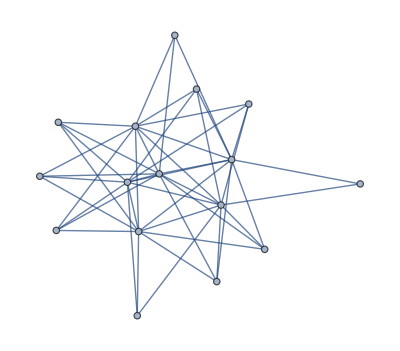

```mathematica
bivectorSubalgebraGraph[Cl[1,3]]=gaAlgebraMultiplicationTableGraph[Cl[1,3],gaGradesOnly->{{2}}]
```

```mathematica
VertexList[%]
```

{-1,23130,24130,34130,1,12130,13130,14130,-12130,-13130,-14130,-23130,-24130,1234130,-34130,-1234130}

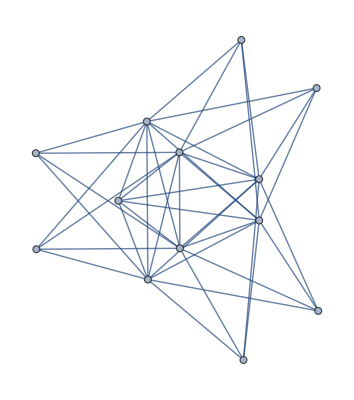

```mathematica
bivectorCommutatorGraph[Cl[1,3]]=gaAlgebraCommutatorTableGraph[Cl[1,3],gaGradesOnly->{{2}}]
```

```mathematica
Count[EdgeList[bivectorCommutatorGraph[Cl[1,3]]],12130,Infinity]
```

13

```mathematica
Cases[EdgeList[bivectorCommutatorGraph[Cl[1,3]]],UndirectedEdge[x_.*𝕖[mvDownUp[{1,2},{}],_],_],Infinity]
```

{12130<->0,12130<->-13130,12130<->13130,12130<->-14130,12130<->14130,12130<->-23130,12130<->23130,12130<->-24130,12130<->24130}

```mathematica
EdgeList[bivectorCommutatorGraph[Cl[1,3]]]
```

{12130<->0,12130<->-13130,12130<->13130,12130<->-14130,12130<->14130,12130<->-23130,12130<->23130,12130<->-24130,12130<->24130,13130<->0,13130<->-12130,13130<->-14130,13130<->14130,13130<->-23130,13130<->23130,13130<->-34130,13130<->34130,14130<->0,14130<->-12130,14130<->-13130,14130<->-24130,14130<->24130,14130<->-34130,14130<->34130,23130<->0,23130<->-12130,23130<->-13130,23130<->-24130,23130<->24130,23130<->-34130,23130<->34130,24130<->0,24130<->-12130,24130<->-14130,24130<->-23130,24130<->-34130,24130<->34130,34130<->0,34130<->-13130,34130<->-14130,34130<->-23130,34130<->-24130}

```mathematica
Reverse/@EdgeList[bivectorCommutatorGraph[Cl[1,3]]]
```

{0<->12130,-13130<->12130,13130<->12130,-14130<->12130,14130<->12130,-23130<->12130,23130<->12130,-24130<->12130,24130<->12130,0<->13130,-12130<->13130,-14130<->13130,14130<->13130,-23130<->13130,23130<->13130,-34130<->13130,34130<->13130,0<->14130,-12130<->14130,-13130<->14130,-24130<->14130,24130<->14130,-34130<->14130,34130<->14130,0<->23130,-12130<->23130,-13130<->23130,-24130<->23130,24130<->23130,-34130<->23130,34130<->23130,0<->24130,-12130<->24130,-14130<->24130,-23130<->24130,-34130<->24130,34130<->24130,0<->34130,-13130<->34130,-14130<->34130,-23130<->34130,-24130<->34130}

```mathematica
{Length[#],#}&/@{VertexList[bivectorCommutatorGraph[Cl[1,3]]],EdgeList[bivectorCommutatorGraph[Cl[1,3]]]}
```

{{13,{12130,0,-13130,13130,-14130,14130,-23130,23130,-24130,24130,-12130,-34130,34130}},{42,{12130<->0,12130<->-13130,12130<->13130,12130<->-14130,12130<->14130,12130<->-23130,12130<->23130,12130<->-24130,12130<->24130,13130<->0,13130<->-12130,13130<->-14130,13130<->14130,13130<->-23130,13130<->23130,13130<->-34130,13130<->34130,14130<->0,14130<->-12130,14130<->-13130,14130<->-24130,14130<->24130,14130<->-34130,14130<->34130,23130<->0,23130<->-12130,23130<->-13130,23130<->-24130,23130<->24130,23130<->-34130,23130<->34130,24130<->0,24130<->-12130,24130<->-14130,24130<->-23130,24130<->-34130,24130<->34130,34130<->0,34130<->-13130,34130<->-14130,34130<->-23130,34130<->-24130}}}

```mathematica
{gaCommutatorExpand[1/2][gaCommutator[12130,13130]],gaCommutatorExpand[1/2][gaCommutator[13130,12130]],gaCommutatorExpand[1/2][gaCommutator[-13130,12130]],gaCommutatorExpand[1/2][gaCommutator[-13130,-12130]]}
```

{-23130,23130,-23130,23130}

```mathematica
{makeCommutatorEdge[12130,13130],makeCommutatorEdge[13130,12130],makeCommutatorEdge[-13130,12130],makeCommutatorEdge[-13130,-12130]}
```

{{12130<->-23130,13130<->-23130},{13130<->23130,12130<->23130},{-13130<->-23130,12130<->-23130},{-13130<->23130,-12130<->23130}}

Graph of matrix product set (bad way)

Usage of associations would be preferable here instead of separate name/value lists (latter, if  ever)

```mathematica
baseMatrixList={{{0,1},{1,0}},{{0,-I},{I,0} },{{-1,0},{0,1}},I*{{0,1},{1,0}},I*{{0,-I},{I,0} },I*{{-1,0},{0,1}}};
namesList={"k1","k2","k3","j1","j2","j3"};
nameAndMatrixList=Thread[nameAndMatrix[namesList,baseMatrixList]]
```

{nameAndMatrix[k1,{{0,1},{1,0}}],nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],nameAndMatrix[k3,{{-1,0},{0,1}}],nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],nameAndMatrix[j2,{{0,1},{-1,0}}],nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]}

```mathematica
commutator[sk_.*k_nameAndMatrix,sj_.*j_nameAndMatrix,{nameList__String},{allBaseMatrices__?MatrixQ}]:=Module[{commutator=(1/2)*(sk*sj)*(k[[2]].j[[2]]-j[[2]].k[[2]]),dim=Dimensions[k[[2]]][[1]],projRe,nonEmptyPositions,projectedBaseMatrices,projectedMatricesNorms},
projRe=(Re/@((1/dim*Tr[#])&/@(Dot[commutator,#]&/@{allBaseMatrices})));
nonEmptyPositions=Unitize/@projRe;
If[!FreeQ[nonEmptyPositions,1],
projectedBaseMatrices=Pick[{allBaseMatrices},nonEmptyPositions,1];
projectedMatricesNorms=((1/dim)*Tr[Dot[#,#]]&/@projectedBaseMatrices);Plus@@(projectedMatricesNorms*Pick[projRe,nonEmptyPositions,1]*Thread[nameAndMatrix[Pick[{nameList},nonEmptyPositions,1],projectedBaseMatrices]]),
nameAndMatrix["0",ConstantArray[0,Dimensions[k[[2]]]]]
]
]
```

```mathematica
bothCommutators[{x_Rule,y_Rule},namesList_,baseMatrixList_]:=Rule@@(MapAt[(commutator[#[[1]],#[[2]],namesList,baseMatrixList]&),MapAt[Expand[((1/2)(GeometricProduct[#[[1]],#[[2]]]-GeometricProduct[#[[2]],#[[1]]]))]&,Transpose[List@@@{x,y}],1],2])
```

```mathematica
testSinglePair[isomorphismCandidateList_List,namesList_,baseMatrixList_]:=Module[{result=bothCommutators[#,namesList,baseMatrixList]&[(Take[isomorphismCandidateList,2])]},
If[MemberQ[isomorphismCandidateList,result],RotateLeft[isomorphismCandidateList,1],Throw[False]]]
```

```mathematica
testAllPairs[isomorphismCandidateList_List,namesList_,baseMatrixList_]:=
Catch[Nest[testSinglePair[#,namesList,baseMatrixList]&,RotateLeft[isomorphismCandidateList,1],Length[isomorphismCandidateList]-2]
]
```

```mathematica
gaMatrixCommutatorTableGraph::badOptionValue="??";

makeUndirectedForMatrix[sa_.*a_nameAndMatrix,sb_.*b_nameAndMatrix]:=UndirectedEdge[sa*a,sb*b]

makeCommutatorEdgeForMatrix[a_,b_,nameList_,baseMatrices_]:={makeUndirectedForMatrix[a,commutator[a,b,nameList,baseMatrices]],makeUndirectedForMatrix[b,commutator[a,b,nameList,baseMatrices]]}

gaMatrixCommutatorTableGraph[{namesList__String},{allBaseMatrices__?MatrixQ}]:=Module[{nameAndMatrixList=Thread[nameAndMatrix[{namesList},{allBaseMatrices}]],edges,sameEdge},
edges=Union[Flatten[Outer[makeCommutatorEdgeForMatrix[#1,#2,{namesList},{allBaseMatrices}]&,nameAndMatrixList,nameAndMatrixList]]];
sameEdge=Intersection[edges,Reverse/@edges];
Graph[Union[Complement[edges,sameEdge],Select[sameEdge,OrderedQ]]]
];
```

Tests of commutator[k_nameAndMatrix,j_nameAndMatrix,{nameList__String},{allBaseMatrices__?MatrixQ}]

```mathematica
commutator[nameAndMatrix["k1",{{0,1},{1,0}}],nameAndMatrix["j1",{{0,ⅈ},{ⅈ,0}}],namesList,baseMatrixList]
```

nameAndMatrix[0,{{0,0},{0,0}}]

```mathematica
commutator[nameAndMatrix["k1",{{0,1},{1,0}}],nameAndMatrix["k3",{{-1,0},{0,1}}],namesList,baseMatrixList]
```

nameAndMatrix[j2,{{0,1},{-1,0}}]

```mathematica
commutator[nameAndMatrix["k1",{{0,1},{1,0}}],nameAndMatrix["k2",{{0,-ⅈ},{ⅈ,0}}],namesList,baseMatrixList]
```

-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]

```mathematica
commutator[nameAndMatrix["k2",{{0,-ⅈ},{ⅈ,0}}],nameAndMatrix["k1",{{0,1},{1,0}}],namesList,baseMatrixList]
```

nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]

```mathematica
Table[commutator[nameAndMatrixList[[i]],nameAndMatrixList[[j]],namesList,baseMatrixList],{i,Length[nameAndMatrixList]},{j,Length[nameAndMatrixList]}]//TableForm
```

nameAndMatrix[0,{{0,0},{0,0}}] | -nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}] | nameAndMatrix[j2,{{0,1},{-1,0}}] | nameAndMatrix[0,{{0,0},{0,0}}] | nameAndMatrix[k3,{{-1,0},{0,1}}] | -nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]
nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}] | nameAndMatrix[0,{{0,0},{0,0}}] | -nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}] | -nameAndMatrix[k3,{{-1,0},{0,1}}] | nameAndMatrix[0,{{0,0},{0,0}}] | nameAndMatrix[k1,{{0,1},{1,0}}]
-nameAndMatrix[j2,{{0,1},{-1,0}}] | nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}] | nameAndMatrix[0,{{0,0},{0,0}}] | nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}] | -nameAndMatrix[k1,{{0,1},{1,0}}] | nameAndMatrix[0,{{0,0},{0,0}}]
nameAndMatrix[0,{{0,0},{0,0}}] | nameAndMatrix[k3,{{-1,0},{0,1}}] | -nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}] | nameAndMatrix[0,{{0,0},{0,0}}] | nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}] | -nameAndMatrix[j2,{{0,1},{-1,0}}]
-nameAndMatrix[k3,{{-1,0},{0,1}}] | nameAndMatrix[0,{{0,0},{0,0}}] | nameAndMatrix[k1,{{0,1},{1,0}}] | -nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}] | nameAndMatrix[0,{{0,0},{0,0}}] | nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}]
nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}] | -nameAndMatrix[k1,{{0,1},{1,0}}] | nameAndMatrix[0,{{0,0},{0,0}}] | nameAndMatrix[j2,{{0,1},{-1,0}}] | -nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}] | nameAndMatrix[0,{{0,0},{0,0}}]

Now make graph of general matrix commutators

```mathematica
{OrderedQ[{nameAndMatrix["k2",{{0,-ⅈ},{ⅈ,0}}],nameAndMatrix["k1",{{0,1},{1,0}}]}],OrderedQ[{nameAndMatrix["k1",{{0,-ⅈ},{ⅈ,0}}],nameAndMatrix["k2",{{0,1},{1,0}}]}],OrderedQ[{-nameAndMatrix["k1",{{0,-ⅈ},{ⅈ,0}}],nameAndMatrix["k2",{{0,1},{1,0}}]}]}
```

{False,True,True}

```mathematica
makeCommutatorEdgeForMatrix[nameAndMatrix["k2",{{0,-ⅈ},{ⅈ,0}}],nameAndMatrix["k1",{{0,1},{1,0}}],namesList,baseMatrixList]
```

{nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]<->nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],nameAndMatrix[k1,{{0,1},{1,0}}]<->nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]}

```mathematica
makeCommutatorEdgeForMatrix[nameAndMatrix["k2",{{0,-ⅈ},{ⅈ,0}}],-nameAndMatrix["k1",{{0,1},{1,0}}],namesList,baseMatrixList]
```

{nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]<->-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-nameAndMatrix[k1,{{0,1},{1,0}}]<->-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]}

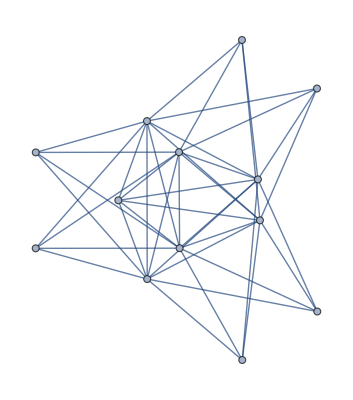

```mathematica
matrixGraph["sl(2,C)"]=gaMatrixCommutatorTableGraph[namesList,baseMatrixList]
```

```mathematica
Count[EdgeList[matrixGraph["sl(2,C)"]],{{0,1},{1,0}},Infinity]
```

13

```mathematica
Cases[EdgeList[matrixGraph["sl(2,C)"]],UndirectedEdge[x_.*nameAndMatrix["j3",_],_],Infinity]
```

{nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]<->nameAndMatrix[0,{{0,0},{0,0}}],nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]<->-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]<->-nameAndMatrix[j2,{{0,1},{-1,0}}],nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]<->-nameAndMatrix[k1,{{0,1},{1,0}}],nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]<->nameAndMatrix[k1,{{0,1},{1,0}}],nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]<->-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]<->nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]}

```mathematica
{Length[#],#}&/@{VertexList[matrixGraph["sl(2,C)"]],EdgeList[matrixGraph["sl(2,C)"]]}
```

{{13,{nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],nameAndMatrix[0,{{0,0},{0,0}}],-nameAndMatrix[j2,{{0,1},{-1,0}}],nameAndMatrix[j2,{{0,1},{-1,0}}],-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],-nameAndMatrix[k3,{{-1,0},{0,1}}],nameAndMatrix[k3,{{-1,0},{0,1}}],-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-nameAndMatrix[k1,{{0,1},{1,0}}],nameAndMatrix[k1,{{0,1},{1,0}}]}},{42,{nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}]<->nameAndMatrix[0,{{0,0},{0,0}}],nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}]<->-nameAndMatrix[j2,{{0,1},{-1,0}}],nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}]<->nameAndMatrix[j2,{{0,1},{-1,0}}],nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}]<->-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}]<->nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}]<->-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}]<->nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}]<->-nameAndMatrix[k3,{{-1,0},{0,1}}],nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}]<->nameAndMatrix[k3,{{-1,0},{0,1}}],nameAndMatrix[j2,{{0,1},{-1,0}}]<->nameAndMatrix[0,{{0,0},{0,0}}],nameAndMatrix[j2,{{0,1},{-1,0}}]<->-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],nameAndMatrix[j2,{{0,1},{-1,0}}]<->-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],nameAndMatrix[j2,{{0,1},{-1,0}}]<->nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],nameAndMatrix[j2,{{0,1},{-1,0}}]<->-nameAndMatrix[k1,{{0,1},{1,0}}],nameAndMatrix[j2,{{0,1},{-1,0}}]<->nameAndMatrix[k1,{{0,1},{1,0}}],nameAndMatrix[j2,{{0,1},{-1,0}}]<->-nameAndMatrix[k3,{{-1,0},{0,1}}],nameAndMatrix[j2,{{0,1},{-1,0}}]<->nameAndMatrix[k3,{{-1,0},{0,1}}],nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]<->nameAndMatrix[0,{{0,0},{0,0}}],nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]<->-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]<->-nameAndMatrix[j2,{{0,1},{-1,0}}],nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]<->-nameAndMatrix[k1,{{0,1},{1,0}}],nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]<->nameAndMatrix[k1,{{0,1},{1,0}}],nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]<->-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]<->nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],nameAndMatrix[k1,{{0,1},{1,0}}]<->nameAndMatrix[0,{{0,0},{0,0}}],nameAndMatrix[k1,{{0,1},{1,0}}]<->-nameAndMatrix[j2,{{0,1},{-1,0}}],nameAndMatrix[k1,{{0,1},{1,0}}]<->-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],nameAndMatrix[k1,{{0,1},{1,0}}]<->-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],nameAndMatrix[k1,{{0,1},{1,0}}]<->nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],nameAndMatrix[k1,{{0,1},{1,0}}]<->-nameAndMatrix[k3,{{-1,0},{0,1}}],nameAndMatrix[k1,{{0,1},{1,0}}]<->nameAndMatrix[k3,{{-1,0},{0,1}}],nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]<->nameAndMatrix[0,{{0,0},{0,0}}],nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]<->-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]<->-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]<->-nameAndMatrix[k1,{{0,1},{1,0}}],nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]<->-nameAndMatrix[k3,{{-1,0},{0,1}}],nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]<->nameAndMatrix[k3,{{-1,0},{0,1}}],nameAndMatrix[k3,{{-1,0},{0,1}}]<->nameAndMatrix[0,{{0,0},{0,0}}],nameAndMatrix[k3,{{-1,0},{0,1}}]<->-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],nameAndMatrix[k3,{{-1,0},{0,1}}]<->-nameAndMatrix[j2,{{0,1},{-1,0}}],nameAndMatrix[k3,{{-1,0},{0,1}}]<->-nameAndMatrix[k1,{{0,1},{1,0}}],nameAndMatrix[k3,{{-1,0},{0,1}}]<->-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]}}}

```mathematica
IsomorphicGraphQ[bivectorCommutatorGraph[Cl[1,3]],matrixGraph["sl(2,C)"]]
```

True

```mathematica
(allIsomorphisms["Cl[1,3]→sl(2,C)"]=FindGraphIsomorphism[bivectorCommutatorGraph[Cl[1,3]],matrixGraph["sl(2,C)"],All])//Length
```

384

Known result test and other tests (A. Dargys)

```mathematica
dargysIsomorphismResult={12130->nameAndMatrix["k1",{{0,1},{1,0}}],13130->nameAndMatrix["k2",{{0,-ⅈ},{ⅈ,0}}],14130->nameAndMatrix["k3",{{-1,0},{0,1}}],34130->nameAndMatrix["j1",{{0,ⅈ},{ⅈ,0}}],24130->-nameAndMatrix["j2",{{0,1},{-1,0}}],23130->nameAndMatrix["j3",{{-ⅈ,0},{0,ⅈ}}],
-12130->-nameAndMatrix["k1",{{0,1},{1,0}}],-13130->-nameAndMatrix["k2",{{0,-ⅈ},{ⅈ,0}}],-14130->-nameAndMatrix["k3",{{-1,0},{0,1}}],-34130->-nameAndMatrix["j1",{{0,ⅈ},{ⅈ,0}}],-24130->nameAndMatrix["j2",{{0,1},{-1,0}}],-23130->-nameAndMatrix["j3",{{-ⅈ,0},{0,ⅈ}}],
0->nameAndMatrix["0",{{0,0},{0,0}}]
};
```

```mathematica
testSinglePair[dargysIsomorphismResult,namesList,baseMatrixList]
```

{13130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],14130→nameAndMatrix[k3,{{-1,0},{0,1}}],34130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],24130→-nameAndMatrix[j2,{{0,1},{-1,0}}],23130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-12130→-nameAndMatrix[k1,{{0,1},{1,0}}],-13130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],-14130→-nameAndMatrix[k3,{{-1,0},{0,1}}],-34130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-24130→nameAndMatrix[j2,{{0,1},{-1,0}}],-23130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],0→nameAndMatrix[0,{{0,0},{0,0}}],12130→nameAndMatrix[k1,{{0,1},{1,0}}]}

```mathematica
testSinglePair[%,namesList,baseMatrixList]
```

{14130→nameAndMatrix[k3,{{-1,0},{0,1}}],34130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],24130→-nameAndMatrix[j2,{{0,1},{-1,0}}],23130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-12130→-nameAndMatrix[k1,{{0,1},{1,0}}],-13130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],-14130→-nameAndMatrix[k3,{{-1,0},{0,1}}],-34130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-24130→nameAndMatrix[j2,{{0,1},{-1,0}}],-23130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],0→nameAndMatrix[0,{{0,0},{0,0}}],12130→nameAndMatrix[k1,{{0,1},{1,0}}],13130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]}

```mathematica
testSinglePair[%,namesList,baseMatrixList]
```

{34130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],24130→-nameAndMatrix[j2,{{0,1},{-1,0}}],23130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-12130→-nameAndMatrix[k1,{{0,1},{1,0}}],-13130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],-14130→-nameAndMatrix[k3,{{-1,0},{0,1}}],-34130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-24130→nameAndMatrix[j2,{{0,1},{-1,0}}],-23130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],0→nameAndMatrix[0,{{0,0},{0,0}}],12130→nameAndMatrix[k1,{{0,1},{1,0}}],13130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],14130→nameAndMatrix[k3,{{-1,0},{0,1}}]}

```mathematica
bothCommutators[{12130->nameAndMatrix["k1",{{0,1},{1,0}}],13130->nameAndMatrix["k2",{{0,-ⅈ},{ⅈ,0}}]},namesList,baseMatrixList]
```

-23130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]

```mathematica
bothCommutators[{14130->nameAndMatrix["k3",{{-1,0},{0,1}}],34130->-nameAndMatrix["j1",{{0,ⅈ},{ⅈ,0}}]},namesList,baseMatrixList]
```

13130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]

```mathematica
bothCommutators[{14130->nameAndMatrix["k3",{{-1,0},{0,1}}],12130->nameAndMatrix["k1",{{0,1},{1,0}}]},namesList,baseMatrixList]
```

24130→-nameAndMatrix[j2,{{0,1},{-1,0}}]

```mathematica
testAllPairs[#,namesList,baseMatrixList]&[dargysIsomorphismResult]
```

{0→nameAndMatrix[0,{{0,0},{0,0}}],12130→nameAndMatrix[k1,{{0,1},{1,0}}],13130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],14130→nameAndMatrix[k3,{{-1,0},{0,1}}],34130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],24130→-nameAndMatrix[j2,{{0,1},{-1,0}}],23130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-12130→-nameAndMatrix[k1,{{0,1},{1,0}}],-13130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],-14130→-nameAndMatrix[k3,{{-1,0},{0,1}}],-34130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-24130→nameAndMatrix[j2,{{0,1},{-1,0}}],-23130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]}

Step by step action

```mathematica
testSinglePair[RotateLeft[Normal[allIsomorphisms["Cl[1,3]→sl(2,C)"]][[70]],1],namesList,baseMatrixList]
```

{-13130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],13130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-14130→-nameAndMatrix[k1,{{0,1},{1,0}}],14130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-23130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],23130→nameAndMatrix[k1,{{0,1},{1,0}}],-24130→-nameAndMatrix[k3,{{-1,0},{0,1}}],24130→nameAndMatrix[k3,{{-1,0},{0,1}}],-12130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],-34130→-nameAndMatrix[j2,{{0,1},{-1,0}}],34130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],12130→nameAndMatrix[j2,{{0,1},{-1,0}}],0→nameAndMatrix[0,{{0,0},{0,0}}]}

```mathematica
testSinglePair[%,namesList,baseMatrixList]
```

{13130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-14130→-nameAndMatrix[k1,{{0,1},{1,0}}],14130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-23130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],23130→nameAndMatrix[k1,{{0,1},{1,0}}],-24130→-nameAndMatrix[k3,{{-1,0},{0,1}}],24130→nameAndMatrix[k3,{{-1,0},{0,1}}],-12130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],-34130→-nameAndMatrix[j2,{{0,1},{-1,0}}],34130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],12130→nameAndMatrix[j2,{{0,1},{-1,0}}],0→nameAndMatrix[0,{{0,0},{0,0}}],-13130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}]}

```mathematica
testSinglePair[%,namesList,baseMatrixList]
```

Throw::nocatch: Uncaught Throw[False] returned to top level.

Hold[Throw[False]]

```mathematica
testSinglePair[%,namesList,baseMatrixList]
```

testSinglePair[Hold[Throw[False]],{k1,k2,k3,j1,j2,j3},{{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{-1,0},{0,1}},{{0,ⅈ},{ⅈ,0}},{{0,1},{-1,0}},{{-ⅈ,0},{0,ⅈ}}}]

Full search in the set of all graph isomorphisms

```mathematica
trueIsomorphisms["Cl[1,3]→sl(2,C)"]=DeleteCases[testAllPairs[#,namesList,baseMatrixList]&/@Normal[allIsomorphisms["Cl[1,3]→sl(2,C)"]],False]
```

{{34130→nameAndMatrix[k1,{{0,1},{1,0}}],12130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],0→nameAndMatrix[0,{{0,0},{0,0}}],-13130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],13130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-14130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],14130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],-23130→-nameAndMatrix[j2,{{0,1},{-1,0}}],23130→nameAndMatrix[j2,{{0,1},{-1,0}}],-24130→-nameAndMatrix[k3,{{-1,0},{0,1}}],24130→nameAndMatrix[k3,{{-1,0},{0,1}}],-12130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-34130→-nameAndMatrix[k1,{{0,1},{1,0}}]},{34130→nameAndMatrix[k1,{{0,1},{1,0}}],12130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],0→nameAndMatrix[0,{{0,0},{0,0}}],-13130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],13130→nameAndMatrix[k3,{{-1,0},{0,1}}],-14130→-nameAndMatrix[j2,{{0,1},{-1,0}}],14130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],-23130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],23130→nameAndMatrix[j2,{{0,1},{-1,0}}],-24130→-nameAndMatrix[k3,{{-1,0},{0,1}}],24130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-12130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-34130→-nameAndMatrix[k1,{{0,1},{1,0}}]},{34130→nameAndMatrix[k1,{{0,1},{1,0}}],12130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],0→nameAndMatrix[0,{{0,0},{0,0}}],-13130→-nameAndMatrix[k3,{{-1,0},{0,1}}],13130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-14130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],14130→nameAndMatrix[j2,{{0,1},{-1,0}}],-23130→-nameAndMatrix[j2,{{0,1},{-1,0}}],23130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],-24130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],24130→nameAndMatrix[k3,{{-1,0},{0,1}}],-12130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-34130→-nameAndMatrix[k1,{{0,1},{1,0}}]},{34130→nameAndMatrix[k1,{{0,1},{1,0}}],12130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],0→nameAndMatrix[0,{{0,0},{0,0}}],-13130→-nameAndMatrix[k3,{{-1,0},{0,1}}],13130→nameAndMatrix[k3,{{-1,0},{0,1}}],-14130→-nameAndMatrix[j2,{{0,1},{-1,0}}],14130→nameAndMatrix[j2,{{0,1},{-1,0}}],-23130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],23130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],-24130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],24130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-12130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-34130→-nameAndMatrix[k1,{{0,1},{1,0}}]},{34130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],12130→nameAndMatrix[j2,{{0,1},{-1,0}}],0→nameAndMatrix[0,{{0,0},{0,0}}],-13130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],13130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-14130→-nameAndMatrix[k3,{{-1,0},{0,1}}],14130→nameAndMatrix[k3,{{-1,0},{0,1}}],-23130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],23130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-24130→-nameAndMatrix[k1,{{0,1},{1,0}}],24130→nameAndMatrix[k1,{{0,1},{1,0}}],-12130→-nameAndMatrix[j2,{{0,1},{-1,0}}],-34130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]},{34130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],12130→nameAndMatrix[j2,{{0,1},{-1,0}}],0→nameAndMatrix[0,{{0,0},{0,0}}],-13130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],13130→nameAndMatrix[k1,{{0,1},{1,0}}],-14130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],14130→nameAndMatrix[k3,{{-1,0},{0,1}}],-23130→-nameAndMatrix[k3,{{-1,0},{0,1}}],23130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-24130→-nameAndMatrix[k1,{{0,1},{1,0}}],24130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-12130→-nameAndMatrix[j2,{{0,1},{-1,0}}],-34130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]},{34130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],12130→nameAndMatrix[j2,{{0,1},{-1,0}}],0→nameAndMatrix[0,{{0,0},{0,0}}],-13130→-nameAndMatrix[k1,{{0,1},{1,0}}],13130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-14130→-nameAndMatrix[k3,{{-1,0},{0,1}}],14130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-23130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],23130→nameAndMatrix[k3,{{-1,0},{0,1}}],-24130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],24130→nameAndMatrix[k1,{{0,1},{1,0}}],-12130→-nameAndMatrix[j2,{{0,1},{-1,0}}],-34130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]},{34130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],12130→nameAndMatrix[j2,{{0,1},{-1,0}}],0→nameAndMatrix[0,{{0,0},{0,0}}],-13130→-nameAndMatrix[k1,{{0,1},{1,0}}],13130→nameAndMatrix[k1,{{0,1},{1,0}}],-14130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],14130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-23130→-nameAndMatrix[k3,{{-1,0},{0,1}}],23130→nameAndMatrix[k3,{{-1,0},{0,1}}],-24130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],24130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-12130→-nameAndMatrix[j2,{{0,1},{-1,0}}],-34130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]},{34130→nameAndMatrix[k3,{{-1,0},{0,1}}],12130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],0→nameAndMatrix[0,{{0,0},{0,0}}],-13130→-nameAndMatrix[j2,{{0,1},{-1,0}}],13130→nameAndMatrix[j2,{{0,1},{-1,0}}],-14130→-nameAndMatrix[k1,{{0,1},{1,0}}],14130→nameAndMatrix[k1,{{0,1},{1,0}}],-23130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],23130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-24130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],24130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],-12130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-34130→-nameAndMatrix[k3,{{-1,0},{0,1}}]},{34130→nameAndMatrix[k3,{{-1,0},{0,1}}],12130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],0→nameAndMatrix[0,{{0,0},{0,0}}],-13130→-nameAndMatrix[j2,{{0,1},{-1,0}}],13130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],-14130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],14130→nameAndMatrix[k1,{{0,1},{1,0}}],-23130→-nameAndMatrix[k1,{{0,1},{1,0}}],23130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-24130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],24130→nameAndMatrix[j2,{{0,1},{-1,0}}],-12130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-34130→-nameAndMatrix[k3,{{-1,0},{0,1}}]},{34130→nameAndMatrix[k3,{{-1,0},{0,1}}],12130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],0→nameAndMatrix[0,{{0,0},{0,0}}],-13130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],13130→nameAndMatrix[j2,{{0,1},{-1,0}}],-14130→-nameAndMatrix[k1,{{0,1},{1,0}}],14130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-23130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],23130→nameAndMatrix[k1,{{0,1},{1,0}}],-24130→-nameAndMatrix[j2,{{0,1},{-1,0}}],24130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],-12130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-34130→-nameAndMatrix[k3,{{-1,0},{0,1}}]},{34130→nameAndMatrix[k3,{{-1,0},{0,1}}],12130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],0→nameAndMatrix[0,{{0,0},{0,0}}],-13130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],13130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],-14130→-nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],14130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],-23130→-nameAndMatrix[k1,{{0,1},{1,0}}],23130→nameAndMatrix[k1,{{0,1},{1,0}}],-24130→-nameAndMatrix[j2,{{0,1},{-1,0}}],24130→nameAndMatrix[j2,{{0,1},{-1,0}}],-12130→-nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],-34130→-nameAndMatrix[k3,{{-1,0},{0,1}}]}}

Problem bad signs!!!

Test of multiplication tables: first isomorphism

```mathematica
bivectorMatrixMatches["Cl[1,3]→sl(2,C)"]=Cases[trueIsomorphisms["Cl[1,3]→sl(2,C)"][[1]],HoldPattern[_𝕖->_],Infinity]
```

```mathematica
bivectorMatrixMatches["Cl[1,3]→sl(2,C)"]={34130->nameAndMatrix["k1",{{0,1},{1,0}}],12130->nameAndMatrix["j1",{{0,ⅈ},{ⅈ,0}}],13130->nameAndMatrix["j3",{{-ⅈ,0},{0,ⅈ}}],14130->nameAndMatrix["k2",{{0,-ⅈ},{ⅈ,0}}],23130->nameAndMatrix["j2",{{0,1},{-1,0}}],24130->-nameAndMatrix["k3",{{-1,0},{0,1}}]}
```

{34130→nameAndMatrix[k1,{{0,1},{1,0}}],12130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],13130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],14130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],23130→nameAndMatrix[j2,{{0,1},{-1,0}}],24130→-nameAndMatrix[k3,{{-1,0},{0,1}}]}

```mathematica
TableForm[Table[gaCommutatorExpand[1/2][gaCommutator[First[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"][[i]]],First[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"][[j]]]]],{i,Length[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"]]},{j,Length[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"]]}]]
```

0 | 0 | 14130 | -13130 | 24130 | -23130
0 | 0 | -23130 | -24130 | -13130 | -14130
-14130 | 23130 | 0 | -34130 | 12130 | 0
13130 | 24130 | 34130 | 0 | 0 | 12130
-24130 | 13130 | -12130 | 0 | 0 | 34130
23130 | 14130 | 0 | -12130 | -34130 | 0

```mathematica
commutator[Last[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"][[1]]],Last[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"][[3]]],namesList,baseMatrixList]
```

-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]

```mathematica
gaCommutatorExpand[1/2][gaCommutator[First[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"][[1]]],First[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"][[3]]]]]
```

14130

```mathematica
TableForm[Table[commutator[Last[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"][[i]]],Last[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"][[j]]],namesList,baseMatrixList],{i,Length[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"]]},{j,Length[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"]]}]]/.{nameAndMatrix[x_String,_]:>x}
```

0 | 0 | -k2 | -j3 | k3 | -j2
0 | 0 | -j2 | k3 | j3 | k2
k2 | j2 | 0 | -k1 | -j1 | 0
j3 | -k3 | k1 | 0 | 0 | j1
-k3 | -j3 | j1 | 0 | 0 | -k1
j2 | -k2 | 0 | -j1 | k1 | 0

```mathematica
bothCommutators[{34130->nameAndMatrix["k1",{{0,1},{1,0}}],13130->nameAndMatrix["j3",{{-ⅈ,0},{0,ⅈ}}]},namesList,baseMatrixList]
```

14130→-nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]

Second isomorphism

```mathematica
bivectorMatrixMatches["Cl[1,3]→sl(2,C)"]=Cases[trueIsomorphisms["Cl[1,3]→sl(2,C)"][[2]],HoldPattern[_𝕖->_],Infinity]
```

{12130→nameAndMatrix[j2,{{0,1},{-1,0}}],13130→nameAndMatrix[k1,{{0,1},{1,0}}],14130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],23130→nameAndMatrix[k3,{{-1,0},{0,1}}],24130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],34130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}]}

```mathematica
TableForm[Table[gaCommutatorExpand[1/2][gaCommutator[First[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"][[i]]],First[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"][[j]]]]],{i,Length[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"]]},{j,Length[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"]]}]]
```

0 | -23130 | -24130 | -13130 | -14130 | 0
23130 | 0 | -34130 | 12130 | 0 | -14130
24130 | 34130 | 0 | 0 | 12130 | 13130
13130 | -12130 | 0 | 0 | 34130 | -24130
14130 | 0 | -12130 | -34130 | 0 | 23130
0 | 14130 | -13130 | 24130 | -23130 | 0

```mathematica
TableForm[Table[commutator[Last[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"][[i]]],Last[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"][[j]]],namesList,baseMatrixList],{i,Length[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"]]},{j,Length[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"]]}]]/.{nameAndMatrix[x_String,_]:>x}
```

0 | -k3 | j1 | k1 | -j3 | 0
k3 | 0 | -k2 | j2 | 0 | -j3
-j1 | k2 | 0 | 0 | j2 | -k1
-k1 | -j2 | 0 | 0 | k2 | j1
j3 | 0 | -j2 | -k2 | 0 | k3
0 | j3 | k1 | -j1 | -k3 | 0

Third isomorphism

```mathematica
bivectorMatrixMatches["Cl[1,3]→sl(2,C)"]=Cases[trueIsomorphisms["Cl[1,3]→sl(2,C)"][[3]],HoldPattern[_𝕖->_],Infinity]
```

{12130→nameAndMatrix[j3,{{-ⅈ,0},{0,ⅈ}}],13130→nameAndMatrix[k2,{{0,-ⅈ},{ⅈ,0}}],14130→nameAndMatrix[j1,{{0,ⅈ},{ⅈ,0}}],23130→nameAndMatrix[k1,{{0,1},{1,0}}],24130→nameAndMatrix[j2,{{0,1},{-1,0}}],34130→nameAndMatrix[k3,{{-1,0},{0,1}}]}

```mathematica
TableForm[Table[gaCommutatorExpand[1/2][gaCommutator[First[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"][[i]]],First[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"][[j]]]]],{i,Length[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"]]},{j,Length[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"]]}]]
```

0 | -23130 | -24130 | -13130 | -14130 | 0
23130 | 0 | -34130 | 12130 | 0 | -14130
24130 | 34130 | 0 | 0 | 12130 | 13130
13130 | -12130 | 0 | 0 | 34130 | -24130
14130 | 0 | -12130 | -34130 | 0 | 23130
0 | 14130 | -13130 | 24130 | -23130 | 0

```mathematica
TableForm[Table[commutator[Last[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"][[i]]],Last[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"][[j]]],namesList,baseMatrixList],{i,Length[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"]]},{j,Length[bivectorMatrixMatches["Cl[1,3]→sl(2,C)"]]}]]/.{nameAndMatrix[x_String,_]:>x}
```

0 | -k1 | j2 | k2 | -j1 | 0
k1 | 0 | -k3 | j3 | 0 | -j1
-j2 | k3 | 0 | 0 | j3 | -k2
-k2 | -j3 | 0 | 0 | k3 | j2
j1 | 0 | -j3 | -k3 | 0 | k1
0 | j1 | k2 | -j2 | -k1 | 0

```mathematica
dargysIsomorphismResult=Cases[{12130->nameAndMatrix["k1",{{0,1},{1,0}}],13130->nameAndMatrix["k2",{{0,-ⅈ},{ⅈ,0}}],14130->nameAndMatrix["k3",{{-1,0},{0,1}}],34130->nameAndMatrix["j1",{{0,ⅈ},{ⅈ,0}}],24130->-nameAndMatrix["j2",{{0,1},{-1,0}}],23130->nameAndMatrix["j3",{{-ⅈ,0},{0,ⅈ}}],
-12130->-nameAndMatrix["k1",{{0,1},{1,0}}],-13130->-nameAndMatrix["k2",{{0,-ⅈ},{ⅈ,0}}],-14130->-nameAndMatrix["k3",{{-1,0},{0,1}}],-34130->-nameAndMatrix["j1",{{0,ⅈ},{ⅈ,0}}],-24130->nameAndMatrix["j2",{{0,1},{-1,0}}],-23130->-nameAndMatrix["j3",{{-ⅈ,0},{0,ⅈ}}],
0->nameAndMatrix["0",{{0,0},{0,0}}]
},HoldPattern[_𝕖->_],Infinity];
```

```mathematica
TableForm[Table[gaCommutatorExpand[1/2][gaCommutator[First[dargysIsomorphismResult[[i]]],First[dargysIsomorphismResult[[j]]]]],{i,Length[dargysIsomorphismResult]},{j,Length[dargysIsomorphismResult]}]]
```

0 | -23130 | -24130 | 0 | -14130 | -13130
23130 | 0 | -34130 | -14130 | 0 | 12130
24130 | 34130 | 0 | 13130 | 12130 | 0
0 | 14130 | -13130 | 0 | -23130 | 24130
14130 | 0 | -12130 | 23130 | 0 | -34130
13130 | -12130 | 0 | -24130 | 34130 | 0

```mathematica
TableForm[Table[commutator[Last[dargysIsomorphismResult[[i]]],Last[dargysIsomorphismResult[[j]]],namesList,baseMatrixList],{i,Length[dargysIsomorphismResult]},{j,Length[dargysIsomorphismResult]}]]/.{nameAndMatrix[x_String,_]:>x}
```

0 | -j3 | j2 | 0 | -k3 | -k2
j3 | 0 | -j1 | -k3 | 0 | k1
-j2 | j1 | 0 | k2 | k1 | 0
0 | k3 | -k2 | 0 | -j3 | -j2
k3 | 0 | -k1 | j3 | 0 | -j1
k2 | -k1 | 0 | j2 | j1 | 0

#### 5. 17 sl(2,R)->Cl(2,1)

Sulake definitions for all algebras (needed to get sl(2,C) base)

```mathematica
(*A general vector *)

vec[x_, n_:dim] := Table[x[i], {i, n}]

(*A random vector with values in the unit n-cube *)

randomv[n_:dim]:= Table[Random[],{i,n}]

(*A random matrix of type (n,k) with elements in the unit intervall *)

randommatrix[k_, n_:dim]:=Table[randomv[n], {i,k}]

(*A function which makes small entities to become zero.*)

smoothing[a_,b_:10^(-10)]:=
  Module[{c=a},If[b==1,Return[c],If[Abs[N[c]]<b,c=0]; c,c]];
Attributes[smoothing]=Listable;

(*Standard matrices *)

nullmatrix[k_Integer, n_Integer] := Table[0, {k}, {n}];
nullmatrix[n_Integer:dim] := nullmatrix[n, n]

matrix[a_,n_,m_]:= Array[a, {n, m}];
matrix[a_,n_:dim] := matrix[a, n, n]

(*Remark: We want to distinguish symbolic vectors from symbolic matrices,
and to have simple definitions, like xv = vec[x], am = matrix[a], for 
symbolic vectors and square matrices of order dim. Therefore we 
specialized the Array concept.*)

basismatrix[i_,j_,n_:dim]:=
  Table[KroneckerDelta[i,k]*KroneckerDelta[j,l],{k,n},{l,n}]

(*The commutator*)

commute[m_?MatrixQ, l_?MatrixQ] := 
	(m . l - l . m)/;(Dimensions[m] == Dimensions[l]&&
        Dimensions[m][[1]] == Dimensions[m][[2]]) 

(*The general linear Lie algebra gl(n,K) *)

glbasis[n_Integer:dim] := Module[{ord = n, i,j},
		Flatten[Table[basismatrix[i,j,ord],{i,n}, {j,n}],1]]

cobasis[i_,j_,n_:dim][m_] := 
  Sum[KroneckerDelta[i,k]*KroneckerDelta[j,l]*m[[k,l]],{k,1,n},{l,1,n}]

strconst[i_,j_,r_,s_,u_,v_,n_:dim]:= 
  cobasis[i,j][commute[basismatrix[r,s,n],basismatrix[u,v,n]]]

glkilling[a_, b_, n_:dim] :=     
  Sum[Sum[cobasis[i, j,n][ commute[a, commute[b,basismatrix[i, j,n]]]],
        {i, 1, n}], {j, 1, n}]

zelm[z_, n_:dim] := IdentityMatrix[n]*z

matrixoutzero[b_List] := Module[{v= {}, l = Length[b], k = Length[b[[1]]],i},
			For[i = 1, i<= l, i++, 
		If[Not[smoothing[b[[i]]] == nullmatrix[k]],
AppendTo[v, b[[i]]],Null[],AppendTo[v, b[[i]]]]]; Return[v]]

normalize[v_,prod_:glkilling]:=Module[{a=Simplify[prod[v,v]],w},If[a==0,w=v,w=v/Sqrt[Abs[a]],w=v/Sqrt[Abs[a]]];
Return[w]]

Options[matrixorthonorm]={innerprod->glkilling,normed->True,print->False,neglect->-10};
matrixorthonorm[b_List,opts___]:=Module[{v,w,va,vb,l,ort={},i,j,f,h,sm,aus,prod,nor,pr,bn,follow,iso,control},{prod,nor,pr,bn}={innerprod,normed,print,neglect}/.{opts}/.Options[matrixorthonorm];
f[h_]:=smoothing[h,10^bn];
sm[aus_]:=MapAll[f,aus];
w=matrixoutzero[sm[b]];
Label[follow];
l=Length[w];
If[l==0,Goto[control]];
For[i=1,i≤l,i++,If[Not[Simplify[sm[prod[w[[i]],w[[i]]]]]==0],AppendTo[ort,w[[i]]];
If[pr==True,Print[w[[i]]//MatrixForm]];
v=Simplify[sm[Table[w[[j]]-w[[i]]*prod[w[[i]],w[[j]]]/prod[w[[i]],w[[i]]],{j,l}]]];
w=matrixoutzero[v]; Goto[follow],Null,AppendTo[ort,w[[i]]];
If[pr==True,Print[w[[i]]//MatrixForm]];
v=Simplify[sm[Table[w[[j]]-w[[i]]*prod[w[[i]],w[[j]]]/prod[w[[i]],w[[i]]],{j,l}]]];
w=matrixoutzero[v]; Goto[follow]]];
Label[iso];l=Length[w];
If[l==0,Goto[control]];
v=w;
If[l==1,AppendTo[ort,v[[1]]]; If[pr==True,Print[v[[1]]//MatrixForm]];
Goto[control]];
For[i=1,i≤l,i++,For[j=i+1,j≤l,j++,If[Not[Simplify[sm[prod[v[[i]],v[[j]]]]]==0],va=v[[j]]-v[[i]];
vb=v[[j]]+v[[i]]; 				v[[i]]=va;v[[j]]=vb;
w=matrixoutzero[Simplify[sm[v]]];Goto[follow]]]]; 			ort=Join[ort,v];
Label[control];
l=Length[ort];
If[l==0,Return[ort]];
If[nor==True,ort=sm[Table[Simplify[normalize[ort[[i]],prod]],{i,Length[ort]}]]];
For[i=1,i≤l-1,i++,For[j=i+1,j≤l,j++,If[Not[Simplify[sm[prod[ort[[i]],ort[[j]]]]]==0],Return[Print["I cannot orthogonalize the given sequence!"]],Null,Return[Print["I cannot orthogonalize the given sequence!"]]]]]; 	Return[ort]]
```

A basis of sl(n,K)

```mathematica
slbasismatrix[i_, j_,n_:dim] :=basismatrix[i,j,n]/;i!= j;
slbasismatrix[i_, j_, n_:dim] := (basismatrix[i,j,n]-basismatrix[n,n,n])/;(i== j&& j<n);
commute[m_, l_] := Simplify[m . l - l . m] ;
slbasis[n_:dim] := Join[Flatten[Table[slbasismatrix[i,j,n],{i, n-1},{j, n}],1],Table[slbasismatrix[n,h,n], {h,n-1}]];
slbasisMF[n_:dim] := Join[Flatten[Table[slbasismatrix[i,j,n]//MatrixForm,{i, n-1},{j, n}],1],Table[slbasismatrix[n,h,n]//MatrixForm, {h,n-1}]];
sprod[n_][a_,b_] := glkilling[a,b,n]
```

```mathematica
sl2b=slbasis[2]
```

{{{1,0},{0,-1}},{{0,1},{0,0}},{{0,0},{1,0}}}

```mathematica
Table[glkilling[sl2b[[i]],sl2b[[j]],2],{i,3},{j,3}]
```

{{8,0,0},{0,0,4},{0,4,0}}

```mathematica
MatrixForm/@(slbasisMatrices[2]=matrixorthonorm[slbasis[2], innerprod -> sprod[2]])
```

{(1/(2 √2) | 0
0 | -1/(2 √2)),(0 | -1/(2 √2)
1/(2 √2) | 0),(0 | 1/(2 √2)
1/(2 √2) | 0)}

#### SU(4,c)->Cl(0,6) (bad way)

Sulake definitions for all algebras (needed to get sl(2,C) base) (bad way)

```mathematica
(*A general vector *)

vec[x_, n_:dim] := Table[x[i], {i, n}]

(*A random vector with values in the unit n-cube *)

randomv[n_:dim]:= Table[Random[],{i,n}]

(*A random matrix of type (n,k) with elements in the unit intervall *)

randommatrix[k_, n_:dim]:=Table[randomv[n], {i,k}]

(*A function which makes small entities to become zero.*)

smoothing[a_,b_:10^(-10)]:=
  Module[{c=a},If[b==1,Return[c],If[Abs[N[c]]<b,c=0]; c,c]];
Attributes[smoothing]=Listable;

(*Standard matrices *)

nullmatrix[k_Integer, n_Integer] := Table[0, {k}, {n}];
nullmatrix[n_Integer:dim] := nullmatrix[n, n]

matrix[a_,n_,m_]:= Array[a, {n, m}];
matrix[a_,n_:dim] := matrix[a, n, n]

(*Remark: We want to distinguish symbolic vectors from symbolic matrices,
and to have simple definitions, like xv = vec[x], am = matrix[a], for 
symbolic vectors and square matrices of order dim. Therefore we 
specialized the Array concept.*)

basismatrix[i_,j_,n_:dim]:=
  Table[KroneckerDelta[i,k]*KroneckerDelta[j,l],{k,n},{l,n}]

(*The commutator*)

commute[m_?MatrixQ, l_?MatrixQ] := 
	(m . l - l . m)/;(Dimensions[m] == Dimensions[l]&&
        Dimensions[m][[1]] == Dimensions[m][[2]]) 

(*The general linear Lie algebra gl(n,K) *)

glbasis[n_Integer:dim] := Module[{ord = n, i,j},
		Flatten[Table[basismatrix[i,j,ord],{i,n}, {j,n}],1]]

cobasis[i_,j_,n_:dim][m_] := 
  Sum[KroneckerDelta[i,k]*KroneckerDelta[j,l]*m[[k,l]],{k,1,n},{l,1,n}]

strconst[i_,j_,r_,s_,u_,v_,n_:dim]:= 
  cobasis[i,j][commute[basismatrix[r,s,n],basismatrix[u,v,n]]]

glkilling[a_, b_, n_:dim] :=     
  Sum[Sum[cobasis[i, j,n][ commute[a, commute[b,basismatrix[i, j,n]]]],
        {i, 1, n}], {j, 1, n}]

zelm[z_, n_:dim] := IdentityMatrix[n]*z

matrixoutzero[b_List] := Module[{v= {}, l = Length[b], k = Length[b[[1]]],i},
			For[i = 1, i<= l, i++, 
		If[Not[smoothing[b[[i]]] == nullmatrix[k]],
AppendTo[v, b[[i]]],Null[],AppendTo[v, b[[i]]]]]; Return[v]]

normalize[v_,prod_:glkilling]:=Module[{a=Simplify[prod[v,v]],w},If[a==0,w=v,w=v/Sqrt[Abs[a]],w=v/Sqrt[Abs[a]]];
Return[w]]

Options[matrixorthonorm]={innerprod->glkilling,normed->True,print->False,neglect->-10};
matrixorthonorm[b_List,opts___]:=Module[{v,w,va,vb,l,ort={},i,j,f,h,sm,aus,prod,nor,pr,bn,follow,iso,control},{prod,nor,pr,bn}={innerprod,normed,print,neglect}/.{opts}/.Options[matrixorthonorm];
f[h_]:=smoothing[h,10^bn];
sm[aus_]:=MapAll[f,aus];
w=matrixoutzero[sm[b]];
Label[follow];
l=Length[w];
If[l==0,Goto[control]];
For[i=1,i≤l,i++,If[Not[Simplify[sm[prod[w[[i]],w[[i]]]]]==0],AppendTo[ort,w[[i]]];
If[pr==True,Print[w[[i]]//MatrixForm]];
v=Simplify[sm[Table[w[[j]]-w[[i]]*prod[w[[i]],w[[j]]]/prod[w[[i]],w[[i]]],{j,l}]]];
w=matrixoutzero[v]; Goto[follow],Null,AppendTo[ort,w[[i]]];
If[pr==True,Print[w[[i]]//MatrixForm]];
v=Simplify[sm[Table[w[[j]]-w[[i]]*prod[w[[i]],w[[j]]]/prod[w[[i]],w[[i]]],{j,l}]]];
w=matrixoutzero[v]; Goto[follow]]];
Label[iso];l=Length[w];
If[l==0,Goto[control]];
v=w;
If[l==1,AppendTo[ort,v[[1]]]; If[pr==True,Print[v[[1]]//MatrixForm]];
Goto[control]];
For[i=1,i≤l,i++,For[j=i+1,j≤l,j++,If[Not[Simplify[sm[prod[v[[i]],v[[j]]]]]==0],va=v[[j]]-v[[i]];
vb=v[[j]]+v[[i]]; 				v[[i]]=va;v[[j]]=vb;
w=matrixoutzero[Simplify[sm[v]]];Goto[follow]]]]; 			ort=Join[ort,v];
Label[control];
l=Length[ort];
If[l==0,Return[ort]];
If[nor==True,ort=sm[Table[Simplify[normalize[ort[[i]],prod]],{i,Length[ort]}]]];
For[i=1,i≤l-1,i++,For[j=i+1,j≤l,j++,If[Not[Simplify[sm[prod[ort[[i]],ort[[j]]]]]==0],Return[Print["I cannot orthogonalize the given sequence!"]],Null,Return[Print["I cannot orthogonalize the given sequence!"]]]]]; 	Return[ort]]
```

Sulake definitions for su(4,C) base (bad way)

```mathematica
Clear[dim]
```

obm is from orthogonal group

```mathematica
obm[i_, j_,n_:dim] := basismatrix[i, j,n] - basismatrix[j, i, n]/;i < j
```

```mathematica
uelm[a_,n_:dim] :=Module[{k, c=Table[a[k], {k,  n^2}]}, Declare[c,Real];
			 Sum[ubasis[n][[k]]*a[k], {k, n^2}]]
```

```mathematica
ucobasisa[i_,j_,n_:dim][m_?MatrixQ]:= Re[cobasis[i,j,n][m]]/;(i<j&&j<=n)
```

```mathematica
ucobasisb[i_,j_,n_:dim][m_?MatrixQ]:= Im[cobasis[i,j,n][m]]/;(i<j&&j<=n)
```

```mathematica
ucobasisc[i_,n_:dim][m_?MatrixQ]:= Im[cobasis[i,i,n][m]]/;(i<=n)
```

```mathematica
ucobasis[n_:dim][m_?MatrixQ] :=Join[Flatten[Join[Table[ucobasisa[i,j,n][m],{j, 2,n},{i,1,j-1}],Table[ucobasisb[i,j,n][m],{j, 2,n},{i,1,j-1}]], 1],Table[ucobasisc[i,n][m], {i,n}]]
```

```mathematica
ukilling[x_?MatrixQ, y_?MatrixQ,n_:dim] := Sum[ucobasis[n][commute[x,commute[y,ubasis[n][[i]]]]][[i]],{i, n^2}]
```

```mathematica
ubasisa[i_, j_, n_:dim]:= obm[i,j,n]/;(i< j && j<= n)
```

```mathematica
ubasisb[i_, j_, n_:dim]:=(basismatrix[i,j,n]+ basismatrix[j,i,n])*I/;(i< j && j<= n)
```

```mathematica
ubasisc[i_,  n_:dim]:=basismatrix[i,i,n]*I/;(i<= n)
```

```mathematica
ubasis[n_:dim] :=Join[Flatten[Join[Table[ubasisa[i,j,n],{j, 2,n},{i,1,j-1}],Table[ubasisb[i,j,n],{j, 2,n},{i,1,j-1}]], 1],Table[ubasisc[i,n], {i,n}]]
```

```mathematica
subasis[n_:dim] := Join[Table[ubasis[n][[i]], {i, n*(n-1)}],
Table[ubasis[n][[j]] - ubasis[n][[n^2]], {j,n*(n-1)+1, n^2 -1}]]
```

Sulake attempt (bad way)

Diagonal matrices

```mathematica
Table[subasis[4][[j]]//MatrixForm, {j,4*(4-1)+1, 4^2 -1}]
```

{(ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ),(0 | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ)}

```mathematica
Table[subasis[5][[j]]//MatrixForm, {j,5*(5-1)+1, 5^2 -1}]
```

{(ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ),(0 | 0 | 0 | 0 | 0
0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ),(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | -ⅈ)}

The general element of su(n) is

```mathematica
suelm[a_, n_:dim] := Module[{k, c=Table[a[k], {k,  n^2}]}, 
			 Sum[subasis[n][[k]]*a[k], {k, n^2-1}]]
```

```mathematica
(abc = suelm[a,4])//MatrixForm
```

(ⅈ a[13] | a[1]+ⅈ a[7] | a[2]+ⅈ a[8] | a[4]+ⅈ a[10]
-a[1]+ⅈ a[7] | ⅈ a[14] | a[3]+ⅈ a[9] | a[5]+ⅈ a[11]
-a[2]+ⅈ a[8] | -a[3]+ⅈ a[9] | ⅈ a[15] | a[6]+ⅈ a[12]
-a[4]+ⅈ a[10] | -a[5]+ⅈ a[11] | -a[6]+ⅈ a[12] | -ⅈ a[13]-ⅈ a[14]-ⅈ a[15])

```mathematica
(abc/.{Complex[x_,y_]:>Complex[x,-y]} )== - Transpose[abc]
```

True

```mathematica
MatrixForm/@subasis[4]
```

{(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | -1 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | ⅈ | 0
0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0
0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),(ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ),(0 | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ)}

```mathematica
dim=4;
MatrixForm/@(subasisMatrices[4]=matrixorthonorm[subasis[4], innerprod -> ukilling])
```

{(0 | 1/4 | 0 | 0
-1/4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 1/4 | 0
0 | 0 | 0 | 0
-1/4 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 1/4 | 0
0 | -1/4 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 1/4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/4 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 1/4
0 | 0 | 0 | 0
0 | -1/4 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1/4
0 | 0 | -1/4 | 0),(0 | ⅈ/4 | 0 | 0
ⅈ/4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | ⅈ/4 | 0
0 | 0 | 0 | 0
ⅈ/4 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | ⅈ/4 | 0
0 | ⅈ/4 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | ⅈ/4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
ⅈ/4 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ/4
0 | 0 | 0 | 0
0 | ⅈ/4 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ/4
0 | 0 | ⅈ/4 | 0),(ⅈ/4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/4),(-ⅈ/(4 √3) | 0 | 0 | 0
0 | ⅈ/(2 √3) | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/(4 √3)),(-ⅈ/(4 √6) | 0 | 0 | 0
0 | -ⅈ/(4 √6) | 0 | 0
0 | 0 | 1/4 ⅈ √(3/2) | 0
0 | 0 | 0 | -ⅈ/(4 √6))}

Trace of algebra elements should be zero.

```mathematica
Tr/@subasisMatrices[4]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
namessubasisMatrices[4]=Table["su"<>ToString[i],{i,Length[subasisMatrices[4]]}]
```

{su1,su2,su3,su4,su5,su6,su7,su8,su9,su10,su11,su12,su13,su14,su15}

```mathematica
baseMatrixList=4subasisMatrices[4];
namesList=namessubasisMatrices[4];
nameAndMatrixList=Thread[nameAndMatrix[namesList,baseMatrixList]]
```

{nameAndMatrix[su1,{{0,1,0,0},{-1,0,0,0},{0,0,0,0},{0,0,0,0}}],nameAndMatrix[su2,{{0,0,1,0},{0,0,0,0},{-1,0,0,0},{0,0,0,0}}],nameAndMatrix[su3,{{0,0,0,0},{0,0,1,0},{0,-1,0,0},{0,0,0,0}}],nameAndMatrix[su4,{{0,0,0,1},{0,0,0,0},{0,0,0,0},{-1,0,0,0}}],nameAndMatrix[su5,{{0,0,0,0},{0,0,0,1},{0,0,0,0},{0,-1,0,0}}],nameAndMatrix[su6,{{0,0,0,0},{0,0,0,0},{0,0,0,1},{0,0,-1,0}}],nameAndMatrix[su7,{{0,ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,0},{0,0,0,0}}],nameAndMatrix[su8,{{0,0,ⅈ,0},{0,0,0,0},{ⅈ,0,0,0},{0,0,0,0}}],nameAndMatrix[su9,{{0,0,0,0},{0,0,ⅈ,0},{0,ⅈ,0,0},{0,0,0,0}}],nameAndMatrix[su10,{{0,0,0,ⅈ},{0,0,0,0},{0,0,0,0},{ⅈ,0,0,0}}],nameAndMatrix[su11,{{0,0,0,0},{0,0,0,ⅈ},{0,0,0,0},{0,ⅈ,0,0}}],nameAndMatrix[su12,{{0,0,0,0},{0,0,0,0},{0,0,0,ⅈ},{0,0,ⅈ,0}}],nameAndMatrix[su13,{{ⅈ,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-ⅈ}}],nameAndMatrix[su14,{{-ⅈ/(√3),0,0,0},{0,(2 ⅈ)/(√3),0,0},{0,0,0,0},{0,0,0,-ⅈ/(√3)}}],nameAndMatrix[su15,{{-ⅈ/(√6),0,0,0},{0,-ⅈ/(√6),0,0},{0,0,ⅈ √(3/2),0},{0,0,0,-ⅈ/(√6)}}]}

```mathematica
nameAndMatrixList[[2]]
```

nameAndMatrix[su2,{{0,0,1,0},{0,0,0,0},{-1,0,0,0},{0,0,0,0}}]

```mathematica
nameAndMatrix["su2",{{0,0,1,1},{0,0,0,0},{-1,0,0,0},{0,0,0,0}}]
```

nameAndMatrix[su2,{{0,0,1,1},{0,0,0,0},{-1,0,0,0},{0,0,0,0}}]

```mathematica
{{0,0,1,1},{0,0,0,0},{-1,0,0,0},{0,0,0,0}}
```

{{0,0,1,1},{0,0,0,0},{-1,0,0,0},{0,0,0,0}}

```mathematica
commutator[nameAndMatrixList[[1]],nameAndMatrix["su2",{{0,0,1,120},{0,1,0,0},{-130,0,1,0},{1,1,1,1}}],namesList,baseMatrixList]
```

commutator[nameAndMatrix[su1,{{0,1,0,0},{-1,0,0,0},{0,0,0,0},{0,0,0,0}}],nameAndMatrix[su2,{{0,0,1,120},{0,1,0,0},{-130,0,1,0},{1,1,1,1}}],{su1,su2,su3,su4,su5,su6,su7,su8,su9,su10,su11,su12,su13,su14,su15},{{{0,1,0,0},{-1,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0},{-1,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,1,0},{0,-1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0},{0,0,0,0},{-1,0,0,0}},{{0,0,0,0},{0,0,0,1},{0,0,0,0},{0,-1,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,1},{0,0,-1,0}},{{0,ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,ⅈ,0},{0,0,0,0},{ⅈ,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,ⅈ,0},{0,ⅈ,0,0},{0,0,0,0}},{{0,0,0,ⅈ},{0,0,0,0},{0,0,0,0},{ⅈ,0,0,0}},{{0,0,0,0},{0,0,0,ⅈ},{0,0,0,0},{0,ⅈ,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,ⅈ},{0,0,ⅈ,0}},{{ⅈ,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-ⅈ}},{{-ⅈ/(√3),0,0,0},{0,(2 ⅈ)/(√3),0,0},{0,0,0,0},{0,0,0,-ⅈ/(√3)}},{{-ⅈ/(√6),0,0,0},{0,-ⅈ/(√6),0,0},{0,0,ⅈ √(3/2),0},{0,0,0,-ⅈ/(√6)}}}]

```mathematica
commutator[nameAndMatrixList[[1]],nameAndMatrix["su2",{{0,0,1,1},{0,0,0,0},{-1,0,0,0},{0,0,0,0}}],namesList,baseMatrixList]
```

commutator[nameAndMatrix[su1,{{0,1,0,0},{-1,0,0,0},{0,0,0,0},{0,0,0,0}}],nameAndMatrix[su2,{{0,0,1,1},{0,0,0,0},{-1,0,0,0},{0,0,0,0}}],{su1,su2,su3,su4,su5,su6,su7,su8,su9,su10,su11,su12,su13,su14,su15},{{{0,1,0,0},{-1,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0},{-1,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,1,0},{0,-1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0},{0,0,0,0},{-1,0,0,0}},{{0,0,0,0},{0,0,0,1},{0,0,0,0},{0,-1,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,1},{0,0,-1,0}},{{0,ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,ⅈ,0},{0,0,0,0},{ⅈ,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,ⅈ,0},{0,ⅈ,0,0},{0,0,0,0}},{{0,0,0,ⅈ},{0,0,0,0},{0,0,0,0},{ⅈ,0,0,0}},{{0,0,0,0},{0,0,0,ⅈ},{0,0,0,0},{0,ⅈ,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,ⅈ},{0,0,ⅈ,0}},{{ⅈ,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-ⅈ}},{{-ⅈ/(√3),0,0,0},{0,(2 ⅈ)/(√3),0,0},{0,0,0,0},{0,0,0,-ⅈ/(√3)}},{{-ⅈ/(√6),0,0,0},{0,-ⅈ/(√6),0,0},{0,0,ⅈ √(3/2),0},{0,0,0,-ⅈ/(√6)}}}]

```mathematica
Table[commutator[nameAndMatrixList[[i]],nameAndMatrixList[[j]],namesList,baseMatrixList],{i,Length[nameAndMatrixList]},{j,Length[nameAndMatrixList]}]
```

{1}
 |  |  |  |

```mathematica
commutator[nameAndMatrix["su1",{{0,1,0,0},{-1,0,0,0},{0,0,0,0},{0,0,0,0}}],nameAndMatrix["su2",{{0,0,1,0},{0,0,0,0},{-1,0,0,0},{0,0,0,0}}],namesList,baseMatrixList]
```

commutator[nameAndMatrix[su1,{{0,1,0,0},{-1,0,0,0},{0,0,0,0},{0,0,0,0}}],nameAndMatrix[su2,{{0,0,1,0},{0,0,0,0},{-1,0,0,0},{0,0,0,0}}],{su1,su2,su3,su4,su5,su6,su7,su8,su9,su10,su11,su12,su13,su14,su15},{{{0,1,0,0},{-1,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,1,0},{0,0,0,0},{-1,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,1,0},{0,-1,0,0},{0,0,0,0}},{{0,0,0,1},{0,0,0,0},{0,0,0,0},{-1,0,0,0}},{{0,0,0,0},{0,0,0,1},{0,0,0,0},{0,-1,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,1},{0,0,-1,0}},{{0,ⅈ,0,0},{ⅈ,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,ⅈ,0},{0,0,0,0},{ⅈ,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,ⅈ,0},{0,ⅈ,0,0},{0,0,0,0}},{{0,0,0,ⅈ},{0,0,0,0},{0,0,0,0},{ⅈ,0,0,0}},{{0,0,0,0},{0,0,0,ⅈ},{0,0,0,0},{0,ⅈ,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,ⅈ},{0,0,ⅈ,0}},{{ⅈ,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-ⅈ}},{{-ⅈ/(√3),0,0,0},{0,(2 ⅈ)/(√3),0,0},{0,0,0,0},{0,0,0,-ⅈ/(√3)}},{{-ⅈ/(√6),0,0,0},{0,-ⅈ/(√6),0,0},{0,0,ⅈ √(3/2),0},{0,0,0,-ⅈ/(√6)}}}]

```mathematica
MatrixForm[(#[[1]].#[[2]]-#[[2]].#[[1]])&[{4subasisMatrices[4][[1]],4subasisMatrices[4][[2]]}]]
```

(0 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
MatrixForm[(1/2)(#[[1]].#[[2]]-#[[2]].#[[1]])&[{{{1,0},{0,-1}},{{0,-1},{1,0}}}]]
```

(0 | -1
-1 | 0)

```mathematica
((1/2)(#[[1]].#[[2]]-#[[2]].#[[1]]))&[subasisMatrices[4]]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | -1/32 | 0
0 | 1/32 | 0 | 0
0 | 0 | 0 | 0)

#### SU(4,c)->Cl(0,6) (right way)

Calculation from even algebra isomorphism to lower dimensional algebra representation

Cl(0,6) even subalgebra is equivalent to Cl(0,5) full representations

```mathematica
testAlgebra=Cl[0,5];
reducedAlgebra[testAlgebra]=gaToTensorProduct[testAlgebra]
```

010200020

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra])
```

gaAlgebraToMatrixRepresentation::NoDefaultData: No explicit default representations of elementary algebras for Cl[0,5,0] was given. Will use {{0→Complex,Cl[1,0,0]→Diagonal,Cl[1,1,0]→Antisymmetric,2→Symmetric,0→Pauli[1,2]},Method→TensorProduct} .

Base vectors of 010are stored in variable gaOrthonormalBase[Cl[0, 1, 0],{0, 1}].

Base vectors of 010200are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0]],{0, 1}].

Base vectors of 010200020are stored in variable gaOrthonormalBase[gaTensorProduct[Cl[0, 1, 0], Cl[2, 0, 0], Cl[0, 2, 0]],{1}].

{(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)}

```mathematica
MatrixForm/@(vectors[testAlgebra,1]=gaAlgebraToMatrixRepresentation[testAlgebra,{Cl[0,1]->"Complex",Cl[2,0]->"Symmetric",Cl[0,2]->"Pauli[1,2]"},Method ->"TensorProduct"])
```

gaDefineInput::gaTensorProductAlgebra: gaRunningAlgebra was set to tensor product 0. Input alias of base element was disabled, it only works with Cl[p,q] algebras.

{(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
(allElements[testAlgebra]=gaAlgebraToMatrixRepresentation[testAlgebra,vectors[testAlgebra,1]])//Length
```

32

```mathematica
replRules[testAlgebra]=Thread[Rule[gaOrthonormalBase[testAlgebra],allElements[testAlgebra]]];
```

```mathematica
MatrixForm/@(bivectors[testAlgebra]=gaOrthonormalBase[testAlgebra,{2}]/.replRules[testAlgebra])
```

{(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0),(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0),(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0),(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ)}

Calculation from even algebra isomorphism to lower dimensional algebra representation

```mathematica
Clear[namesList,baseMatrixList,nameAndMatrixList];
Format[nameAndMatrix[x_String,y_?MatrixQ],StandardForm]:=nameAndMatrix[x,MatrixForm[y]]

commutator[sk_.*k_nameAndMatrix,sj_.*j_nameAndMatrix,{nameList__String},{allBaseMatrices__?MatrixQ}]:=Module[{commutator=(1/2)*(sk*sj)*(k[[2]].j[[2]]-j[[2]].k[[2]]),dim=Dimensions[k[[2]]][[1]],projRe,nonEmptyPositions,projectedBaseMatrices,projectedMatricesNorms},
projRe=(Re/@((1/dim*Tr[#])&/@(Dot[commutator,#]&/@{allBaseMatrices})));
nonEmptyPositions=Unitize/@projRe;
If[!FreeQ[nonEmptyPositions,1],
projectedBaseMatrices=Pick[{allBaseMatrices},nonEmptyPositions,1];
projectedMatricesNorms=((1/dim)*Tr[Dot[#,#]]&/@projectedBaseMatrices);Plus@@(projectedMatricesNorms*Pick[projRe,nonEmptyPositions,1]*Thread[nameAndMatrix[Pick[{nameList},nonEmptyPositions,1],projectedBaseMatrices]]),
nameAndMatrix["0",ConstantArray[0,Dimensions[k[[2]]]]]
]
]
```

```mathematica
MakeExpression[nameAndMatrix[x_String,y_?MatrixForm],StandardForm]:=nameAndMatrix[x,y/.{MatrixForm->Identity}]
```

```mathematica
baseMatrixList[testAlgebra]=Join[vectors[testAlgebra,1],bivectors[testAlgebra]];
namesList[testAlgebra]=Table["su"<>ToString[i],{i,Length[baseMatrixList[testAlgebra]]}];
(nameAndMatrixList[testAlgebra]=Thread[nameAndMatrix[namesList[testAlgebra],baseMatrixList[testAlgebra]]])
```

{nameAndMatrix[su1,(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ)],nameAndMatrix[su2,(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[su3,(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0)],nameAndMatrix[su4,(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)],nameAndMatrix[su5,(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)],nameAndMatrix[su6,(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0)],nameAndMatrix[su7,(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)],nameAndMatrix[su8,(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
1 | 0 | 0 | 0)],nameAndMatrix[su9,(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0)],nameAndMatrix[su10,(ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ)],nameAndMatrix[su11,(0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ
ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)],nameAndMatrix[su12,(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0)],nameAndMatrix[su13,(0 | 0 | -1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)],nameAndMatrix[su14,(0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ
-ⅈ | 0 | 0 | 0
0 | -ⅈ | 0 | 0)],nameAndMatrix[su15,(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ)]}

```mathematica
simpleCommutator[sk_.*k_nameAndMatrix,sj_.*j_nameAndMatrix,___]:=(1/2)*sk*sj(k[[2]].j[[2]]-j[[2]].k[[2]])
```

```mathematica
MatrixForm/@Table[simpleCommutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrix["su2",{{0,1,0,0},{-1,0,0,0},{0,0,0,1},{0,0,-1,0}}],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]}]
```

{(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | ⅈ | 0
0 | 0 | 0 | -ⅈ),(0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ
-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0),(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),(-ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | ⅈ),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0),(0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

```mathematica
commutator[nameAndMatrixList[testAlgebra][[1]],nameAndMatrix["su2",{{0,1,0,0},{-1,0,0,0},{0,0,0,1},{0,0,-1,0}}],namesList[testAlgebra],baseMatrixList[testAlgebra]]
```

nameAndMatrix[su6,(0 | ⅈ | 0 | 0
ⅈ | 0 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0)]

```mathematica
(allMatrixCommutatorTable=Table[commutator[nameAndMatrixList[testAlgebra][[i]],nameAndMatrixList[testAlgebra][[j]],namesList[testAlgebra],baseMatrixList[testAlgebra]],{i,Length[namesList[testAlgebra]]},{j,Length[namesList[testAlgebra]]}]);
MatrixForm[allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x}]
```

(0 | su6 | su7 | su8 | su9 | -su2 | -su3 | -su4 | -su5 | 0 | 0 | 0 | 0 | 0 | 0
-su6 | 0 | su10 | su11 | su12 | su1 | 0 | 0 | 0 | -su3 | -su4 | -su5 | 0 | 0 | 0
-su7 | -su10 | 0 | su13 | su14 | 0 | su1 | 0 | 0 | su2 | 0 | 0 | -su4 | -su5 | 0
-su8 | -su11 | -su13 | 0 | su15 | 0 | 0 | su1 | 0 | 0 | su2 | 0 | su3 | 0 | -su5
-su9 | -su12 | -su14 | -su15 | 0 | 0 | 0 | 0 | su1 | 0 | 0 | su2 | 0 | su3 | su4
su2 | -su1 | 0 | 0 | 0 | 0 | su10 | su11 | su12 | -su7 | -su8 | -su9 | 0 | 0 | 0
su3 | 0 | -su1 | 0 | 0 | -su10 | 0 | su13 | su14 | su6 | 0 | 0 | -su8 | -su9 | 0
su4 | 0 | 0 | -su1 | 0 | -su11 | -su13 | 0 | su15 | 0 | su6 | 0 | su7 | 0 | -su9
su5 | 0 | 0 | 0 | -su1 | -su12 | -su14 | -su15 | 0 | 0 | 0 | su6 | 0 | su7 | su8
0 | su3 | -su2 | 0 | 0 | su7 | -su6 | 0 | 0 | 0 | su13 | su14 | -su11 | -su12 | 0
0 | su4 | 0 | -su2 | 0 | su8 | 0 | -su6 | 0 | -su13 | 0 | su15 | su10 | 0 | -su12
0 | su5 | 0 | 0 | -su2 | su9 | 0 | 0 | -su6 | -su14 | -su15 | 0 | 0 | su10 | su11
0 | 0 | su4 | -su3 | 0 | 0 | su8 | -su7 | 0 | su11 | -su10 | 0 | 0 | su15 | -su14
0 | 0 | su5 | 0 | -su3 | 0 | su9 | 0 | -su7 | su12 | 0 | -su10 | -su15 | 0 | su13
0 | 0 | 0 | su5 | -su4 | 0 | 0 | su9 | -su8 | 0 | su12 | -su11 | su14 | -su13 | 0)

```mathematica
bivectorBase[Cl[6,0]]=gaDefineOrthonormalBase[Cl[6,0],gaGradesOnly->{2}]
```

{12600,13600,14600,15600,16600,23600,24600,25600,26600,34600,35600,36600,45600,46600,56600}

```mathematica
TableForm[bivectorCommutatorTable[Cl[6,0]]=Table[gaCommutatorExpand[1/2][gaCommutator[bivectorBase[Cl[6,0]][[i]],bivectorBase[Cl[6,0]][[j]]]],{i,Length[bivectorBase[Cl[6,0]]]},{j,Length[bivectorBase[Cl[6,0]]]}]]
```

0 | -23600 | -24600 | -25600 | -26600 | 13600 | 14600 | 15600 | 16600 | 0 | 0 | 0 | 0 | 0 | 0
23600 | 0 | -34600 | -35600 | -36600 | -12600 | 0 | 0 | 0 | 14600 | 15600 | 16600 | 0 | 0 | 0
24600 | 34600 | 0 | -45600 | -46600 | 0 | -12600 | 0 | 0 | -13600 | 0 | 0 | 15600 | 16600 | 0
25600 | 35600 | 45600 | 0 | -56600 | 0 | 0 | -12600 | 0 | 0 | -13600 | 0 | -14600 | 0 | 16600
26600 | 36600 | 46600 | 56600 | 0 | 0 | 0 | 0 | -12600 | 0 | 0 | -13600 | 0 | -14600 | -15600
-13600 | 12600 | 0 | 0 | 0 | 0 | -34600 | -35600 | -36600 | 24600 | 25600 | 26600 | 0 | 0 | 0
-14600 | 0 | 12600 | 0 | 0 | 34600 | 0 | -45600 | -46600 | -23600 | 0 | 0 | 25600 | 26600 | 0
-15600 | 0 | 0 | 12600 | 0 | 35600 | 45600 | 0 | -56600 | 0 | -23600 | 0 | -24600 | 0 | 26600
-16600 | 0 | 0 | 0 | 12600 | 36600 | 46600 | 56600 | 0 | 0 | 0 | -23600 | 0 | -24600 | -25600
0 | -14600 | 13600 | 0 | 0 | -24600 | 23600 | 0 | 0 | 0 | -45600 | -46600 | 35600 | 36600 | 0
0 | -15600 | 0 | 13600 | 0 | -25600 | 0 | 23600 | 0 | 45600 | 0 | -56600 | -34600 | 0 | 36600
0 | -16600 | 0 | 0 | 13600 | -26600 | 0 | 0 | 23600 | 46600 | 56600 | 0 | 0 | -34600 | -35600
0 | 0 | -15600 | 14600 | 0 | 0 | -25600 | 24600 | 0 | -35600 | 34600 | 0 | 0 | -56600 | 46600
0 | 0 | -16600 | 0 | 14600 | 0 | -26600 | 0 | 24600 | -36600 | 0 | 34600 | 56600 | 0 | -45600
0 | 0 | 0 | -16600 | 15600 | 0 | 0 | -26600 | 25600 | 0 | -36600 | 35600 | -46600 | 45600 | 0

```mathematica
Union[(DeleteCases[Flatten[Thread/@Thread[Rule[bivectorCommutatorTable[Cl[6,0]],(allMatrixCommutatorTable/.{nameAndMatrix[x_String,_]:>x})]]],Rule[0,"0"]])/.{Rule[-x_,y_]:>x->-y}]
```

{12600→-su1,13600→-su2,14600→-su3,15600→-su4,16600→-su5,23600→-su6,24600→-su7,25600→-su8,26600→-su9,34600→-su10,35600→-su11,36600→-su12,45600→-su13,46600→-su14,56600→-su15}

#### Group action on triangle example (unfinished)

```mathematica
graphicsStyle={FontSize->9,FontFamily->"MathJax_Math",Plain,Black};
cm=72/2.54 ;(*centimetres*)
mydir="/home/acus/git/acus/LaTeX/figuresNew/";
SetOptions[Graphics,BaseStyle->graphicsStyle];SetOptions[Graphics3D,BaseStyle->graphicsStyle];
SetOptions[Plot,BaseStyle->graphicsStyle];
```

```mathematica
testAlgebra=Cl[2,0];
gaDefineOrthonormalBase[testAlgebra,Quiet->True]
```

gaDefineOrthonormalBase[Cl[2,0],Quiet→True]

```mathematica
{v[1],v[2],v[3]}=Expand[Plus@@@(({𝕖[1],𝕖[2]}*#)&/@((#+{-s/2,-(√3 s)/6})&/@{{0,0},{s,0},{s/2,(√3 s)/2}}))]
```

{-1/2 s 𝕖[1]-(s 𝕖[2])/(2 √3),1/2 s 𝕖[1]-(s 𝕖[2])/(2 √3),-(s 𝕖[2])/(2 √3)+1/2 √3 s 𝕖[2]}

```mathematica
EquilateralTriangle[s_]:=Line/@Subsets[(#+{-s/2,-(√3 s)/6})&/@{{0,0},{s,0},{s/2,(√3 s)/2}},{2}];
VertexVectors[s_]:=Arrow[{{0,0},#}]&/@((#+{-s/2,-(√3 s)/6})&/@{{0,0},{s,0},{s/2,(√3 s)/2}});
VertexText[s_,{v1_,v2_,v3_}]:=Thread[Text[Style[#,FontFamily->"MathJax_Math",FontSize->Medium]&/@{v1,v2,v3},((#+{-s/2,-(√3 s)/6})&/@{{0,0},{s,0},{s/2,(√3 s)/2}})]];
```

```mathematica
arcarrow=Show[ParametricPlot[#[[1]]*{Cos[θ],Sin[θ]},{θ,#[[2]],#[[3]]},Axes->False,PlotStyle->#[[4]]]/.Line[x_]:>Sequence[Arrowheads[{-0,Small}],Arrow[x]]&/@{{0.25,-Pi/2+Pi/3,-Pi/2+2Pi/3,Black,AbsoluteThickness[1]}},PlotRange->All,ImageSize->5.0cm]/.AbsoluteThickness[_]:>AbsoluteThickness[1];
```

```mathematica
Show[arcarrow]
```

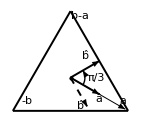

```mathematica
triangleAdjoint=Show[{arcarrow,Graphics[Flatten[{EdgeForm[Black],Thickness[0.01],EquilateralTriangle[2],{Thickness[0.005],VertexVectors[1.9][[2]]},{Thickness[0.01],VertexVectors[1][[2]]},{VertexText[1,{"","â",""}]/.{Text[x_,y_]:>Text[x,y,{0,1}]}},{Text[Style["b̂",FontFamily->"MathJax_Math",FontSize->Medium],({s/(2 √3),s/2}+{s/2,(√3 s)/2})/.s->1/3,{0,1}]},
{Text[Style["π/3",FontFamily->"MathJax_Math",FontSize->Small],{0.45,0},{0,0}]},
{Thickness[0.01],Arrow[((#+{s/2,(√3 s)/2})&/@{{-s/2,(-√3 s)/2},{s,0}})/.s->1/3]},{Dashed,Thickness[0.01],Arrow[{{0,0},{s/(2 √3),-s/2}/.s->1}]},
{Text[Style["b̂'",FontFamily->"MathJax_Math",FontSize->Medium],{s/(2 √3),-s/2}/.s->1,{2.4,0}]},{(VertexText[1.7,{"-b","a","b-a"}]/.{Text[x_,y_]:>Text[x,y,{-2.6,-0.5}]})/.{Text[x_,y_,{-2.6,-0.5}]:>Text[x,y,{-1.5,-0.5}]/;!FreeQ[x,"b-a"],Text[x_,y_,{-2.6,-0.5}]:>Text[x,y,{-1.,-0.5}]/;!FreeQ[x,"-b"]}},{PointSize[Large],Point[{0,0}]}}]]},AspectRatio->Automatic,ImageSize->5.0cm]
```

```mathematica
Export[FileNameJoin[{mydir,"triangleL.eps"}],triangleAdjoint]
```

/home/acus/git/acus/LaTeX/figuresNew/triangleL.eps

```mathematica
arcarrowTA=Show[ParametricPlot[#[[1]]*{Cos[θ],Sin[θ]},{θ,#[[2]],#[[3]]},Axes->False,PlotStyle->#[[4]]]/.Line[x_]:>Sequence[Arrowheads[{-0,Small}],Arrow[x]]&/@{{0.2,0,+Pi/3,Black,AbsoluteThickness[1]}},PlotRange->All,ImageSize->5.0cm]/.AbsoluteThickness[_]:>AbsoluteThickness[1];
```

```mathematica
SymmetryElements[s_]:={Arrowheads[{-0,Small}],Arrow[{#[[1]],#[[2]]}],Arrow[{#[[1]],#[[3]]}]}&[((#+{0,0})&/@{{0,0},{s,0},{s/2,(√3 s)/2}})];
```

```mathematica
generators={Text[Style["b̂",FontFamily->"MathJax_Math",FontSize->Medium],{0.5,0.6}],Text[Style["â",FontFamily->"MathJax_Math",FontSize->Medium],{0.8,0.1}]}
```

{Text[b̂,{0.5,0.6}],Text[â,{0.8,0.1}]}

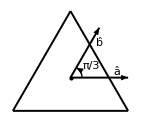

```mathematica
triangleTwistedAdoint=Show[{arcarrowTA,Graphics[generators],Graphics[Flatten[{EdgeForm[Black],Thickness[0.01],EquilateralTriangle[2],{Thickness[0.01], SymmetryElements[1]},
{Text[Style["π/3",FontFamily->"MathJax_Math",FontSize->Small],{0.36,0.2},{0,0}]},{PointSize[Large],Point[{0,0}]}}]]},AspectRatio->Automatic,ImageSize->5.0cm]
```

```mathematica
Export[FileNameJoin[{mydir,"triangleR.eps"}],triangleTwistedAdoint]
```

/home/acus/git/acus/LaTeX/figuresNew/triangleR.eps

```mathematica
coords={{{0,0,0},{0,1,0},{1,1,0},{1,0,0}},{{0,0,0},{1,0,0},{1,0,1},{0,0,1}},{{1,0,0},{1,1,0},{1,1,1},{1,0,1}},{{1,1,0},{0,1,0},{0,1,1},{1,1,1}},{{0,1,0},{0,0,0},{0,0,1},{0,1,1}},{{0,0,1},{1,0,1},{1,1,1},{0,1,1}}};

vertices=Union[Flatten[coords,1]];
text=Style[#,FontFamily->"MathJax_Math",FontSize->Small]&/@{"ℝ","ℍ","ℝ","ℍ","ℂ","ℂ","ℝ⊕ℝ","ℍ⊕ℍ"};
txt=Append[#,{0,1}]&/@Thread[Text[text,vertices]];
axes={{{0,1,0},{0,0.4,0}},{{0,1,0},{0,1,0.6}},{{0,1,0},{0.6,1,0}}};
numbers=Style[#,FontFamily->"MathJax_Math",FontSize->Small]&/@{"2","6","0","4","3","7","1","5"};
numbersTxt=Append[#,{1,-1}]&/@Thread[Text[numbers,vertices]];
xyz={Text[Style["x",FontFamily->"MathJax_Math",FontSize->Small],{0.5,1.5,0},{1,1}],Text[Style["y",FontFamily->"MathJax_Math",FontSize->Small],{0.2,0.3,0},{1,-1}],Text[Style["z",FontFamily->"MathJax_Math",FontSize->Small],{0.1,1,0.5},{1,-1}]};
```

```mathematica
v={1,2,1}
```

{1,2,1}

```mathematica
v
```

{0.582201,-2.33469,0.458547}

```mathematica
realCliffordAlgebraCube=Graphics3D[{{Thickness[0.005],Line/@coords},{txt},xyz,{numbersTxt},{Thickness[0.01],Arrow/@axes}},Boxed->False,AspectRatio->Automatic,ViewPoint->{0.7822005811863681,-2.334689974300126,0.45854684293835235},ImageSize->5.0cm]
```

-Graphics3D-

```mathematica
Export[FileNameJoin[{mydir,"AlgebraCube.eps"}],realCliffordAlgebraCube]
```

/home/acus/git/acus/LaTeX/figuresNew/AlgebraCube.eps